```mathematica
consulta = "df = pd.read_sql(\"\"\"SELECT patient_id,frace,document_id,token_cancer from Alltokens where document_id 
    between 0 and 1000 and token_cancer in ('CANCER_CONCEPT', 'COMORBIDITY', 'AGE', 'TNM', 'TREATMENT_NAME','DRUG','SURGERY')
    group by document_id,patient_id,frace,token_cancer \"\"\" , con)
    print(df.head(10))
    df.to_csv('alltokens.csv', index=False) ";
```

```mathematica
data=Import["/home/jose/Files/Complex Systems/proyecto/alltokens.csv", "Data"];
size = Length[data];
Table[data[[i,j]],{i,Length[data]},{j,Length[data[[1]]]}] //TableView
```

patient_idfracedocument_idtoken_cancer136631CARCINOMA DE MAMA0CANCER_CONCEPT136631Primario0CANCER_CONCEPT136631TAMOXIFENO0DRUG136631TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA0CANCER_CONCEPT21723135 Años1AGE217231Acetato1DRUG217231Acetato de1DRUG217231Acido1DRUG217231CANCER DE MAMA1CANCER_CONCEPT217231CUADRANTECTOMA1SURGERY217231Goserelina1DRUG217231Metástasis CLASIFICADA EN OTRA1CANCER_CONCEPT217231Politerapia antineoplásica1TREATMENT_NAME217231Primario1CANCER_CONCEPT217231T4BN1M11TNM217231TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA1CANCER_CONCEPT217231TUMOR MALIGNO SECUNDARIO DE LOS HUESOS Y LA OSEA1CANCER_CONCEPT217231Tamoxifeno1DRUG217231carcinoma ductal infiltrante mod desmopasico1CANCER_CONCEPT217231carcinoma metastasico primario mama1CANCER_CONCEPT217231goserelina1DRUG217231quimioterapia1TREATMENT_NAME217231quimioterapia : 11TREATMENT_NAME217231quimioterapia ambulatoria1TREATMENT_NAME217231soplos1COMORBIDITY217231tumoral1CANCER_CONCEPT217231zoledronico1DRUG21723141 años2AGE217231Politerapia Antineoplasica2TREATMENT_NAME217231Tumor maligno de mama2CANCER_CONCEPT217231acetato2DRUG217231goserelina2DRUG217231quimioterapia2TREATMENT_NAME21723141 Años3AGE217231Acetato3DRUG217231Acetato de3DRUG217231Acido3DRUG217231CANCER DE MAMA3CANCER_CONCEPT217231CUADRANTECTOMA3SURGERY217231Goserelina3DRUG217231Politerapia antineoplásica3TREATMENT_NAME217231Primario3CANCER_CONCEPT217231T4BN1M13TNM217231TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA3CANCER_CONCEPT217231Tamoxifeno3DRUG217231carcinoma ductal infiltrante mod desmopasico3CANCER_CONCEPT217231carcinoma metastasico primario mama3CANCER_CONCEPT217231goserelina3DRUG217231quimioterapia3TREATMENT_NAME217231quimioterapia : 13TREATMENT_NAME217231quimioterapia ambulatoria3TREATMENT_NAME217231soplos3COMORBIDITY217231tumoral3CANCER_CONCEPT217231zoledronico3DRUG287106CA DE MAMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA4CANCER_CONCEPT287106CARCINOMA DUCTAL INFILTRANTE4CANCER_CONCEPT287106CARCINOMA DUCTAL INFILTRANTE DE4CANCER_CONCEPT287106CMI4CANCER_CONCEPT287106CUADRANTECTOMIA : 14SURGERY287106M04TNM287106PT2 2 34TNM287106Primario4CANCER_CONCEPT287106QUIMIOTERAPIA4TREATMENT_NAME287106QUIMIOTERAPIAANAMNESIS4TREATMENT_NAME287106TT : 14TREATMENT_NAME287106TUMOR MALIGNO DE LA PROLONGACION AXILAR DE LA MAMA4CANCER_CONCEPT287106Tamoxifeno4DRUG287106Trastuzumab4DRUG287106pT2N2M04TNM287106quimioterapia ambulatoria4TREATMENT_NAME28710631 años5AGE287106Politerapia Antineoplasica5TREATMENT_NAME287106Tumor maligno de mama5CANCER_CONCEPT287106quimioterapia5TREATMENT_NAME287106trastuzumab5DRUG287106CA DE MAMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA6CANCER_CONCEPT287106CARCINOMA DUCTAL INFILTRANTE6CANCER_CONCEPT287106CARCINOMA DUCTAL INFILTRANTE DE6CANCER_CONCEPT287106CMI6CANCER_CONCEPT287106CUADRANTECTOMIA : 16SURGERY287106M06TNM287106PT2 2 36TNM287106Primario6CANCER_CONCEPT287106TUMOR MALIGNO DE LA PROLONGACION AXILAR DE LA MAMA6CANCER_CONCEPT287106Tamoxifeno6DRUG287106Trastuzumab6DRUG287106pT2N2M06TNM287106quimioterapia6TREATMENT_NAME287106quimioterapia : 16TREATMENT_NAME743911977AGE74391677AGE74391887AGE74391AC 47DRUG74391CA MAMA IZQUIERDA7CANCER_CONCEPT74391CUADRANTECTOMIA7SURGERY74391Carcinoma Ductal infiltrante mod diferenciado7CANCER_CONCEPT74391Primario7CANCER_CONCEPT74391RADIOTERAPIA7TREATMENT_NAME74391TAMOXIFENO7DRUG74391TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA7CANCER_CONCEPT74391ca de mama metastasico a pleura7CANCER_CONCEPT74391capecitabina7DRUG74391carcinoma de origen mamario7CANCER_CONCEPT74391carcinoma ductal metastasico7CANCER_CONCEPT74391dexametasona7DRUG74391docetaxel7DRUG74391esteatosis hepatica moderada7COMORBIDITY74391metastasis7CANCER_CONCEPT74391ondansetron7DRUG74391prednisona7DRUG74391quimioterapia7TREATMENT_NAME30664136 neu8AGE306641588AGE306641608AGE306641678AGE306641AC8DRUG306641CANCER DE MAMA IZQUIERDA8CANCER_CONCEPT306641MAMA8CANCER_CONCEPT306641METASTASIS8CANCER_CONCEPT306641METASTASIS neg8CANCER_CONCEPT306641Primario8CANCER_CONCEPT306641TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA8CANCER_CONCEPT306641ac8DRUG306641adenopatias8COMORBIDITY306641carcinoma ductal infiltrante8CANCER_CONCEPT306641carcinoma ductal metastasico8CANCER_CONCEPT306641creatinina8DRUG306641dexametasona8DRUG306641hidroxicina8DRUG306641lesion8CANCER_CONCEPT306641metastasis8CANCER_CONCEPT306641ondasetron8DRUG306641paclitaxel8DRUG306641prednisona8DRUG306641quimioterapia8TREATMENT_NAME306641quimioterapia neoadyuante8TREATMENT_NAME306641t4bn1mx8TNM306641taxol8DRUG306641tratamiento neoadyuvante8TREATMENT_NAME306641tumoral en izquierdo8CANCER_CONCEPT333678CARLOS9CANCER_CONCEPT333678CA DE MAMA IZQUIERDA10CANCER_CONCEPT333678CARLOS10CANCER_CONCEPT333678HTA10COMORBIDITY333678LLAMARON10DRUG333678RESECCION POR CX10SURGERY333678SARCOMA FUSOCELULAR DE ALTO GRADO10CANCER_CONCEPT333678TUMOR MALIGNO DE LA PORCION DE LA MAMA10CANCER_CONCEPT33367874 Años11AGE333678CA DE MAMA IZQUIERDA11CANCER_CONCEPT333678CARLOS11CANCER_CONCEPT333678HTA11COMORBIDITY333678LESION11CANCER_CONCEPT333678LLAMARON11DRUG333678Primario11CANCER_CONCEPT333678RESECCION POR CX11SURGERY333678SARCOMA FUSOCELULAR DE ALTO GRADO11CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA11CANCER_CONCEPT33367874 Años12AGE333678LESION DE LA MAMA12CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA de torax12CANCER_CONCEPT333678cirugia plastica12SURGERY33367874 Años13AGE333678LESION DE LA MAMA13CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA13CANCER_CONCEPT33367874 AÑOS14AGE33367874 Años14AGE333678CA DE MAMA IZQUIERDA FUSOCELULAR DE ALTO GRADO14CANCER_CONCEPT333678CANCER DE MAMA IZQUIERDA FUSOCELULAR DE ALTO GRADO14CANCER_CONCEPT333678LESION DE MAMA14CANCER_CONCEPT333678TRAMADOL14DRUG333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA14CANCER_CONCEPT33367874 AÑOS15AGE333678TRATAMINTO FARMACOLOGICO CORESPONDIENTE15TREATMENT_NAME33367874 Años16AGE333678LESION DE LA MAMA16CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA URGENTE16CANCER_CONCEPT33367874 Años17AGE333678CREATININA17DRUG333678LESION DE LA MAMA17CANCER_CONCEPT333678SARCOMA FUSOCELULAR DE ALTO GRADO EN MAMA IZQUIERDA17CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA17CANCER_CONCEPT3336784019AGE3336785219AGE3336785919AGE33367874 Años20AGE33367874 años20AGE333678CAYCEDO20CANCER_CONCEPT333678CAicedo20CANCER_CONCEPT333678Caicedo20CANCER_CONCEPT333678LESION DE MAMA20CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA20CANCER_CONCEPT333678cefalexina20DRUG333678resección20SURGERY33367847 1321AGE33367847 : 1822AGE333678CEFAZOLINA22DRUG333678QX 7 522TREATMENT_NAME33367874 Años23AGE333678CEFAZOLINA23DRUG333678CIRUGIA DE MAMA23SURGERY333678CIRUGIA DEL23SURGERY333678Cirugía reconstructiva23SURGERY333678LESION23CANCER_CONCEPT333678MASTECTOMIA23SURGERY333678PROLENE23DRUG333678RECONSTRUCCION23SURGERY333678RESECAN23SURGERY333678Reconstruccion De La23SURGERY333678Reintervención23SURGERY333678TORAXActo23SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA 3 4TO23CANCER_CONCEPT3336784724AGE333678CX24DRUG33367874 Años26AGE333678LESION26CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA26CANCER_CONCEPT33367813 :27AGE3336784727AGE33367874 Años27AGE333678Adenocarcinoma27CANCER_CONCEPT333678Angiosarcoma27SURGERY333678CAROLINA DE MAMA DE27DRUG333678CEFALEXINA27DRUG333678Cirugía electiva27SURGERY333678Cirugía reconstructiva27SURGERY333678DIPIRONA27DRUG333678Escision De Mama27SURGERY333678GLÁNDULA MAMARIA EN27SURGERY333678HEMOGLOBINA27DRUG333678LESION MAMA27CANCER_CONCEPT333678MASTECTOMIA COLGAJO COMPUESTO27SURGERY333678METOCLOPRAMIDA27DRUG333678Mastectomia Simple Con Escision27SURGERY333678Primario27CANCER_CONCEPT333678RANITIDINA27DRUG333678RESECA DE27SURGERY333678RESECCION27SURGERY333678RESECCIÓN EN BLOQUE DE LA27SURGERY333678RESECION IZQUIERDOS27SURGERY333678Reintervención27SURGERY333678TRASFUNIDR27DRUG333678TUMOR27CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA27CANCER_CONCEPT333678VALSARTAN27DRUG33367813 :28AGE3336784728AGE33367874 Años28AGE333678Cirugía urgente28SURGERY333678LESION MAMA28CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA28CANCER_CONCEPT333678dren30DRUG333678valumpack30DRUG33367847 INTENSIVA 3 ocniente31AGE33367874 Años34AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA34CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAANAMNESIS35CANCER_CONCEPT333678Terapia35TREATMENT_NAME33367874 Años37AGE333678Afebril37DRUG333678Ca de mama37CANCER_CONCEPT333678Ca de mama izquierda37CANCER_CONCEPT333678Ca de mama izquierda fusocelular de alto grado37CANCER_CONCEPT333678HTA37COMORBIDITY333678LESION37CANCER_CONCEPT333678ROT37TREATMENT_NAME333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA37CANCER_CONCEPT333678Terapia37TREATMENT_NAME333678Tumor radioinducido37CANCER_CONCEPT333678Valsartan37DRUG333678clorhexidina37DRUG333678hartman37DRUG333678mastectomia radical37SURGERY333678reconstrucción con colgajo37SURGERY333678reconstrucción con colgajo intensivos37SURGERY333678sarcoma fusocelular de alto grado37CANCER_CONCEPT333678soplos 21 % 99%37COMORBIDITY333678CARMEN 341CANCER_CONCEPT333678mastectomia radical45SURGERY3336787446AGE33367874 Años46AGE333678DREN HEMOVAC46DRUG333678LESION46CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE ESPECIFICADA46CANCER_CONCEPT33367874 Años47AGE333678LESION47CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA47CANCER_CONCEPT33367874 Años48AGE333678LESION48CANCER_CONCEPT333678MASTECTOMIA HALSTED48SURGERY333678POP48SURGERY333678RECONSTRUCCION MAMARIA INMEDIATA48SURGERY333678RESECCION48SURGERY333678TORACOSTOMIA48SURGERY333678TORACOSTOMIA CON DEBITO MINIMO48SURGERY333678TORACOSTOMIA SIN FUGA48SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA48CANCER_CONCEPT33367874 Años51AGE333678Acido láctico : 1 951DRUG333678Ca de mama izquierda51CANCER_CONCEPT333678Cefalexina51DRUG333678Dipirona51DRUG333678Enoxaparina51DRUG333678Glucometrias51SURGERY333678HC fusocelular de alto grado51COMORBIDITY333678HTA51COMORBIDITY333678LESION51CANCER_CONCEPT333678MASTECTOMIA COLGAJO COMPUESTO51SURGERY333678Metoclopramida51DRUG333678Omeprazol51DRUG333678Oxicodona51DRUG333678RESECION51SURGERY333678ROT51TREATMENT_NAME333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA51CANCER_CONCEPT333678Terapia51TREATMENT_NAME333678Transaminasas51DRUG333678Tumor radioinducido51CANCER_CONCEPT333678Valsartan51DRUG333678ast 1551DRUG333678clorhexidina51DRUG333678fosforo 551DRUG333678hto51TNM333678lactato51DRUG333678magnesio51DRUG333678mastectomia radical izquierda+51SURGERY333678mastectomía radical51SURGERY333678potasio51DRUG333678ptt 3151TNM333678reconstrucción con colgajo51SURGERY333678reseccion de costales de51SURGERY333678sodio51DRUG333678soplos 32 % mg/dl 24 horas51COMORBIDITY33367874 años52AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAANAMNESIS52CANCER_CONCEPT333678Terapia52TREATMENT_NAME333678cystoflo54DRUG333678mastectomia radical54SURGERY333678kardex55DRUG33367874 años56AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAANAMNESIS56CANCER_CONCEPT333678Terapia56TREATMENT_NAME33367874 Años58AGE333678Ca de mama izquierda58CANCER_CONCEPT333678Cefalexina58DRUG333678Dieta58COMORBIDITY333678Dipirona58DRUG333678Enoxaparina58DRUG333678Glucometrias58SURGERY333678HC fusocelular de alto grado58COMORBIDITY333678HTA58COMORBIDITY333678LESION58CANCER_CONCEPT333678Omeprazol58DRUG333678Oxicodona58DRUG333678ROT58TREATMENT_NAME333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA58CANCER_CONCEPT333678Terapia58TREATMENT_NAME333678Tumor radioinducido58CANCER_CONCEPT333678Valsartan58DRUG333678clorhexidina58DRUG333678hartman58DRUG333678mastectomía radical58SURGERY333678reconstrucción con colgajo clínica58SURGERY333678soplos58COMORBIDITY333678Oxigenoterapia59DRUG333678Terapia59TREATMENT_NAME333678reexpansion59SURGERY333678MAIRA RESPIRATORIACondiciones60SURGERY333678MAIRA61SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAANAMNESIS62CANCER_CONCEPT333678Terapia62TREATMENT_NAME3336781365AGE333678normotensa65DRUG33367813 Hr66AGE33367874 Años67AGE333678Acido láctico : 1 967DRUG333678Ca de mama izquierda67CANCER_CONCEPT333678Dieta67COMORBIDITY333678Dipirona67DRUG333678Enoxaparina67DRUG333678Glucometrias67SURGERY333678HC fusocelular de alto grado67COMORBIDITY333678HTA67COMORBIDITY333678LESION67CANCER_CONCEPT333678MASTECTOMIA IZQUIERDA67SURGERY333678Omeprazol67DRUG333678Oxicodona67DRUG333678RESECION PECTORALES IZQUIERDOS67SURGERY333678ROT67TREATMENT_NAME333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA67CANCER_CONCEPT333678Terapia67TREATMENT_NAME333678Transaminasas67DRUG333678Tumor radioinducido67CANCER_CONCEPT333678Valsartan67DRUG333678ast 1567DRUG333678clorhexidina67DRUG333678fosforo 567DRUG333678hartman67DRUG333678hto67TNM333678magnesio67DRUG333678mastectomía radical67SURGERY333678potasio67DRUG333678ptt 3167TNM333678reconstruccion de pared toracica67SURGERY333678reconstrucción con colgajo67SURGERY333678reseccion de costales 3 467SURGERY333678sodio67DRUG333678soplos67COMORBIDITY3336781969AGE333678mastectomia radical de69SURGERY33367848 hrs clínica70AGE33367874 Años70AGE333678Ca de mama izquierda70CANCER_CONCEPT333678Dipirona70DRUG333678Enoxaparina70DRUG333678Glucometrias70SURGERY333678HC fusocelular de alto grado70COMORBIDITY333678HTA70COMORBIDITY333678LESION70CANCER_CONCEPT333678Omeprazol70DRUG333678Oxicodona70DRUG333678ROT70TREATMENT_NAME333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA70CANCER_CONCEPT333678Terapia70TREATMENT_NAME333678Tumor radioinducido70CANCER_CONCEPT333678Valsartan70DRUG333678clorhexidina70DRUG333678mastectomía radical70SURGERY333678reconstrucción con colgajo70SURGERY333678soplos70COMORBIDITY333678MONICA71CANCER_CONCEPT333678Caida 372CANCER_CONCEPT333678LAURA72SURGERY333678mastetomia72SURGERY333678LAURA73SURGERY33367874 Años74AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA74CANCER_CONCEPT333678de75SURGERY33367874 Años76AGE333678LESION76CANCER_CONCEPT333678MASTECTOMIA RESECCION76SURGERY333678RECONSTRUCCION SARCOMA RADIOINDUCIDO76SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA76CANCER_CONCEPT333678de mastectomia77SURGERY333678Caida : 19horas/07horas79CANCER_CONCEPT333678mastectomia izuquierda79SURGERY333678tratamiento79TREATMENT_NAME33367874 Años MEDICA MEDICA80AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA80CANCER_CONCEPT333678reseccion de81SURGERY333678LAURA83SURGERY333678esponataneo83DRUG333678tumor maglino de mama83CANCER_CONCEPT33367874 Años84AGE33367874 años84AGE333678MASTECTOMIA HALSTED84SURGERY333678POP84SURGERY333678RECONSTRUCCION MAMARIA INMEDIATA CON COLGAJO84SURGERY333678RESECCION84SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA84CANCER_CONCEPT333678mastestocmia+colgajo : 1 284SURGERY3336781985AGE333678Caida85CANCER_CONCEPT333678reseccion85SURGERY333678hemovack86DRUG333678normotensa86DRUG33367874 Años MEDICA MEDICA88AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA88CANCER_CONCEPT333678LAURA 0 789SURGERY333678LAURA90SURGERY33367874 AÑOS91AGE33367874 Años91AGE333678HERIDAS91COMORBIDITY333678LESION91CANCER_CONCEPT333678MASTECTOMIA DE HALSTED EN MAMA IZQUIERDA91SURGERY333678RECONSTRUCCION MAMARIA INMEDIATA CON COLGAJO ANCHO IZQUIERDO HERIDA 291SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA91CANCER_CONCEPT333678Caida : 13horas/19horas92CANCER_CONCEPT333678kardex94DRUG33367874 Años95AGE333678ACETAMINOFEN95DRUG333678CEFALEXINA95DRUG333678CIRUGIA95SURGERY333678HEMOVAC95DRUG333678HEMOVAC 24 HRS95TREATMENT_NAME333678LESION95CANCER_CONCEPT333678MASTECTOMIA IZQUIERDA95SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA95CANCER_CONCEPT33367874 Años96AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA96CANCER_CONCEPT33367874 Años97AGE333678ACETAMIBNOFEN97DRUG333678CEFALEXUINA97DRUG333678LESION97CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA97CANCER_CONCEPT33367874 Años100AGE333678ACETAMINOFÉN100DRUG333678ALCOHOL100DRUG333678CEFALEXINA100DRUG333678CIRUGIA DEL PLASTICA100SURGERY333678LESION100CANCER_CONCEPT333678Mastectomia Simple100SURGERY333678RADIO-ONCOLOGÍA100TREATMENT_NAME333678RADIOTERAPIA100TREATMENT_NAME333678TRAMADOL100DRUG333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA100CANCER_CONCEPT333678mastetomia101SURGERY17075744 Años103AGE17075745 AÑOS103AGE17075745 AÑOSCON103AGE170757BICITOPENIA103COMORBIDITY170757BICITOPENIA 6103COMORBIDITY170757CA DE MAMA103CANCER_CONCEPT170757CA DE MAMA IZQUIERDO103CANCER_CONCEPT170757HTO 20103COMORBIDITY170757LEUCOCITOSIS103CANCER_CONCEPT170757OTRAS ANEMIAS ESPECIFICADAS103COMORBIDITY170757Primario103CANCER_CONCEPT170757RE URGENCIAS103SURGERY170757TAMOXIFENO103DRUG170757TAMOXIFENO DIAS103DRUG170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA103CANCER_CONCEPT17075744 Años104AGE1707578%104DRUG17075781104AGE17075785 19104AGE170757CA mama104CANCER_CONCEPT170757CARLOS104CANCER_CONCEPT170757Hemoclasificación104SURGERY170757Moco104DRUG170757OTRAS ANEMIAS ESPECIFICADAS104COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA104CANCER_CONCEPT170757Tamoxifeno104DRUG170757Tamoxifeno días104DRUG170757VCM104DRUG170757adenopatías104COMORBIDITY170757anemia104COMORBIDITY170757bicitopenia104COMORBIDITY170757cáncer de mama104CANCER_CONCEPT170757soplos104COMORBIDITY170757trombocitopenia moderada104COMORBIDITY17075717 9105AGE17075742105AGE17075744 Años105AGE17075745 años meses105AGE170757Creatinina 10 5 :105DRUG170757Fosfatasa105DRUG170757Normoexpansible105SURGERY170757OTRAS ANEMIAS ESPECIFICADAS105COMORBIDITY170757RT105TREATMENT_NAME170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA105CANCER_CONCEPT170757Trombocitopenia105COMORBIDITY170757Vitamina105DRUG170757acetaminofen tres meses105DRUG170757anemia105COMORBIDITY170757bicitopenia105COMORBIDITY170757cT3N2M0105TNM170757carcinoma ductal infiltrante tipo no especificado105CANCER_CONCEPT170757ciclofosfamida105DRUG170757epirrubicina105DRUG170757mastectomia radical izquierda seg105SURGERY170757mastectomia radical izquierda+105SURGERY170757plaquitaxel105DRUG170757quimioterapia neoadyuvante105TREATMENT_NAME170757tamoxifeno105DRUG170757trasnferina105DRUG170757tratamiento Neoadyuvante105TREATMENT_NAME170757trombocitopenia moderada105COMORBIDITY170757transferrina folico106DRUG170757anemia107CANCER_CONCEPT170757maligno107CANCER_CONCEPT17075744 Años108AGE170757OTRAS ANEMIAS ESPECIFICADAS108COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA108CANCER_CONCEPT17075744 Años109AGE17075745 AÑOS109AGE170757ACIDO109DRUG170757BICITOPENIA109COMORBIDITY170757CA DE MAMA VALENCIA109CANCER_CONCEPT170757FERRITINA B12109DRUG170757MIELOPTISIS109COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS109COMORBIDITY170757TROMBOCITOPENIA B12109COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA109CANCER_CONCEPT170757hormona estimulante semiautomizado c4110TREATMENT_NAME17075744 Años111AGE170757OTRAS ANEMIAS ESPECIFICADAS111COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA111CANCER_CONCEPT17075744 Años112AGE170757ACIDO112DRUG170757FERRITINA B12112DRUG170757OTRAS ANEMIAS ESPECIFICADAS112COMORBIDITY170757RT112TREATMENT_NAME170757TRANSFERRINA112DRUG170757TSH 1112DRUG170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA112CANCER_CONCEPT170757Trombocitopenia112COMORBIDITY170757adenopatías 107 %112COMORBIDITY170757bicitopenia112COMORBIDITY170757cT3N2M0112TNM170757carcinoma ductal infiltrante tipo no especificado112CANCER_CONCEPT170757ciclofosfamida112DRUG170757epirrubicina112DRUG170757haptoglobina112DRUG170757mastectomía radical izquierda+112SURGERY170757plaquitaxel112DRUG170757quimioterapia neoadyuvante112TREATMENT_NAME170757tamoxifeno112DRUG170757tratamiento Neoadyuvante112TREATMENT_NAME17075718113AGE17075744 Años113AGE17075745113AGE17075745 AÑOS113AGE17075761113AGE170757ACIDO113DRUG170757ANTONIO113CANCER_CONCEPT170757CA DE MAMA113CANCER_CONCEPT170757FERRITINA B12113DRUG170757HAPTOGLOBINA113DRUG170757HTO113COMORBIDITY170757LESIONES METASASICAS113CANCER_CONCEPT170757MIELOPTISIS113CANCER_CONCEPT170757OTRAS ANEMIAS ESPECIFICADAS113COMORBIDITY170757QX113TREATMENT_NAME170757TAMOXIFENO113DRUG170757TROMBOCITOPENIA113DRUG170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA113CANCER_CONCEPT17075744 Años114AGE170757OTRAS ANEMIAS ESPECIFICADAS114COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA114CANCER_CONCEPT17075744 Años115AGE170757OTRAS ANEMIAS ESPECIFICADAS115COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA115CANCER_CONCEPT170757tramadol116DRUG170757LILIANA PATRICIA117SURGERY17075744 Años118AGE170757OTRAS ANEMIAS ESPECIFICADAS118COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA118CANCER_CONCEPT17075744 Años119AGE17075745119AGE17075745 AÑOS119AGE170757ACIDO119DRUG170757BICITOPENIA119COMORBIDITY170757CA DE MAMA119CANCER_CONCEPT170757DESHIDROGENASA LACTICA C3119DRUG170757FERRITINA B12119DRUG170757HAPTOGLOBULINA119DRUG170757HTO :119COMORBIDITY170757LESIONES119CANCER_CONCEPT170757MIELOPTISIS119COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS119COMORBIDITY170757QX119TREATMENT_NAME170757RT119TREATMENT_NAME170757TAMOXIFENO119DRUG170757TRANSFERRINA119DRUG170757TROMBOCITOPENIA119COMORBIDITY170757TROMBOCITOPENIA B12119COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA119CANCER_CONCEPT170757Trombocitopenia119COMORBIDITY170757bicitopenia119COMORBIDITY170757cT3N2M0119TNM170757carcinoma ductal infiltrante tipo no especificado119CANCER_CONCEPT170757ciclofosfamida119DRUG170757epirrubicina119DRUG170757mastectomía radical izquierda+119SURGERY170757plaquitaxel119DRUG170757quimioterapia neoadyuvante119TREATMENT_NAME170757tamoxifeno119DRUG170757tratamiento Neoadyuvante119TREATMENT_NAME17075744 Años121AGE170757ACIDO121DRUG170757Anticore121DRUG170757FERRITINA B12121DRUG170757HBsAg121DRUG170757HORMONA 1121TREATMENT_NAME170757OTRAS ANEMIAS ESPECIFICADAS121COMORBIDITY170757PTT121COMORBIDITY170757RT121TREATMENT_NAME170757TRANSFERRINA121DRUG170757TSH 1121DRUG170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA121CANCER_CONCEPT170757Trombocitopenia121COMORBIDITY170757bicitopenia121COMORBIDITY170757cT3N2M0121TNM170757carcinoma ductal infiltrante tipo no especificado121CANCER_CONCEPT170757ciclofosfamida121DRUG170757epirrubicina121DRUG170757haptoglobina121DRUG170757mastectomía radical izquierda+121SURGERY170757plaquitaxel121DRUG170757quimioterapia neoadyuvante121TREATMENT_NAME170757tamoxifeno121DRUG170757tratamiento Neoadyuvante121TREATMENT_NAME17075744 Años122AGE170757OTRAS ANEMIAS ESPECIFICADAS122COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA122CANCER_CONCEPT170757tramadol124DRUG17075744 Años125AGE17075745125AGE17075745 AÑOS125AGE170757ACIDO125DRUG170757Anticore125DRUG170757BT : 0125TREATMENT_NAME170757CA DE MAMA125CANCER_CONCEPT170757DESHIDROGENASA LACTICA C3125DRUG170757ENAS125COMORBIDITY170757FERRITINA B12125DRUG170757HBsAg125DRUG170757HTO : 18125COMORBIDITY170757LESIONES125CANCER_CONCEPT170757MIELOPTISIS125COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS125COMORBIDITY170757PTT125COMORBIDITY170757QX125TREATMENT_NAME170757RT125TREATMENT_NAME170757TAMOXIFENO125DRUG170757TRANSFERRINA125DRUG170757TROMBOCITOPENIA125COMORBIDITY170757TROMBOCITOPENIA DE MAMA125COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA125CANCER_CONCEPT170757Trombocitopenia125COMORBIDITY170757bicitopenia125COMORBIDITY170757cT3N2M0125TNM170757carcinoma ductal infiltrante tipo no especificado125CANCER_CONCEPT170757ciclofosfamida125DRUG170757epirrubicina125DRUG170757mastectomía radical izquierda+125SURGERY170757plaquitaxel125DRUG170757quimioterapia neoadyuvante125TREATMENT_NAME170757soplos DE 2019125COMORBIDITY170757tamoxifeno125DRUG170757tratamiento Neoadyuvante125TREATMENT_NAME17075744 Años127AGE17075744 Años MORENO127AGE170757OTRAS ANEMIAS ESPECIFICADAS127COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA127CANCER_CONCEPT17075744 Años128AGE17075745 años128AGE170757OTRAS ANEMIAS ESPECIFICADAS128COMORBIDITY170757Qx128TREATMENT_NAME170757TROMBOCITOPENIA DE MAMA128COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA128CANCER_CONCEPT170757bicitopenia128COMORBIDITY170757ca de mama128CANCER_CONCEPT170757lesiones metastasicas128CANCER_CONCEPT170757mieloptisis128COMORBIDITY170757soplos128COMORBIDITY170757tamoxifeno128DRUG170757vitamina128DRUG170757TATIANA129CANCER_CONCEPT17075744 Años130AGE170757OTRAS ANEMIAS ESPECIFICADAS130COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA130CANCER_CONCEPT17075740131AGE17075744 Años131AGE17075745 años131AGE17075751131AGE17075766131AGE170757ASPARTATO AMINO131DRUG170757HEPATITIS C B131COMORBIDITY170757HTO : 20131COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS131COMORBIDITY170757Qx131TREATMENT_NAME170757Seno131COMORBIDITY170757TROMBOCITOPENIA DE MAMA131COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA131CANCER_CONCEPT170757bicitopenia131COMORBIDITY170757ca de mama131CANCER_CONCEPT170757lesiones metastasicas131CANCER_CONCEPT170757mastectomia de mama izquierda131SURGERY170757mieloptisis131COMORBIDITY170757tamoxifeno131DRUG170757vitamina131DRUG17075744 Años132AGE170757OTRAS ANEMIAS ESPECIFICADAS132COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA132CANCER_CONCEPT17075740134AGE17075744 Años134AGE17075745 años134AGE17075751134AGE17075766134AGE170757ASPARTATO AMINO134DRUG170757HEPATITIS C134COMORBIDITY170757HTO : 20134COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS134COMORBIDITY170757Qx134TREATMENT_NAME170757Seno134COMORBIDITY170757TROMBOCITOPENIA DE MAMA134COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA134CANCER_CONCEPT170757bicitopenia134COMORBIDITY170757ca de mama134CANCER_CONCEPT170757lesiones metastasicas134CANCER_CONCEPT170757mastectomia de mama izquierda134SURGERY170757medicastapon134DRUG170757mieloptisis134COMORBIDITY170757ntos134TNM170757tamoxifeno134DRUG170757-dipirona137DRUG17075744 Años137AGE170757OTRAS ANEMIAS ESPECIFICADAS137COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA137CANCER_CONCEPT170757dipirona138DRUG170757flebitis138COMORBIDITY17075744 Años139AGE17075745 AÑOS139AGE17075762 N% 50139AGE170757ADENOPATIAS139COMORBIDITY170757BICITOPENIA139COMORBIDITY170757CA DE MAMA139CANCER_CONCEPT170757HTC 23139DRUG170757OTRAS ANEMIAS ESPECIFICADAS139COMORBIDITY170757PLT139DRUG170757TROMBOCITOPENIA139COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA139CANCER_CONCEPT170757-dipirona140DRUG17075744 Años140AGE170757OTRAS ANEMIAS ESPECIFICADAS140COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA140CANCER_CONCEPT17075722-ENOXAPARINA141DRUG170757LILIANA PATRICIA141SURGERY17075744 Años142AGE17075745 AÑOS142AGE17075745 años142AGE170757ADENOPATIAS142COMORBIDITY170757BICITOPENIA142COMORBIDITY170757CA DE MAMA142CANCER_CONCEPT170757OTRAS ANEMIAS ESPECIFICADAS142COMORBIDITY170757TROMBOCITOPENIA142COMORBIDITY170757TROMBOCITOPENIA DE MAMA142COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA142CANCER_CONCEPT170757dipirona142DRUG17075744 Años143AGE170757OTRAS ANEMIAS ESPECIFICADAS143COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA143CANCER_CONCEPT17075744 Años144AGE17075745 AÑOS144AGE170757ADENOPATIAS144COMORBIDITY170757BICITOPENIA144COMORBIDITY170757CA DE MAMA144CANCER_CONCEPT170757OTRAS144COMORBIDITY170757TROMBOCITOPENIA144COMORBIDITY170757TROMBOCITOPENIA DE MAMA MMHG144COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA144CANCER_CONCEPT17075744 Años146AGE170757OTRAS ANEMIAS ESPECIFICADAS146COMORBIDITY170757Pancitopenia146COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA146CANCER_CONCEPT170757metástasis146CANCER_CONCEPT170757mieloptisis146COMORBIDITY170757parafina146DRUG17075744 Años148AGE17075744 Años decada148AGE17075745 años : 1148AGE170757Bicitopenia148COMORBIDITY170757Ca de Mama148CANCER_CONCEPT170757Mastecotmia izquierda148SURGERY170757Metastasis Hepaticas148CANCER_CONCEPT170757Mieloptisis148COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS148COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA148CANCER_CONCEPT170757adenopatias148COMORBIDITY170757bicitopenia148COMORBIDITY170757espelenomegalia148COMORBIDITY170757mastectomia148SURGERY170757metastasis148CANCER_CONCEPT170757mieloptisis148COMORBIDITY170757soplos148COMORBIDITY170757creatinina149DRUG17075744 Años150AGE170757HER2150COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS150COMORBIDITY170757PANCITOPENIA150COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA150CANCER_CONCEPT17075744 Años152AGE170757Ca de Mama152CANCER_CONCEPT170757OTRAS ANEMIAS ESPECIFICADAS152COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA152CANCER_CONCEPT170757bicitopenia152COMORBIDITY170757mastectomia152SURGERY170757metastasis152CANCER_CONCEPT17075744 Años153AGE17075745 AÑOS153AGE170757ADENOPATIAS153COMORBIDITY170757BICITOPENIA153COMORBIDITY170757CA DE MAMA153CANCER_CONCEPT170757OTRAS ANEMIAS ESPECIFICADAS153COMORBIDITY170757TROMBOCITOPENIA153COMORBIDITY170757TROMBOCITOPENIA DE MAMA153COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA153CANCER_CONCEPT17075744 Años154AGE17075776 BUN 18154AGE170757OTRAS ESPECIFICADAS154COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA154CANCER_CONCEPT170757inhibidor de de la aromatasa154DRUG170757mielopsis154COMORBIDITY170757transaminasas154DRUG17075744 Años155AGE170757OTRAS ANEMIAS ESPECIFICADAS155COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA155CANCER_CONCEPT17075744 Años156AGE170757ALCOHOL156DRUG170757LIDOCAINA ROSALES156DRUG170757OTRAS ANEMIAS ESPECIFICADAS156COMORBIDITY170757Primario156CANCER_CONCEPT170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA156CANCER_CONCEPT17075744 Años158AGE17075745 AÑOS158AGE170757ADENOPATIAS158COMORBIDITY170757BICITOPENIA158COMORBIDITY170757CA DE MAMA158CANCER_CONCEPT170757LO158COMORBIDITY170757OTRAS ESPECIFICADAS158COMORBIDITY170757TROMBOCITOPENIA158COMORBIDITY170757TROMBOCITOPENIA DE MAMA MMHG158COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA158CANCER_CONCEPT17075744 Años159AGE170757OTRAS ANEMIAS ESPECIFICADAS159COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA159CANCER_CONCEPT17075744 Años161AGE17075745 AÑOS161AGE170757ADENOPATIAS161COMORBIDITY170757BICITOPENIA161COMORBIDITY170757CA DE MAMA161CANCER_CONCEPT170757LO161COMORBIDITY170757OTRAS ESPECIFICADAS161COMORBIDITY170757TROMBOCITOPENIA161COMORBIDITY170757TROMBOCITOPENIA DE MAMA161COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA161CANCER_CONCEPT17075744 Años163AGE17075745 AÑOS163AGE170757ADENOPATIAS163COMORBIDITY170757BICITOPENIA163COMORBIDITY170757CA DE MAMA163CANCER_CONCEPT170757EDEMA163COMORBIDITY170757OTRAS ESPECIFICADAS163COMORBIDITY170757TROMBOCITOPENIA163COMORBIDITY170757TROMBOCITOPENIA DE MAMA163COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA163CANCER_CONCEPT170757tratamiento MILLAN164TREATMENT_NAME17075744 Años165AGE170757OTRAS ANEMIAS ESPECIFICADAS165COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA165CANCER_CONCEPT17075722-enoxaparina166DRUG170757LILIANA PATRICIA166SURGERY170757(167COMORBIDITY170757)167COMORBIDITY17075744 Años167AGE17075745 AÑOS167AGE170757ADENOPATIAS167COMORBIDITY170757CA DE MAMA167CANCER_CONCEPT170757EDEMA167COMORBIDITY170757OTRAS ESPECIFICADAS167COMORBIDITY170757TROMBOCITOPENIA DE MAMA167COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA167CANCER_CONCEPT17075744 Años169AGE170757OTRAS ANEMIAS ESPECIFICADAS169COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA169CANCER_CONCEPT17075744 Años170AGE170757OTRAS ANEMIAS ESPECIFICADAS170COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA170CANCER_CONCEPT170757enoxaparina171DRUG170757tramadol171DRUG170757(172COMORBIDITY170757)172COMORBIDITY17075744 Años172AGE17075745 AÑOS172AGE170757CA DE MAMA172CANCER_CONCEPT170757HTO 22172COMORBIDITY170757OTRAS ESPECIFICADAS172COMORBIDITY170757TROMBOCITOPENIA DE MAMA172COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA172CANCER_CONCEPT170757ACETAMINOFEN173DRUG170757DIPIRONA173DRUG170757MARIA173SURGERY17075744 Años174AGE170757MILDRED174SURGERY170757OTRAS ANEMIAS ESPECIFICADAS174COMORBIDITY170757REFORMULACION174SURGERY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA174CANCER_CONCEPT17075744 Años175AGE17075745 AÑOS175AGE170757ADENOPATIAS175COMORBIDITY170757ANTONIO175CANCER_CONCEPT170757BICITOPENIA175COMORBIDITY170757CA DE MAMA175CANCER_CONCEPT170757OTRAS ESPECIFICADAS175COMORBIDITY170757TROMBOCITOPENIA175COMORBIDITY170757TROMBOCITOPENIA DE MAMA175COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA175CANCER_CONCEPT17075744 Años176AGE170757OTRAS ANEMIAS ESPECIFICADAS176COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA176CANCER_CONCEPT170757DIPIRONA178DRUG170757ENOXAPARIA/SC178DRUG170757TRAMADOL178DRUG170757(179COMORBIDITY170757) DE TIPO OSTEOBLASTICA ,179COMORBIDITY17075744 Años179AGE17075745 AÑOS179AGE170757ADENOPATIAS179COMORBIDITY170757BICITOPENIA179COMORBIDITY170757CA DE MAMA179CANCER_CONCEPT170757CLAUDIA179SURGERY170757OTRAS ESPECIFICADAS179COMORBIDITY170757TROMBOCITOPENIA179COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA179CANCER_CONCEPT17075744 Años180AGE170757OTRAS ESPECIFICADAS180COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA180CANCER_CONCEPT151843Acetato de182DRUG151843CANCER DE SENO182CANCER_CONCEPT151843CUADRANTECTOMIA182SURGERY151843Carcinoma ductal infiltrante182CANCER_CONCEPT151843Primario182CANCER_CONCEPT151843TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA182CANCER_CONCEPT151843Tamoxifeno182DRUG151843Trastuzumab182DRUG151843carcinoma ductal infiltrante182CANCER_CONCEPT151843goserelina182DRUG151843quimioterapia182TREATMENT_NAME151843quimioterapia : 1182TREATMENT_NAME19453754 años183AGE194537hipoacusia183COMORBIDITY19453754 Años184AGE19453754 años184AGE194537Ca de mama izquierda184CANCER_CONCEPT194537Cuadrantectomía axilar184SURGERY194537DIABETES MELLITUS ESPECIFICADA184COMORBIDITY194537Diabetes mellitus tipo 2184COMORBIDITY194537HIPOACUSIA ESPECIFICACION184COMORBIDITY194537Primario184CANCER_CONCEPT194537TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA184CANCER_CONCEPT194537acido valproico184DRUG194537biperideno184DRUG194537cuadrantectomía184SURGERY194537difenhidramina184DRUG194537glulisina184DRUG194537hipoacusia184COMORBIDITY194537insulina glargina184DRUG194537metformina184DRUG194537quimio184TREATMENT_NAME194537radio184TREATMENT_NAME19453754 Años185AGE19453754 Años IMPACTADO FERNANDA185AGE194537CA DE SENO185CANCER_CONCEPT194537CAE185CANCER_CONCEPT194537DIABETES MELLITUS ESPECIFICADA185COMORBIDITY194537DM185COMORBIDITY194537HIPOACUSIA185COMORBIDITY194537MASTECTOMIA+VACIAMIENTO AXILAR185SURGERY194537MEMEBRANA INTEGRA185CANCER_CONCEPT194537OTORREA185COMORBIDITY194537TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA185CANCER_CONCEPT47099CA DE MAMA EIIA TRIPLE NEGATIVO187CANCER_CONCEPT47099CUADRANTECTOMIA187SURGERY47099Carboplatino187DRUG47099Dexametasona187DRUG47099Hioscina187DRUG47099Ondansetron187DRUG47099Paclitaxel187DRUG47099Primario187CANCER_CONCEPT47099RESECCION METASTASICO187SURGERY47099TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA187CANCER_CONCEPT47099carcinoma ductal infiltrante de alto grado187CANCER_CONCEPT47099carcinoma ductal infiltrante mal diferenciado187CANCER_CONCEPT47099carcinoma mal diferenciado infiltrante187CANCER_CONCEPT47099carcinoma metaplasico187CANCER_CONCEPT47099quimioterapia187TREATMENT_NAME47099quimioterapia : 1187TREATMENT_NAME47099quimioterapia ambulatoria187TREATMENT_NAME47099soplos187COMORBIDITY4709960 años188AGE47099Politerapia Antineoplasica188TREATMENT_NAME47099Tumor maligno de mama188CANCER_CONCEPT47099carboplatino188DRUG47099dexametasona188DRUG47099ondasetron188DRUG47099paclitaxel188DRUG47099quimioterapia188TREATMENT_NAME31173128189AGE31173134 Años189AGE31173191 :189AGE311731AC189DRUG311731ALT189DRUG311731BT189TREATMENT_NAME311731CANCER DE MAMA189CANCER_CONCEPT311731Carcinoma ductal insitu tipo papilar189CANCER_CONCEPT311731Carcinoma invasivo papilar solido grado II189CANCER_CONCEPT311731Creatinina189DRUG311731Paclitaxel189DRUG311731Primario189CANCER_CONCEPT311731T3N0M0189TNM311731TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA189CANCER_CONCEPT311731Tumor189CANCER_CONCEPT311731adenopatias abdomen189COMORBIDITY311731dexametasona189DRUG311731her2n189DRUG311731hidroxicina189DRUG311731neoadyuvancia189TREATMENT_NAME311731ondasetron189DRUG311731paclitaxel189DRUG311731prednisona189DRUG311731quimioterapia189TREATMENT_NAME311731receptores hormonales189TREATMENT_NAME311731tac189DRUG311731tumoral189CANCER_CONCEPT6304435 Años190AGE63044Acido zoledronico190DRUG63044Ca de mama izaquierda recurrente metastasico oseo 90%190CANCER_CONCEPT63044ESTADOS190CANCER_CONCEPT63044Fulvestrant190DRUG63044Primario190CANCER_CONCEPT63044TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA190CANCER_CONCEPT63044carcinoma ductal infiltrante190CANCER_CONCEPT63044carcinoma ductal metastasico a ovario190CANCER_CONCEPT63044quimioterapia190TREATMENT_NAME63044quimioterapia ambulatoria190TREATMENT_NAME63044reseccion de mama izqueirda190SURGERY63044soplos190COMORBIDITY241193158 AÑOS191AGE241193158 Años191AGE2411931ADENOPATIAS191COMORBIDITY2411931CA DE MAMA IZQUIERDA191CANCER_CONCEPT2411931CA DE MAMA LUMINA CONSERVADORA191CANCER_CONCEPT2411931CA INVASIVO NO ESPECIAL191CANCER_CONCEPT2411931CA MAMARIO INVASIVO191CANCER_CONCEPT2411931CICATRIZ191SURGERY2411931CUADRANTECTOMIA IZQUIERDA191SURGERY2411931CUADRANTECTOMIA MAS191SURGERY2411931CUADRANTECTOMIA MAS VACIAMIENTO AXILAR191SURGERY2411931NEO-ADYUVANCIA191TREATMENT_NAME2411931PCTE191COMORBIDITY2411931Primario191CANCER_CONCEPT2411931QUIMIOTERAPIA191TREATMENT_NAME2411931RADIOTERAPIA191TREATMENT_NAME2411931RADIOTERAPIA CONSERVADORA191TREATMENT_NAME2411931TAMAÑO191CANCER_CONCEPT2411931TTO191TREATMENT_NAME2411931TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA191CANCER_CONCEPT2411931TUMORAL191CANCER_CONCEPT13883313 06192AGE13883317192AGE13883352 Años192AGE13883381192AGE138833ACIDO192DRUG138833ACIDO VALPROICO192DRUG138833CA DE MAMA IZQUIERDA192CANCER_CONCEPT138833CA DUCTAL INFILTRANTE DE MAMA IZQUIERDA192CANCER_CONCEPT138833CA MAMA192CANCER_CONCEPT138833CAPECITABINA192DRUG138833CARBOPLATINO192DRUG138833CUADRANTECTOMÍA IZQUIERDA192SURGERY138833FULVESTRAN192DRUG138833FULVESTRANT192DRUG138833GEMCITABINA192DRUG138833LDH 21 DIAS192DRUG138833PALBOCICLIB192DRUG138833PALBOCICLIB 14192DRUG138833PARACLINICOS192DRUG138833Primario192CANCER_CONCEPT138833QUIMIOTERAPIA192TREATMENT_NAME138833QUIMIOTERAPIA 21 DIAS192TREATMENT_NAME138833RT192TREATMENT_NAME138833RT HOLOENCEFALICA192TREATMENT_NAME138833T2N1M0192TNM138833TAMOXIFENO192DRUG138833TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA192CANCER_CONCEPT138833VALPROICO192DRUG10450549 Años193AGE104505CA DE MAMA IZQUIERDA193CANCER_CONCEPT104505CARCINOMA DUCTAL INVASIVO LOBULILLAR TIPO MIXTO UNIFOCAL193CANCER_CONCEPT104505Primario193CANCER_CONCEPT104505QUIMIOTERAPIA193TREATMENT_NAME104505QUIMIOTERAPIAANAMNESIS193TREATMENT_NAME104505TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA193CANCER_CONCEPT104505dexametasona193DRUG104505hidroxicina193DRUG104505ondasetron193DRUG104505paclitaxel193DRUG104505poliquimioterapia193DRUG104505prednisona193DRUG104505quimioterapia ambulatoria193TREATMENT_NAME10450550 años194AGE104505Politerapia Antineoplasica194TREATMENT_NAME104505Tumor maligno de mama194CANCER_CONCEPT104505cloruro de sodio194DRUG104505dexametasona194DRUG104505hidrocortisona194DRUG104505hidroxicina194DRUG104505ondasetron194DRUG104505paclitaxel194DRUG104505quimioterapia194TREATMENT_NAME324335AC195DRUG324335ACX4 CICLOS195DRUG324335CA DE MAMA IZQUIERDA195CANCER_CONCEPT324335CUADRANTECTOMIA+BSGC195SURGERY324335Ca de mama izquierda195CANCER_CONCEPT324335Ca de tipo no especial195CANCER_CONCEPT324335Ca mamario invasivo de tipo no especial195CANCER_CONCEPT324335Hashimoto195COMORBIDITY324335Primario195CANCER_CONCEPT324335QUIMIOTERAPIA195TREATMENT_NAME324335QUIMIOTERAPIA ADYUVANTE195TREATMENT_NAME324335RADIOOTERAPIA195TREATMENT_NAME324335RADIOTERAPIA195TREATMENT_NAME324335T2N1M0195TNM324335TAXANOS195DRUG324335TTO195TREATMENT_NAME324335TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA195CANCER_CONCEPT324335cA MAMARIO INVASIVO DE TIPO NO ESPECIAL195CANCER_CONCEPT324335cuadrantectomia195SURGERY324335malignidad195CANCER_CONCEPT324335quimioterapia195TREATMENT_NAME324335tumoral195CANCER_CONCEPT249403.196TREATMENT_NAME24940338 Años196AGE24940386196AGE249403ANGIOTAC196TREATMENT_NAME249403Acido196DRUG249403CANCER DE MAMA196CANCER_CONCEPT249403LINFEDEMA196CANCER_CONCEPT249403MASTECTOMIA196SURGERY249403MASTECTOMIA TOTAL MAMA196SURGERY249403Primario196CANCER_CONCEPT249403QT196TREATMENT_NAME249403RADIOTERAPIA196TREATMENT_NAME249403RESECCION196SURGERY249403T4N1Mx196TNM249403TOMA de HEMOGRAMA196CANCER_CONCEPT249403TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA196CANCER_CONCEPT249403VACIAMIENTO196SURGERY249403acido tranexanico196DRUG249403arcinoma Ductal196CANCER_CONCEPT249403carcinoma ductal metastasico196CANCER_CONCEPT249403carcinoma invasivo de tipo no especial notthingham196CANCER_CONCEPT249403enfermedad metastasica196CANCER_CONCEPT249403lesion196CANCER_CONCEPT249403malignidad196CANCER_CONCEPT249403quimioterapia196TREATMENT_NAME249403radioterapia196TREATMENT_NAME249403tranexanico196DRUG249403tumor196CANCER_CONCEPT22578149 AÑOS197AGE225781ACX4+TAXANOSX4197DRUG225781ADENOPATIA AXILAR 2197COMORBIDITY225781CA DE MAMA197CANCER_CONCEPT225781CA DE MAMA IIB197CANCER_CONCEPT225781CUADRANTECTOMIA197SURGERY225781DE197COMORBIDITY225781PCTE197COMORBIDITY225781Primario197CANCER_CONCEPT225781QUIMIOTERAPIA ADYUVANTE197TREATMENT_NAME225781RADIOTERAPIA197TREATMENT_NAME225781T2N1M0197TNM225781TAMOXIFENO197DRUG225781TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA197CANCER_CONCEPT225781VA197SURGERY618067198AGE6180AC198DRUG6180CA de mama izquierda198CANCER_CONCEPT6180CANCER DE MAMA IZQUIERDA198CANCER_CONCEPT6180NEUMONIA198CANCER_CONCEPT6180Primario198CANCER_CONCEPT6180T4B N1198TNM6180TRR198DRUG6180TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA198CANCER_CONCEPT6180adenopatia198COMORBIDITY6180adenopatias axilares198COMORBIDITY6180adenopatias mediastinales198COMORBIDITY6180carcinoma ductal infiltrante ILV198CANCER_CONCEPT6180ciclofosfamida198DRUG6180ciprofolxacina198DRUG6180ciprofolxacino dias198DRUG6180dexametasona198DRUG6180doxorrubicina198DRUG6180ondasetron198DRUG6180pegfilgastrim198DRUG6180qmt198TREATMENT_NAME6180quimioterapia198TREATMENT_NAME6180taxol198DRUG6180taxol dias198DRUG32790711199AGE327907AC199DRUG327907CA 21 DIAS199DRUG327907CA mama199CANCER_CONCEPT327907Carcinoma invasivo tipo no especial199CANCER_CONCEPT327907Carcinoma invasor de tipo no especial199CANCER_CONCEPT327907Ciclofosfamida mg199DRUG327907Creatinina199DRUG327907Cuadrantectomia mama izquierda 26199SURGERY327907Dexametasona199DRUG327907Luminal199DRUG327907Ondansetron199DRUG327907PREMEDICACION199TREATMENT_NAME327907Pegfilgastrin199DRUG327907Primario199CANCER_CONCEPT327907T2N0M0199TNM327907TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA199CANCER_CONCEPT327907adenomegalias199COMORBIDITY327907carcinoma ductal199CANCER_CONCEPT327907carcinoma invasor e insitu199CANCER_CONCEPT327907cratinina199DRUG327907doxorrubicina199DRUG327907espondilosis-osteocondrosis dorsal 12199COMORBIDITY327907metastasis oseas - 19 12199CANCER_CONCEPT327907pT1c pN0199TNM327907pT2 pN0M0199TNM327907tratamiento199TREATMENT_NAME327907tumoral199CANCER_CONCEPT30889910 AÑOS INICIAL200AGE30889958 AÑOS200AGE30889958 Años200AGE308899CANCER DE MAMA200CANCER_CONCEPT308899Primario200CANCER_CONCEPT308899TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA200CANCER_CONCEPT308899TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA200CANCER_CONCEPT308899RESECCION DE CUADRANTE DE MAMA201SURGERY308899TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA201CANCER_CONCEPT282283CANCER DE MAMA IZQUIERDA202CANCER_CONCEPT282283CUADRANTECTOMIA202SURGERY282283Carcinoma ductal infiltrante202CANCER_CONCEPT282283Carcinoma invasivo de tipo no especial moderadamnente diferenciado202CANCER_CONCEPT282283Dexametasona202DRUG282283Hidroxicina202DRUG282283Ondansetron202DRUG282283PT2 N2AMX202TNM282283Paclitaxel202DRUG282283Prednisona202DRUG282283Primario202CANCER_CONCEPT282283Q184107202TREATMENT_NAME282283QUIMIOTERAPIA : 1202TREATMENT_NAME282283TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA202CANCER_CONCEPT282283Trastuzumab202DRUG282283comedoccarcinoma 3202CANCER_CONCEPT282283pT1cN2A202TNM282283quimioterapia202TREATMENT_NAME282283quimioterapia ambulatoria202TREATMENT_NAME282283soplos202COMORBIDITY282283tumor202CANCER_CONCEPT28228372 años203AGE282283Politerapia Antineoplasica203TREATMENT_NAME282283Tumor maligno de mamá203CANCER_CONCEPT282283dexametasona203DRUG282283hidroxicina203DRUG282283ondasetron203DRUG282283paclitaxel203DRUG282283quimioterapia203TREATMENT_NAME282283quimioterapia BOLAÑOS203TREATMENT_NAME18242358 AÑOS204AGE182423ADENOPATIAS204COMORBIDITY182423CA DE MAMA204CANCER_CONCEPT182423CUADRANTECTOMIA204SURGERY182423Primario204CANCER_CONCEPT182423TAMOXIFENO204DRUG182423TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA204CANCER_CONCEPT182423VA204SURGERY73415,205DRUG73415-205DRUG73415-aguja205DRUG7341540 Años205AGE73415AC205DRUG73415ADENOCARCINOMA METASTASICO DE MAMARIO205CANCER_CONCEPT73415ADENOPATIAS205COMORBIDITY73415CAPECITABINA205DRUG73415CARCINOMA DUCTAL IN SITU MULTIFOCAL DE TIPO SOLIDO Y205CANCER_CONCEPT73415CARCINOMA DUCTAL INFILTRANTE DE MAMA205CANCER_CONCEPT73415CARCINOMA DUCTAL INFILTRANTE DE MAMA : POSITIVO205CANCER_CONCEPT73415CARCINOMA DUCTAL INFILTRANTE GRADO HISTOLOGICO205CANCER_CONCEPT73415CARCINOMA METASTASICO205CANCER_CONCEPT73415CELULAS205CANCER_CONCEPT73415CELULAS EL 70%205CANCER_CONCEPT73415CUADRANTECTOMIA INFERO-INTERNA DE MAMA205SURGERY73415DOCETAXEL205DRUG73415Denosumab+pertuzumab+205DRUG73415FVL205DRUG73415GAMAKNIFE205DRUG73415LAPATINIB205DRUG73415LETROZOL205DRUG73415MALIGNIDAD205CANCER_CONCEPT73415MAMA 7205DRUG73415METASTASICO CEREBRO205CANCER_CONCEPT73415METASTASIS CEREBRAL205CANCER_CONCEPT73415METASTASIS DE COLUMNA TORACICA 10205CANCER_CONCEPT73415METASTASIS PULMONARES205CANCER_CONCEPT73415PERTUZUMAB205DRUG73415Primario205CANCER_CONCEPT73415QUIMIOTERAPIA205TREATMENT_NAME73415RADIOTERAPIA205TREATMENT_NAME73415RADIOTERAPIA HOLOENCEFALICA205TREATMENT_NAME73415RESECCION TUMORAL DE FOSA POSTERIOR205SURGERY73415Reseccion205SURGERY73415TAXANOS 3205DRUG73415TRASTUZUMAB205DRUG73415TRATAMIENTO 1205TREATMENT_NAME73415TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA205CANCER_CONCEPT73415Tumor205CANCER_CONCEPT73415tastuzumab205DRUG73415tumor de fosa posterior EL 80205CANCER_CONCEPT288629CANCER DE MAMA206CANCER_CONCEPT288629CARCINOMA METASTASICO206CANCER_CONCEPT288629CHRISTIAN206CANCER_CONCEPT288629CUADRANTECTOMIA206SURGERY288629Dexametasona206DRUG288629Hidroxicina206DRUG288629Ondansetron206DRUG288629PT2PN2M0206TNM288629Paclitaxel206DRUG288629Prednisona206DRUG288629Primario206CANCER_CONCEPT288629QUIMIOTERAPIA : 1206TREATMENT_NAME288629TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA206CANCER_CONCEPT288629Trastuzumab206DRUG288629carcinoma ductal in situ no206CANCER_CONCEPT288629carcinoma ductal infiltrante206CANCER_CONCEPT288629quimioterapia206TREATMENT_NAME288629quimioterapia ambulatoria206TREATMENT_NAME288629reseccion206SURGERY288629soplos206COMORBIDITY288629tumor206CANCER_CONCEPT288629tumora206CANCER_CONCEPT28862961 años207AGE288629Politerapia Antineoplasica207TREATMENT_NAME288629Tumor maligno de mama207CANCER_CONCEPT288629dexametasona207DRUG288629hidroxicina207DRUG288629ondasetron207DRUG288629paclitaxel207DRUG288629quimioterapia207TREATMENT_NAME291711CANCER DE MAMA208CANCER_CONCEPT291711Dexametasona208DRUG291711Hidroxicina208DRUG291711Ondansetron208DRUG291711Paclitaxel208DRUG291711Prednisona208DRUG291711Primario208CANCER_CONCEPT291711QUIMIOTERAPIA : 1208TREATMENT_NAME291711T4BN1MX208TNM291711TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA208CANCER_CONCEPT291711carcinoma ductal invasivo208CANCER_CONCEPT291711quimioterapia208TREATMENT_NAME291711quimioterapia ambulatoria208TREATMENT_NAME291711soplos208COMORBIDITY29171144 años209AGE291711Politerapia Antineoplasica209TREATMENT_NAME291711Tumor maligno de mama209CANCER_CONCEPT291711dexametasona209DRUG291711hidroxicina209DRUG291711ondasetron209DRUG291711paclitaxel209DRUG291711quimioterapia209TREATMENT_NAME291711CANCER DE MAMA210CANCER_CONCEPT291711Dexametasona210DRUG291711Hidroxicina210DRUG291711Ondansetron210DRUG291711Paclitaxel210DRUG291711Politerapia antineoplásica210TREATMENT_NAME291711Prednisona210DRUG291711Primario210CANCER_CONCEPT291711T4BN1MX210TNM291711TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA210CANCER_CONCEPT291711carcinoma ductal invasivo210CANCER_CONCEPT291711quimioterapia210TREATMENT_NAME291711quimioterapia : 1210TREATMENT_NAME291711quimioterapia ambulatoria210TREATMENT_NAME291711soplos210COMORBIDITY29171144 años211AGE291711Politerapia Antineoplasica211TREATMENT_NAME291711Tumor maligno de mama211CANCER_CONCEPT291711dexametasona211DRUG291711hidroxicina211DRUG291711ondasetron211DRUG291711paclitaxel211DRUG291711quimioterapia211TREATMENT_NAME146247CA de mama212CANCER_CONCEPT146247TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA212CANCER_CONCEPT146247esparadrapo212DRUG146247oxido de212DRUG146247resección212SURGERY146247zinc212DRUG316176AC213DRUG316176CARCINOMA DUCTAL DE MAMA IZQUIERDA TRIPLE NEGATIVO213CANCER_CONCEPT316176CARCINOMA INFILTRANTE DE TIPO NO ESPECIAL213CANCER_CONCEPT316176CARCINOMA INFILTRANTE DUCTAL GRADO HISTOLOGICO : 3/3 INVASION LINFATICOS213CANCER_CONCEPT316176PROGESTERONA213DRUG316176QUIMIOTERAPIA213TREATMENT_NAME316176QUIMIOTERAPIAANAMNESIS213TREATMENT_NAME316176TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA213CANCER_CONCEPT316176ciclofosfamida mg 1213DRUG316176dexametasona213DRUG316176doxorrubicina213DRUG316176fosaprepitant213DRUG316176ondasetron213DRUG316176pegfilgastrim213DRUG294833CANCER DE MAMA214CANCER_CONCEPT294833CHRISTIAN214CANCER_CONCEPT294833Carboplatino214DRUG294833Carcinoma ductal infiltrante214CANCER_CONCEPT294833Dexametasona214DRUG294833Hidrocxicina214DRUG294833Ondansetron214DRUG294833Paclitaxel214DRUG294833Prednisona214DRUG294833Primario214CANCER_CONCEPT294833TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA214CANCER_CONCEPT294833cT3N1MX214TNM294833carcinoma insitu214CANCER_CONCEPT294833quimioterapia214TREATMENT_NAME294833quimioterapia ambulatoria214TREATMENT_NAME294833soplos214COMORBIDITY29483373 años215AGE294833PREDNISONAS215DRUG294833Politerapia Antineoplasica215TREATMENT_NAME294833Tumor maligno de la mama215CANCER_CONCEPT294833carboplatino215DRUG294833dexametasona215DRUG294833hidroxicina215DRUG294833ondasetron215DRUG294833paclitaxel215DRUG294833quimioterapia215TREATMENT_NAME97215AP216DRUG97215CARCINOMA DUCTAL IN SITU216CANCER_CONCEPT97215CARCINOMA DUCTAL INFILTRANTE216CANCER_CONCEPT97215CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA216CANCER_CONCEPT97215CHRISTIAN216CANCER_CONCEPT97215CRIBIFORME216DRUG97215Carboplatino216DRUG97215Dexametasona216DRUG97215ESTROGENOS216DRUG97215Hdroxicina216DRUG97215Ondansetron216DRUG97215PROGESTERONA NEGATIVO216DRUG97215Paclitaxel216DRUG97215Prednisona216DRUG97215Primario216CANCER_CONCEPT97215QUIMIOTERAPIA216TREATMENT_NAME97215RECEPTORES216DRUG97215TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA216CANCER_CONCEPT97215quimioterapia216TREATMENT_NAME97215quimioterapia ambulatoria216TREATMENT_NAME97215soplos216COMORBIDITY9721570 años217AGE97215Politerapia Antineoplasica217TREATMENT_NAME97215Tumor maligno de mama217CANCER_CONCEPT97215carboplatino217DRUG97215dexametasona217DRUG97215hidroxicina217DRUG97215ondasetron217DRUG97215paclitaxel217DRUG97215quimioterapia217TREATMENT_NAME23665042 Años218AGE236650CANCER DE SENO218CANCER_CONCEPT236650CUADRANTECTOMIA SUPEROEXTERNA218SURGERY236650Primario218CANCER_CONCEPT236650QMT218TREATMENT_NAME236650QUIMIOTERAPIA218TREATMENT_NAME236650QUIMIOTERAPIAANAMNESIS218TREATMENT_NAME236650TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA218CANCER_CONCEPT236650carcinoma ductal infiltrante del aLto218CANCER_CONCEPT236650carcinoma intraductal residual NEGATIVO0218CANCER_CONCEPT236650quimioterapia ambulatoria218TREATMENT_NAME236650t4bn2mx218TNM23665044 años219AGE236650Politerapia Antineoplasica219TREATMENT_NAME236650Tumor maligno de mama219CANCER_CONCEPT236650quimioterapia219TREATMENT_NAME236650trastuzumab219DRUG261903135220AGE261903148220AGE26190331220AGE26190341 Años DE MAMA LUBILILLAR INFILTRANTE220AGE26190342 Años220AGE26190356 HB : 11220AGE26190389220AGE261903CA DE MAMA LUBILILLAR INFILTRANTE220CANCER_CONCEPT261903DERMATITIS DE CONTACTO220COMORBIDITY261903GOSERELINA220DRUG261903LETROZOL220DRUG261903MALIGNIDAD220CANCER_CONCEPT261903Primario220CANCER_CONCEPT261903RIBOCICLIB+LETROZOL220DRUG261903Ribociclib220DRUG261903TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA220CANCER_CONCEPT261903bilirrubinas220DRUG261903radioterapia220TREATMENT_NAME261903ribociclib220DRUG261903transaminasa220DRUG203287ACIDO221DRUG203287Primario221CANCER_CONCEPT203287T2N1M0221TNM203287TAL INFILTRANTE DE MAMA221CANCER_CONCEPT203287TAMOXIFENO221DRUG203287TRASTUZUMAB221DRUG203287TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA221CANCER_CONCEPT203287quimioterapia221TREATMENT_NAME203287soplos221COMORBIDITY20328758 años222AGE203287Politerapia Antineoplasica222TREATMENT_NAME203287Tumor maligno de mama222CANCER_CONCEPT203287acido zoledronico222DRUG203287quimioterapia222TREATMENT_NAME260615CA DE MAMA223CANCER_CONCEPT260615CAIDA II223CANCER_CONCEPT260615CUADRANTECTOMIA223SURGERY260615DM2223COMORBIDITY260615HTA223COMORBIDITY260615LOSARTAN223DRUG260615POSTERIOR223SURGERY260615TAMOXIFENO223DRUG26061564 Años224AGE260615CA DE MAMA224CANCER_CONCEPT260615CAIDA224CANCER_CONCEPT260615CUADRANTECTOMIA224SURGERY260615DM2224COMORBIDITY260615EDEMA224COMORBIDITY260615HIPOTERMINA : 1224COMORBIDITY260615HTA224COMORBIDITY260615LOSARTAN224DRUG260615Primario224CANCER_CONCEPT260615TAMOXIFENO224DRUG260615TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA224CANCER_CONCEPT26061564 años225AGE260615CA DE MAMA225CANCER_CONCEPT260615CLAUDIA225SURGERY260615CUADRANTECTOMIA225SURGERY260615Caida : 1225CANCER_CONCEPT260615DIABETES225COMORBIDITY260615HTA225COMORBIDITY260615TAMOXIFENO225DRUG260615Tramadol225DRUG26061564 Años 5TO METACARPIANO MES 3 SS227AGE26061564 años227AGE260615DM2227COMORBIDITY260615EDEMA227CANCER_CONCEPT260615HTA227COMORBIDITY260615Yazmin227DRUG260615CAICEDO228CANCER_CONCEPT26061564 Años229AGE26444951 Años230AGE264449AC230DRUG264449ANGIOINVASION230TREATMENT_NAME264449CARCINOMA230CANCER_CONCEPT264449CARCINOMA DUCTAL INFILTRANTE230CANCER_CONCEPT264449CARCINOMA DUCTAL INFILTRANTE DE MAMA230CANCER_CONCEPT264449CARCINOMA DUCTAL MESTATASICO230CANCER_CONCEPT264449CARCINOMA METASTASICO230CANCER_CONCEPT264449Carcinoma MTS230CANCER_CONCEPT264449Carcinoma ductal infiltrante230CANCER_CONCEPT264449DR230COMORBIDITY264449Esteatosis hepatica moderada230COMORBIDITY264449HSJD230COMORBIDITY264449METASTASICO230CANCER_CONCEPT264449METASTASIS OSEAS230CANCER_CONCEPT264449OTRO230COMORBIDITY264449PATOLOGIA230COMORBIDITY264449Primario230CANCER_CONCEPT264449Q18-4403230TREATMENT_NAME264449RESECCION230SURGERY264449TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA230CANCER_CONCEPT264449TUMORAL230CANCER_CONCEPT264449adenopatia axilar derecha230COMORBIDITY264449adenopatia axilar izquierda230COMORBIDITY264449carcinoma ductal infiltrante230CANCER_CONCEPT264449carcinoma metastasico en mama derecha230CANCER_CONCEPT264449dexametasona230DRUG264449hidroxicina230DRUG264449mastectomia radical modificada derecha230SURGERY264449miomatosis uterina230COMORBIDITY264449ondasetron230DRUG264449qmt230DRUG264449quimioterapia230TREATMENT_NAME264449taxol230DRUG264449trastuzumab230DRUG264449tumor infiltra230CANCER_CONCEPT264449tumoral230CANCER_CONCEPT241068846 Años231AGE2410688AC231DRUG2410688CA DE MAMA IZQUIERDA231CANCER_CONCEPT2410688CARCINOMA DUCTALO IN SUITU FOCAL231CANCER_CONCEPT2410688CARCINOMA MAMARIO INVASIVO DE TIPO NO ESPECIAL231CANCER_CONCEPT2410688PTX231DRUG2410688Primario231CANCER_CONCEPT2410688RADIOTERAPIA231TREATMENT_NAME2410688TTO231DRUG2410688TTO231TREATMENT_NAME2410688TTO INTENCION231TREATMENT_NAME2410688TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA231CANCER_CONCEPT2410688TUMORECTOMIA231SURGERY239170432 : 22232AGE239170438232AGE239170445232AGE239170450232AGE239170413235AGE2391704ASEPSIA235SURGERY2391704CEFACIDAL GENERAL CON MASCARA235DRUG239170490 Años236AGE2391704HIPERPLASIA DE DEL236CANCER_CONCEPT2391704Primario236CANCER_CONCEPT2391704TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA236CANCER_CONCEPT2391704TUMOR MALIGNO DEL236CANCER_CONCEPT239170490 Años237AGE2391704HIPERPLASIA DE DEL237CANCER_CONCEPT2391704TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA237CANCER_CONCEPT2391704TUMOR MALIGNO DEL237CANCER_CONCEPT239170490 Años238AGE239170490 Años : 1238AGE2391704BUTILBROMURIO DE238DRUG2391704HIOSCINA238DRUG2391704HIPERPLASIA DE GLANDULA DEL238CANCER_CONCEPT2391704TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA238CANCER_CONCEPT2391704TUMOR MALIGNO DEL238CANCER_CONCEPT2391704CARDENAS239CANCER_CONCEPT2391704TUMOR MALIGNO DEL239CANCER_CONCEPT2391704heridad239COMORBIDITY239170413240AGE239170413242AGE19434048 AÑOS244AGE19434049 AÑOS244AGE194340ADENOPATIAS244COMORBIDITY194340CANCER DE MAMA IIIB244CANCER_CONCEPT194340CIRUGIA CONSERVADORA244SURGERY194340MAMA244CANCER_CONCEPT194340POST-RADIOTERAPIA244TREATMENT_NAME194340Primario244CANCER_CONCEPT194340QUIMIOTERAPIA NEOADYUVANTE244TREATMENT_NAME194340RADIOTERAPIA244TREATMENT_NAME194340RADIOTERAPIA LOCORREGIONAL CONFORMACIONAL244TREATMENT_NAME194340TRATAMIENTO244TREATMENT_NAME194340TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA244CANCER_CONCEPT287866AC245DRUG287866AC 4 X CICLO245DRUG287866CANCER DE MAMA IZQUIERDA245CANCER_CONCEPT287866CARBO245DRUG287866CARCINOMA DUCTAL INFILTRANTE245CANCER_CONCEPT287866CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA245CANCER_CONCEPT287866CREATININA245DRUG287866PROTOCOLO245DRUG287866Primario245CANCER_CONCEPT287866T4BN1MX CLINICO IIIB245TNM287866T4BN1MX IIIB245TNM287866TAXOL245DRUG287866TRIPLE NEGATIVA245CANCER_CONCEPT287866TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA245CANCER_CONCEPT287866carboplatino245DRUG287866creatinina245DRUG287866dexametasona245DRUG287866hidroxicina245DRUG287866ondasetron245DRUG287866paclitaxel245DRUG287866prednisona245DRUG287866quimioterapia245TREATMENT_NAME165385117246AGE16538523246AGE16538557246AGE1653856 meses 4 meses246AGE16538565 ALT246AGE165385ADENOPATIAS246COMORBIDITY165385ALT 16246DRUG165385CANCER DE MAMA IZQUIERDA246CANCER_CONCEPT165385CUADRANTECTOMIA246SURGERY165385CUADRANTECTOMIA NO PALPO246SURGERY165385MIOMATOSIS246CANCER_CONCEPT165385Primario246CANCER_CONCEPT165385RADIOTERAPIA246TREATMENT_NAME165385T2N1Mx246TNM165385TTO246TREATMENT_NAME165385TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA246CANCER_CONCEPT165385Tamoxifeno246DRUG165385carcinoma ductal invasivo diferenciacion246CANCER_CONCEPT165385creatinina246DRUG165385extension246CANCER_CONCEPT165385fosfatasa alcalina246DRUG165385radioterapia246TREATMENT_NAME165385tamoxifeno246DRUG165385transaminansas246DRUG165385tratamiento hormonal246TREATMENT_NAME165385tumoral246CANCER_CONCEPT47099CA DE MAMA EIIA TRIPLE NEGATIVO247CANCER_CONCEPT47099CUADRANTECTOMIA247SURGERY47099Carboplatino247DRUG47099Dexametasona247DRUG47099Ondansetron247DRUG47099Paclitaxel247DRUG47099Primario247CANCER_CONCEPT47099RESECCION METASTASICO247SURGERY47099TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA247CANCER_CONCEPT47099carcinoma ductal infiltrante de alto grado247CANCER_CONCEPT47099carcinoma ductal infiltrante mal diferenciado247CANCER_CONCEPT47099carcinoma mal diferenciado infiltrante247CANCER_CONCEPT47099carcinoma metaplasico247CANCER_CONCEPT47099quimioterapia247TREATMENT_NAME47099quimioterapia : 1247TREATMENT_NAME47099quimioterapia ambulatoria247TREATMENT_NAME47099soplos247COMORBIDITY4709960 años248AGE47099Politerapia Antineoplasica248TREATMENT_NAME47099Tumor maligno de mama248CANCER_CONCEPT47099carboplatino248DRUG47099dexametasona248DRUG47099ondasetron248DRUG47099paclitaxel248DRUG47099quimioterapia248TREATMENT_NAME312860AC249DRUG312860CANCER DE MAMA249CANCER_CONCEPT312860CARCINOMA DUCTAL INFILTRANTE DE TIPO NO ESPECIAL249CANCER_CONCEPT312860Primario249CANCER_CONCEPT312860T4BN1M0249TNM312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA249CANCER_CONCEPT312860carboplatino249DRUG312860dexametasona249DRUG312860hidroxicina249DRUG312860ondasetron249DRUG312860paclitaxel249DRUG312860prednisona249DRUG312860quimioterapia249TREATMENT_NAME312860taxol+249DRUG9721527 HB : 9250AGE9721568 NEU : 3250AGE97215AC250DRUG97215CA250DRUG97215CARBOPALATIO250DRUG97215CARCINOMA DUCTAL IN SITU250CANCER_CONCEPT97215CARCINOMA DUCTAL INFILTRANTE250CANCER_CONCEPT97215CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA E IV250CANCER_CONCEPT97215CARCINOMA DUCTAL INFILTRANTE GRADO HISTOLOGICO 3250CANCER_CONCEPT97215CREATIINA 9250DRUG97215CREATININA250DRUG97215CUADRANTECTOMIA250SURGERY97215FORMACIN TUBULAR250DRUG97215HCTO250DRUG97215PROGESTERONA NEGATIVO250DRUG97215PROTOCOLO250DRUG97215Primario250CANCER_CONCEPT97215QUIMIOTERAPIA250TREATMENT_NAME97215TAXOL250DRUG97215TRATAMIENTO250TREATMENT_NAME97215TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA250CANCER_CONCEPT97215creatinina250DRUG97215dexametasona250DRUG97215hidroxicina250DRUG97215ondasetron250DRUG97215paclitaxel250DRUG97215prednisona250DRUG97215quimioterapia250TREATMENT_NAME6518358 Años251AGE6518358 años251AGE65183ATROFIA251COMORBIDITY65183CA de mama izquierda251CANCER_CONCEPT65183Ca de mama izquierdo251CANCER_CONCEPT65183Estrogenos251DRUG65183Mastectomia radical251SURGERY65183Primario251CANCER_CONCEPT65183TUMOR DE COMPORTAMIENTO INCIERTO O DEL251CANCER_CONCEPT65183TUMOR MALIGNO DE LA PORCION DE LA MAMA251CANCER_CONCEPT65183Trimetopim-Sulfa251DRUG65183atrofia 4 meses de 2019251COMORBIDITY65183estrógenos251DRUG65183quimio251TREATMENT_NAME65183radioterapia251TREATMENT_NAME65183tratamiento antibiótico251TREATMENT_NAME65183trimetoprim/sulfametoxazol251DRUG65183trimetroprim/sulfametoxazol 10 días251DRUG240711357 Años252AGE2407113ADYUVANCIA252TREATMENT_NAME2407113CA DE MAMA IZQUIERDA252CANCER_CONCEPT2407113CARCINOMA DUCTAL IN SITU III252CANCER_CONCEPT2407113CARCINOMA INVASIVO DE TIPO NO ESPECIAL252CANCER_CONCEPT2407113CARCINOMA INVASOR FENOTIPO252CANCER_CONCEPT2407113CUADRANTECTOMIA252SURGERY2407113LATERAL 2 3252SURGERY2407113NEOADYUVANTE252TREATMENT_NAME2407113PT3PN0MO252TNM2407113Primario252CANCER_CONCEPT2407113Q192916252TREATMENT_NAME2407113RADIOONCOLOGO252TREATMENT_NAME2407113RADIOTERAPIA252TREATMENT_NAME2407113TAMAÑO TUMORAL252CANCER_CONCEPT2407113TTO252TREATMENT_NAME2407113TUMOR252CANCER_CONCEPT2407113TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA252CANCER_CONCEPT192709ADENOMEGALIAS253COMORBIDITY192709ADENOPATIAS 12 DE 2018 3253COMORBIDITY192709CA253CANCER_CONCEPT192709CANCER DE MAMA253CANCER_CONCEPT192709CREATININA253DRUG192709ECTASIA253CANCER_CONCEPT192709Primario253CANCER_CONCEPT192709RADIOTERAPIA253TREATMENT_NAME192709RADIOTERAPIA 1 AÑO MEDICAS GNERALE253TREATMENT_NAME192709RADIOTERAPIA AÑO : 1253TREATMENT_NAME192709TRATAMIENTO253TREATMENT_NAME192709TTO253TREATMENT_NAME192709TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA253CANCER_CONCEPT192709TUMORECTOMIA253SURGERY2112473DCRT254DRUG21124761 AÑOS254AGE211247AC254DRUG211247ADENOPATIAS254COMORBIDITY211247CA DE MAMA IZQUIERDA254CANCER_CONCEPT211247CICATRIZ254CANCER_CONCEPT211247CUADRANTECTOMIA254SURGERY211247MALIGNIDAD254CANCER_CONCEPT211247MASTECTOMIA254SURGERY211247MASTECTOMIA IZQUIERDA254SURGERY211247Primario254CANCER_CONCEPT211247RADIOTERAPIA ADYUVANTE LOCORREGIONAL254TREATMENT_NAME211247RADIOTERAPIA LOCORREGIONAL254TREATMENT_NAME211247T3N0M0254TNM211247TAMOXIFENO254DRUG211247TAXANOS254DRUG211247TRATAMIENTO254TREATMENT_NAME211247TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA254CANCER_CONCEPT211247VA254SURGERY163097PHMB ESPECIALISTA255DRUG163097Primario255CANCER_CONCEPT163097TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA ESPECIALISTA255CANCER_CONCEPT163097biguanida255DRUG163097ca de mama255CANCER_CONCEPT163097quimioterapia255TREATMENT_NAME163097radioterapia255TREATMENT_NAME6503060 Años256AGE6503061 Años256AGE65030CANCER DE MAMA256CANCER_CONCEPT65030CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA256CANCER_CONCEPT65030DIABETES MELLITUS ESPECIFICADA256COMORBIDITY65030HIPOTIROIDISMO NO ESPECIFICADO256COMORBIDITY65030LIPOINYECCION DE MAMA256SURGERY65030OBESIDAD256COMORBIDITY65030OTRO CRONICO256CANCER_CONCEPT65030Primario256CANCER_CONCEPT65030RESECCIONES256SURGERY65030TAMOXIFENO256DRUG65030TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA256CANCER_CONCEPT65030RESECCION DE CUADRANTE DE MAMA257SURGERY65030TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA257CANCER_CONCEPT21723453 AÑOS258AGE217234MASTECTOMIA MODIFICADA258SURGERY217234Primario258CANCER_CONCEPT217234QUIMIOTERAPIA258TREATMENT_NAME217234RADIOTERAIA258TREATMENT_NAME217234RADIOTERAPIA258TREATMENT_NAME217234TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA258CANCER_CONCEPT170322COLECISTECTOMIA VIA259SURGERY170322OTRAS COLELITIASIS259COMORBIDITY170322RESECCION DE CUADRANTE DE MAMA259SURGERY170322TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA259CANCER_CONCEPT17032252 AÑOS260AGE170322CANCER DE MAMA IZQUIERDA260CANCER_CONCEPT170322Primario260CANCER_CONCEPT170322TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA260CANCER_CONCEPT241521449 Años261AGE2415214AC261DRUG2415214CANCER QUINDIO261CANCER_CONCEPT2415214CARCINOMA DE TIPO NO EESPECIAL DULTAL INFILTRANTE261CANCER_CONCEPT2415214CARCINOMA DUCTAL261CANCER_CONCEPT2415214CUADRANTECTOMIA MAS 9261SURGERY2415214IVPN261DRUG2415214MALIGNIDAD261CANCER_CONCEPT2415214PTX261DRUG2415214Primario261CANCER_CONCEPT2415214RADIOONCOLOGO261TREATMENT_NAME2415214RADIOONCOLOGOTipo261TREATMENT_NAME2415214RADIOOTERAPIA261TREATMENT_NAME2415214RADIOTERAPIA261TREATMENT_NAME2415214RADIOTERAPIA CONVENCIONAL261TREATMENT_NAME2415214TTO261TREATMENT_NAME2415214TTO : 1261TREATMENT_NAME2415214TUMOR261CANCER_CONCEPT2415214TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA261CANCER_CONCEPT2415214TUMORECTOMIA261SURGERY191822,262DRUG191822CARCINOMA DUCTAL INFILTRANE NOTTINGHAM262CANCER_CONCEPT191822CARCINOMA METASTASICO262CANCER_CONCEPT191822Primario262CANCER_CONCEPT191822Reseccion262SURGERY191822TUMOR MALIGNO DE LA PORCION DE LA MAMA262CANCER_CONCEPT191822TUMORAL DIMENSION MAYOR 2262CANCER_CONCEPT191822azitromicina262DRUG191822ca de prosta262CANCER_CONCEPT191822carcinoma ductal infiltrante de 2 metastasico262CANCER_CONCEPT191822carcinoma ductal infiltrante metastasico262CANCER_CONCEPT191822diseccion262SURGERY191822hormonoterapia262TREATMENT_NAME191822mastectomia simple derecha262SURGERY191822mastectomia simple derecha diseccion de262SURGERY191822radioterapia262TREATMENT_NAME191822rhe +262TREATMENT_NAME191822sepsi262COMORBIDITY318210Carcinoma ductal infiltrante263CANCER_CONCEPT318210Primario263CANCER_CONCEPT318210T4cN2M1263TNM318210TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA263CANCER_CONCEPT318210carcinoma infiltrante y metastasico263CANCER_CONCEPT318210carcinoma insitu263CANCER_CONCEPT318210dexametasona263DRUG318210hidroxicina263DRUG318210ondasetron263DRUG318210paclitaxel263DRUG318210prednisona263DRUG318210quimioterapia263TREATMENT_NAME318210quimioterapia ambulatoria263TREATMENT_NAME318210quimioterapia nuclear 2 histologico 3263TREATMENT_NAME318210soplos263COMORBIDITY318210trastuzumab263DRUG31821056 años264AGE318210Politerapia Antineoplasica264TREATMENT_NAME318210Tumor maligno de mama264CANCER_CONCEPT318210dexametasona264DRUG318210hidrixicina264DRUG318210ondasetron264DRUG318210paclitaxel264DRUG318210quimioterapia264TREATMENT_NAME318210trastuzumab264DRUG322956CANCER DE MAMA265CANCER_CONCEPT322956CARCINOMA DUCTAL INFILTRANTE265CANCER_CONCEPT322956CARCINOMA DUCTAL INFILTRANTE GRADO NUCLEAR 2265CANCER_CONCEPT322956CARCINOMA IN SITU EN LA MUESTRA265CANCER_CONCEPT322956Primario265CANCER_CONCEPT322956T2N0M0265TNM322956TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA265CANCER_CONCEPT322956Trastuzumab265DRUG322956dexametasona265DRUG322956hidroxicina265DRUG322956ondansetron265DRUG322956paclitaxel265DRUG322956prednisona265DRUG322956quimioterapia265TREATMENT_NAME322956quimioterapia : 1265TREATMENT_NAME322956quimioterapia ambulatoria265TREATMENT_NAME322956soplos265COMORBIDITY32295647 años266AGE322956Politerapia Antineoplasica266TREATMENT_NAME322956Tumor maligno de mama266CANCER_CONCEPT322956dexametasona266DRUG322956hidroxicina266DRUG322956ondasetron266DRUG322956paclitaxel266DRUG322956quimioterapia266TREATMENT_NAME322956taxol266DRUG322956transtuzumab266DRUG25995246 Años267AGE25995247 Años267AGE259952AC267DRUG259952ADYUVANCIA267TREATMENT_NAME259952CA DE MAMA IZQUIERDA MULTICENTRICO267CANCER_CONCEPT259952CA DE MAMA IZQUIERDO IIA MULTICENTRICO267CANCER_CONCEPT259952CARCINOMA DUCTAL IN SITU TIPO COMEDO267CANCER_CONCEPT259952CARCINOMA INFILTRANTE POBREMENTE DIFERENCIADO 2 Y NEGATIVOS267CANCER_CONCEPT259952CARCINOMA INVASIVO DE TIPO NO ESPECIAL DUCTAL UNIFOCAL267CANCER_CONCEPT259952CUADRANTECTOMIA MAS M19-0403267SURGERY259952MASTECTOMIA MULTICENTRICA267SURGERY259952PTX267DRUG259952Primario267CANCER_CONCEPT259952RADIOONCOLOGO267TREATMENT_NAME259952RADIOTERAPIA267TREATMENT_NAME259952RADIOTERAPIA DIAS267TREATMENT_NAME259952TRASTUZUMAB267DRUG259952TTO267TREATMENT_NAME259952TTO ONCOLOGICA267TREATMENT_NAME259952TUMOR267CANCER_CONCEPT259952TUMOR BENIGNO DE LA HIPOFISIS267CANCER_CONCEPT259952TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA267CANCER_CONCEPT259952TUMOR MULTICENTRICO267CANCER_CONCEPT245242.268TREATMENT_NAME24524253 AÑOS268AGE245242AC268DRUG245242BACAF268DRUG245242CA DE MAMA IZQUIERDA268CANCER_CONCEPT245242CANCER DE MAMA IZQUIERDA IIIC268CANCER_CONCEPT245242CIRUGIA CONSERVADORA268SURGERY245242CUADRANTECTOMIA268SURGERY245242LETROZOL268DRUG245242Primario268CANCER_CONCEPT245242QT NEOADYUVANTE268TREATMENT_NAME245242QUIMIOTERAPIA268TREATMENT_NAME245242RADIOTERAPIA CONFORMACIONAL LOCORREGIONAL268TREATMENT_NAME245242RADIOTERAPIA LOCORREGIONAL268TREATMENT_NAME245242T2N3M0268TNM245242TAXANOS268DRUG245242TRATAMIENTOS : 1268TREATMENT_NAME245242TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA268CANCER_CONCEPT245242VA268SURGERY7439164 Años269AGE74391CA MAMA IZQUIERDA IIB PLEURAL 2 fase269CANCER_CONCEPT74391Carcinoma Ductal infiltrante mod diferenciado269CANCER_CONCEPT74391OTRO269CANCER_CONCEPT74391Primario269CANCER_CONCEPT74391TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA269CANCER_CONCEPT74391capecitabina269DRUG74391carcinoma de origen mamario269CANCER_CONCEPT74391carcinoma ductal metastasico269CANCER_CONCEPT74391dexametasona269DRUG74391docetaxel269DRUG74391ondansetron269DRUG74391prednisona269DRUG74391quimioterapia269TREATMENT_NAME74391quimioterapia : 1269TREATMENT_NAME74391quimioterapia ambulatoria269TREATMENT_NAME74391soplos269COMORBIDITY7439164 años270AGE74391CAPECITABINA270DRUG74391PREDNISONA270DRUG74391Politerapia Antineoplasica270TREATMENT_NAME74391Tumor maligno de mama270CANCER_CONCEPT74391dexametasona270DRUG74391docetaxel270DRUG74391ondasetron270DRUG74391quimioterapia270TREATMENT_NAME241521750 Años271AGE2415217AC271DRUG2415217CA DE MAMA271CANCER_CONCEPT2415217CANCER QUINDIO271CANCER_CONCEPT2415217CARCINOMA DUCTAL INFILTRANTE271CANCER_CONCEPT2415217CARCINOMA DUCTAL INFILTRANTE RESIDUAL271CANCER_CONCEPT2415217CARCINOMA MAMARIO INVASIVO DE TIPO NO ESPECIAL271CANCER_CONCEPT2415217CIRIGIA DE MAMAS271SURGERY2415217MASTECTOMIA 9271SURGERY2415217PTX271DRUG2415217Primario271CANCER_CONCEPT2415217RADIOONCOLOGO271TREATMENT_NAME2415217RADIOTERAPIA271TREATMENT_NAME2415217TAMAÑO271CANCER_CONCEPT2415217TRATAMIENTOP271TREATMENT_NAME2415217TTO271TREATMENT_NAME2415217TTO : 1271TREATMENT_NAME2415217TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA271CANCER_CONCEPT2415217TUMORAL271CANCER_CONCEPT2415217TUMORECTOMIA271SURGERY2415217CATOLICA273CANCER_CONCEPT2415217TAMOXIFENO273DRUG2415217radioterapia273TREATMENT_NAME241522864 AÑOS274AGE241522864 Años274AGE2415228ADENOPATIAS274COMORBIDITY2415228CA DE MAMA IZQUIERDA274CANCER_CONCEPT2415228CA DUCTAL IN SITU274CANCER_CONCEPT2415228CA DUCTAL IN SITU TisNOM0274CANCER_CONCEPT2415228CICATRIZ274SURGERY2415228CIRUGIA COPNSERVADORA274SURGERY2415228CUADRANTECTOMIA274SURGERY2415228CUADRANTECTOMIA IZQUIERDA274SURGERY2415228LOPEZ274SURGERY2415228PCTE274COMORBIDITY2415228Primario274CANCER_CONCEPT2415228RADIOTERAPIA274TREATMENT_NAME2415228RADIOTERAPUIA274TREATMENT_NAME2415228RADIOTRERAPIA DE274TREATMENT_NAME2415228TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA274CANCER_CONCEPT29509949 Años275AGE295099510 ran : 4275AGE295099Cancer de mama275CANCER_CONCEPT295099Carcinoma Ductal infiltrante de patrón clásico moderadamente diferenciado275CANCER_CONCEPT295099Hcto275COMORBIDITY295099Paclitaxel275DRUG295099Primario275CANCER_CONCEPT295099TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA275CANCER_CONCEPT295099Tamoxifeno275DRUG295099cea275DRUG295099creatinina275DRUG295099cuadrantectomía con275SURGERY295099cuadrantectomía con ganglio275SURGERY295099exemestano+goserelina irregular275DRUG295099tac275CANCER_CONCEPT14429461 000276AGE144294AC276DRUG144294AC 21 dias276DRUG144294CA DE MAMA IZQUIERDA276CANCER_CONCEPT144294CA MAMA276CANCER_CONCEPT144294CARCINOMA DUCTAL INFILTRANTE276CANCER_CONCEPT144294CARCINOMA DUCTAL INSITU276CANCER_CONCEPT144294CICLOFOSFAMIDA276DRUG144294CREATININA 0276DRUG144294CRIBIFORME276DRUG144294CUADRANTECTOMIA276SURGERY144294CUDRANTECTOMIA AXILA276SURGERY144294Carcinoma invasivo histologico : 5276CANCER_CONCEPT144294DEXAMETA276DRUG144294DOXORRUBICINA276DRUG144294FOSAPREPITAN276DRUG144294LDH276DRUG144294LESION276CANCER_CONCEPT144294LINFADENECTOMIA AXILAR276SURGERY144294ONDANSETRON276DRUG144294Primario : 15276CANCER_CONCEPT144294RT276TREATMENT_NAME144294TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA276CANCER_CONCEPT144294creatinina276DRUG144294pT2N3aMx276TNM144294tumor276CANCER_CONCEPT17029051 Años277AGE170290AC277DRUG170290CANCER DE MAMA IZQUIERDA277CANCER_CONCEPT170290DIABETES MELLITUS NO INSULINODEPENDIENTE PERIFERICAS277COMORBIDITY170290FEC277DRUG170290LINFEDEMA277CANCER_CONCEPT170290MASTECTOMIA MODIFICADA IZQUIERDA277SURGERY170290PLT277TNM170290Primario277CANCER_CONCEPT170290TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA277CANCER_CONCEPT170290TUMORAL277CANCER_CONCEPT170290carcinoma ductal infiltrante mal diferenciado277CANCER_CONCEPT170290quimioterapia277TREATMENT_NAME170290taxol277DRUG170290taxol+h277DRUG170290trastuzumab277DRUG258490,278DRUG258490AC278DRUG258490CANCER DE MAMA278CANCER_CONCEPT258490CUADRANTECTOMIA278SURGERY258490Primario278CANCER_CONCEPT258490Q17-7250 90%278TREATMENT_NAME258490T3N1M0278TNM258490TAXOL278DRUG258490TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA278CANCER_CONCEPT258490carcinoma ductal infiltrante278CANCER_CONCEPT258490cuadrantectomia278SURGERY258490quimioterapia278TREATMENT_NAME258490radioterapia radiante278TREATMENT_NAME258490tamoxifeno278DRUG258490taxol278DRUG258490tratamiento hormonal278TREATMENT_NAME95677CANCER DE MAMA IZQUIERDA279CANCER_CONCEPT95677CHRISTIAN279CANCER_CONCEPT95677CUADRANTECTOMIA279SURGERY95677Carcinoma invasivo con características lobular279CANCER_CONCEPT95677Dexametasona279DRUG95677Hidroxicina279DRUG95677M18-3455279TNM95677Ondansetron279DRUG95677Paclitaxel279DRUG95677Prednisona279DRUG95677Primario279CANCER_CONCEPT95677QUIMIOTERAPIA : 1279TREATMENT_NAME95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA279CANCER_CONCEPT95677Tumor multifocal279CANCER_CONCEPT95677carcinoma ductal in -situ extenso279CANCER_CONCEPT95677carcinoma invasivo tipo no especial279CANCER_CONCEPT95677pT2pN0M0 : 1279TNM95677quimioterapia279TREATMENT_NAME95677quimioterapia ambulatoria279TREATMENT_NAME95677resección279SURGERY95677soplos279COMORBIDITY95677tumoral279CANCER_CONCEPT9567759 años280AGE95677Politerapia Antineoplasica280TREATMENT_NAME95677Tumor maligno de mama280CANCER_CONCEPT95677dexametasona280DRUG95677hidroxicia280DRUG95677ondasetron280DRUG95677paclitaxel280DRUG95677quimioterapia280TREATMENT_NAME28862929281AGE28862953281AGE28862983281AGE28862989281AGE288629AC281DRUG288629CA DE MAMA281CANCER_CONCEPT288629CANCER DE MAMA281CANCER_CONCEPT288629CARCINOMA METASTASICO281CANCER_CONCEPT288629CARDIOMEGALIA281CANCER_CONCEPT288629CREATININA281DRUG288629CUADRANTECTOMIA281SURGERY288629HCTO :281COMORBIDITY288629HEMOGRAMA281DRUG288629PT2PN2M0281TNM288629Primario281CANCER_CONCEPT288629TAMOXIFENO281DRUG288629TAXOL281DRUG288629TRASTUZUMAB281DRUG288629TRASTUZUMAB CICLO281DRUG288629TRATAMIENTO ADYUVANTE281TREATMENT_NAME288629TROMBOEMBOLISMO281COMORBIDITY288629TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA281CANCER_CONCEPT288629carcinoma ductal in situ no281CANCER_CONCEPT288629carcinoma ductal infiltrante281CANCER_CONCEPT288629reseccion281SURGERY288629tumor281CANCER_CONCEPT288629tumora281CANCER_CONCEPT240357448 AÑOS282AGE240357448 Años282AGE2403574ADENOPATIA AXILAR282COMORBIDITY2403574CANCER DE MAMA IZQUEIRDA LOCALMENTE AVANADO282CANCER_CONCEPT2403574CARCINOMA DUCTAL INFILTRANTE282CANCER_CONCEPT2403574MASA NO ESPECIFICADA EN282CANCER_CONCEPT2403574MASA TUMORAL282CANCER_CONCEPT2403574PARTOANAMNESIS282CANCER_CONCEPT2403574Primario282CANCER_CONCEPT2403574QUIMIOTERAPIA282TREATMENT_NAME2403574TUMOR DE MAMA IZQUIERDA282CANCER_CONCEPT2403574TUMOR MALIGNO DE LA PORCION DE LA MAMA282CANCER_CONCEPT22477258 Años283AGE224772ACETABULO283CANCER_CONCEPT224772BUPRENORFINA283DRUG224772CA DUCTAL INFILTRANTE DE MAMA283CANCER_CONCEPT224772CUADRANTECOMÍA283SURGERY224772EDEMA283CANCER_CONCEPT224772MORFINA283DRUG224772OTRO283CANCER_CONCEPT224772PARCHES283DRUG224772Primario283CANCER_CONCEPT224772QUIMIOTERAPIA283TREATMENT_NAME224772QUIMIOTERAPIA ADYUVANTE283TREATMENT_NAME224772RADIOTERAPIA283TREATMENT_NAME224772TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA283CANCER_CONCEPT11823150 AÑOS284AGE118231CARCINOMA DUCTAL RECIDIVANTE284CANCER_CONCEPT118231ESTROGENO284DRUG118231PARAFINA284DRUG118231PROGESTERONA284DRUG118231PTO284COMORBIDITY118231Primario284CANCER_CONCEPT118231RECONSTRUCCION MAMARIA284SURGERY118231RECONSTRUIDA284SURGERY118231RESECCIONES LOCALES284SURGERY118231TAMOXIFENO284DRUG118231TUMOR MALIGNO DE LA PORCION DE LA MAMA284CANCER_CONCEPT28674947 años285AGE286749CA DE MAMA IZQUIERDA285CANCER_CONCEPT286749CA MAMA285CANCER_CONCEPT286749CUADRANTECTOMIA IZQUIERDA285SURGERY286749CUADRANTECTOMIA condicion fibroquistica285SURGERY286749CUADRANTECTOMIA+285SURGERY286749LINFADENECTOMIA285SURGERY286749LINFADENECTOMIA condicion fibroquistica 2/3285SURGERY286749Letrozol285DRUG286749MASTECTOMIA SIMPLE285SURGERY286749METASTASIS285CANCER_CONCEPT286749Primario285CANCER_CONCEPT286749Q13-3667285TREATMENT_NAME286749Q13-7491285TREATMENT_NAME286749RADIOTERAPIA285TREATMENT_NAME286749TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA285CANCER_CONCEPT286749ac285DRUG286749acido285DRUG286749acido zoledronico-goserelina-anastrazol285DRUG286749acido zolendronico285DRUG286749cancer de mama izquierda285CANCER_CONCEPT286749carcinoma ductal infiltrante285CANCER_CONCEPT286749carcinoma lobuar infiltrante285CANCER_CONCEPT286749creatinina285DRUG286749cáncer de mama metastásico hormonal285CANCER_CONCEPT286749letrozol285DRUG286749paclitaxel285DRUG286749ribociclib285DRUG286749tac285DRUG286749tamoxifeno285DRUG286749taxol285DRUG286749tratamiento paliativo285TREATMENT_NAME286749zoledronico285DRUG286749zolendronico285DRUG286749zolendronico-goserelina-anastrozol285DRUG146247TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA ESPECIALISTA MERA286CANCER_CONCEPT146247ca de mama286CANCER_CONCEPT146247esparadrapo MERA286DRUG146247metronidazol286DRUG146247reseccion de286SURGERY249403TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA ESPECIALISTA287CANCER_CONCEPT249403ca de mama287CANCER_CONCEPT249403esaparadrapo enterostomal veces287DRUG249403metronidazol287DRUG249403reseccion287SURGERY249403tumor287CANCER_CONCEPT249403tumor en torax anterior derecho superoxigenada287CANCER_CONCEPT249403vaselinada287DRUG4644860 años288AGE46448Politerapia Antineoplasica288TREATMENT_NAME46448Tumor maligno de mama288CANCER_CONCEPT46448dexametasona288DRUG46448hidroxicina288DRUG46448ondasetron288DRUG46448paclitaxel288DRUG46448quimioterapia288TREATMENT_NAME4644860 Años289AGE46448CUADRANTECTOMIA289SURGERY46448Carcinoma ductal infiltrante289CANCER_CONCEPT46448Carcinoma ductal insitu patron comedo289CANCER_CONCEPT46448DIABETES MELLITUS INSULINODEPENDIENTE289COMORBIDITY46448DM2 3289COMORBIDITY46448HIPERTENSION ESENCIAL289COMORBIDITY46448HTA289COMORBIDITY46448Primario289CANCER_CONCEPT46448Q18289TREATMENT_NAME46448RESECCION289SURGERY46448T2N0Mx 2289TNM46448TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA289CANCER_CONCEPT46448dexametasona289DRUG46448hidroxicina289DRUG46448malignidad289CANCER_CONCEPT46448ondasetron289DRUG46448paclitaxel289DRUG46448prednisona289DRUG46448quimioterapia289TREATMENT_NAME46448quimioterapia ambulatoria289TREATMENT_NAME46448reseccion289SURGERY46448soplos289COMORBIDITY46448trastuzumab289DRUG27420138 años290AGE274201Adenopatías 6290COMORBIDITY274201Ca de mama izquierda triple negativo290CANCER_CONCEPT274201Mastectomía izquierda radical modificada290SURGERY274201PTT290COMORBIDITY274201Primario290CANCER_CONCEPT274201Quimioterapia neoadyuvante290TREATMENT_NAME274201T4N0M0290TNM274201TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA290CANCER_CONCEPT274201Tumor290CANCER_CONCEPT274201carcinoma invasivo tipo no especial290CANCER_CONCEPT274201cirugía plástica290SURGERY274201fibroadenoma 3290COMORBIDITY274201lindadenopatías 4290COMORBIDITY274201mastectomía radical modificada mama izquierda290SURGERY274201quimioterapia neoadyuvante290TREATMENT_NAME274201vaciamiento radical axilar290SURGERY19799176 Años291AGE197991CA DE MAMA IIA291CANCER_CONCEPT197991CARCINOMA INVASIVO DE TIPO NO ESPECIAL291CANCER_CONCEPT197991CARCINOMA INVASOR DE TIPO NO ESPECIAL 1 PT1CPN0291CANCER_CONCEPT197991CIRUGUIA DE PRIOROTARIA 3291SURGERY197991CODIGON291DRUG197991CUADRANTECTOMIA MAS291SURGERY197991LESIO0ENS291CANCER_CONCEPT197991PRIMARIO291CANCER_CONCEPT197991Primario291CANCER_CONCEPT197991RADIOTERAPIA291TREATMENT_NAME197991TOTAKL291DRUG197991TUMOR291CANCER_CONCEPT197991TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA291CANCER_CONCEPT197991TUMORECTOMIA291SURGERY27574859 años292AGE275748CA de mama292CANCER_CONCEPT275748Ca De Mama292CANCER_CONCEPT275748Ca de mama metastásico a columna292CANCER_CONCEPT275748Corsé292DRUG275748Hipoestesia292COMORBIDITY275748Metastasico 2 Metastasico Pulmon 3292CANCER_CONCEPT275748Metastasis 4 7292CANCER_CONCEPT275748Primario292CANCER_CONCEPT275748TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA292CANCER_CONCEPT275748acetaminofén292DRUG275748enfermedad metástásica espinal292CANCER_CONCEPT275748proceso metastásico292CANCER_CONCEPT275748radioterapia292TREATMENT_NAME7293571 AÑOS293AGE72935CA DE MAMA293CANCER_CONCEPT72935CARCINOMA DUCTAL INFILTRANTE293CANCER_CONCEPT72935CARCINOMA DUCTAL INSITU NO EVIDENTE293CANCER_CONCEPT72935CARCINOMA INVASIVO TIPO NO ESPECIAL293CANCER_CONCEPT72935CARDIOMEGALIA293COMORBIDITY72935Carcinoma invasivo infiltrante de mama izquierda293CANCER_CONCEPT72935MALIGNIDAD293CANCER_CONCEPT72935MANEJO293TREATMENT_NAME72935MASTECTOMIA PARCIAL293SURGERY72935MASTECTOMIA REALIZADA293SURGERY72935METASTASIS OSEAS293CANCER_CONCEPT72935ONTROL293DRUG72935PATOLOGIA293COMORBIDITY72935Primario293CANCER_CONCEPT72935T2N0M0 NEGATIVO POSITIVO293TNM72935T2N0M0 POSITIVO293TNM72935TAMAÑO293CANCER_CONCEPT72935TAMOXIFENO293DRUG72935TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA293CANCER_CONCEPT72935TUMORAL DE 0293CANCER_CONCEPT72935TUMORAL NUCLEAR 3 HISTOLOGICO DE NOTTINGHAM 3293CANCER_CONCEPT72935linfadenectomia293SURGERY72935malignida KI67293CANCER_CONCEPT72935malignidad293CANCER_CONCEPT72935mastectomia radical izquierda293SURGERY21243145 Años294AGE21243145 años294AGE212431Primario294CANCER_CONCEPT212431Primario NO ESPECIFICADA294CANCER_CONCEPT212431RECONSTRUCCIPN CON294SURGERY212431RESECCIÓN294SURGERY212431Sultamicilina294DRUG212431TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA294CANCER_CONCEPT212431TUMOR MALIGNOO DE MAMA IZQUIERDA294CANCER_CONCEPT212431ampiciina294DRUG212431ampicilina294DRUG212431cefalexina294DRUG212431sulbactam semanas294DRUG322455AC295DRUG322455ACx295DRUG322455CANCER DE MAMA295CANCER_CONCEPT322455CARCINOMA INVASIVO TIPO NO ESPECIAL295CANCER_CONCEPT322455CE295DRUG322455CUADRANTECTOMIA295SURGERY322455MASTECTOMIA SUBTOTAL295SURGERY322455Primario295CANCER_CONCEPT322455T1N1MX295TNM322455TAMAÑO TUMORAL DUCTAL INSITU295CANCER_CONCEPT322455TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA295CANCER_CONCEPT322455carcinoma ductal infiltrante tipo especifico nuclear 2 histologico 2 grado histologico de nottingham 2 2295CANCER_CONCEPT322455carcinoma insitu cribiforme295CANCER_CONCEPT322455ciclofosfamida295DRUG322455ciclofosfamida mg 1295DRUG322455creatinina295DRUG322455cuadractectomia295SURGERY322455cuadrantectomia295SURGERY322455desmoplasia295SURGERY322455dexametasona295DRUG322455doxorrubicina295DRUG322455macrometastasis295CANCER_CONCEPT322455malignidad295CANCER_CONCEPT322455ondasetron295DRUG322455pegfilgastrim295DRUG322455quimioterapia295TREATMENT_NAME322455tratamiento295TREATMENT_NAME322455tumora295CANCER_CONCEPT322455tumoral295CANCER_CONCEPT322455tumoral LATERAL295CANCER_CONCEPT322455vac295SURGERY322455volumen295CANCER_CONCEPT275748CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA296CANCER_CONCEPT275748Dexametasona296DRUG275748Hidroxicina296DRUG275748MASTECTOMIA IZQUIERDA296SURGERY275748Ondansetron296DRUG275748Paclitaxel296DRUG275748Prednisona296DRUG275748Primario296CANCER_CONCEPT275748Q183262296TREATMENT_NAME275748T3N1M1296TNM275748TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA296CANCER_CONCEPT275748carcinoma ductal infiltrante296CANCER_CONCEPT275748quimioterapia296TREATMENT_NAME275748quimioterapia : 1296TREATMENT_NAME275748quimioterapia ambulatoria296TREATMENT_NAME275748soplos296COMORBIDITY275748tumoral296CANCER_CONCEPT27574859 años297AGE275748Politerapia Antineoplasica297TREATMENT_NAME275748Tumor maligno de mama297CANCER_CONCEPT275748dexametasona297DRUG275748hidroxicina297DRUG275748ondasetron297DRUG275748paclitaxel297DRUG275748quimioterapia297TREATMENT_NAME275748trastuzumab297DRUG286673Acido zoledronico298DRUG286673CANCER DE MAMA IZQUIERDA298CANCER_CONCEPT286673CARCINOMA LOBULILLAR INFILTRANTE298CANCER_CONCEPT286673Ciclofosfamida mg 1298DRUG286673Dexametasona298DRUG286673Doxorrubicina298DRUG286673Ondansetron298DRUG286673Primario298CANCER_CONCEPT286673TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA298CANCER_CONCEPT286673qmt : 1298TREATMENT_NAME286673quimioterapia ambulatoria298TREATMENT_NAME286673KAREN299SURGERY286673Politerapia Antineoplasica299TREATMENT_NAME286673Tumor maligno de mama299CANCER_CONCEPT286673ciclofosfamida299DRUG286673dexametasona299DRUG286673doxorrubicina299DRUG286673ondasetron299DRUG286673quimioterapia299TREATMENT_NAME286673Politerapia Antineoplasica300TREATMENT_NAME286673pegfilgrastim300DRUG286673CANCER DE MAMA IZQUIERDA301CANCER_CONCEPT286673CARCINOMA LOBULILLAR INFILTRANTE301CANCER_CONCEPT286673CARCINOMA LOBULILLAR INFILTRANTE PATRON INTRADUCTAL301CANCER_CONCEPT286673Primario301CANCER_CONCEPT286673RESECCION301SURGERY286673RESECCION COMPROMETIDO301SURGERY286673TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA301CANCER_CONCEPT286673dexametasona301DRUG286673hidroxicina301DRUG286673ondansetron301DRUG286673paclitaxel301DRUG286673prednisona301DRUG286673quimioterapia301TREATMENT_NAME286673quimioterapia ambulatoria301TREATMENT_NAME286673soplos301COMORBIDITY28667343 años302AGE286673PREDNISONA302DRUG286673Politerapia Antineoplasica302TREATMENT_NAME286673Tumor maligno de mama302CANCER_CONCEPT286673dexametasona302DRUG286673hidroxicina302DRUG286673ondasetron302DRUG286673paclitaxel302DRUG286673quimioterapia302TREATMENT_NAME257266CANCER DE MAMA IZQUIERDA IIB303CANCER_CONCEPT257266Primario303CANCER_CONCEPT257266QMT303TREATMENT_NAME257266Ranitidina303DRUG257266T2N1M0303TNM257266TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA303CANCER_CONCEPT257266ciclofosfamida303DRUG257266dexametasona303DRUG257266doxorrubicina303DRUG257266ondasetron303DRUG257266quimioterapia ambulatoria303TREATMENT_NAME25726649 años304AGE257266Politerapia Antineoplasica304TREATMENT_NAME257266pegfilgrastim304DRUG257266quimioterapia304TREATMENT_NAME257266tumor maligno de mama304CANCER_CONCEPT25726649 años305AGE257266Politerapia Antineoplasica305TREATMENT_NAME257266ciclofosfamida305DRUG257266dexametasona305DRUG257266doxorubicina305DRUG257266medicamenmto305DRUG257266ondasetron305DRUG257266quimioterapia305TREATMENT_NAME257266qumioterpia RAMOS305TREATMENT_NAME257266ranitidina305DRUG257266tumor maligno de la mama305CANCER_CONCEPT28205053 años307AGE282050ca de mama307CANCER_CONCEPT282050ca de mama oncologica307CANCER_CONCEPT282050linfoma307CANCER_CONCEPT282050mestastasis307CANCER_CONCEPT282050quimioterapia307TREATMENT_NAME28205053 Años308AGE28205053 años308AGE28205066308AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA308CANCER_CONCEPT282050LDH308DRUG282050Primario308CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA308CANCER_CONCEPT282050acido folico308DRUG282050adenomegalias308COMORBIDITY282050adneopatias perigastricas308COMORBIDITY282050adneopmegalia axilar308COMORBIDITY282050anemia308COMORBIDITY282050ca de mama308CANCER_CONCEPT282050ca dutal infiltrante308CANCER_CONCEPT282050ca intraductal tipo solido focal308CANCER_CONCEPT282050ca metastasico308CANCER_CONCEPT282050cloro308DRUG282050creatinina308DRUG282050cuadrantectomia izquierda308SURGERY282050dipirona308DRUG282050hltv308DRUG282050hltv1y2308DRUG282050ldh308DRUG282050linfagitis agda308COMORBIDITY282050linfoma308CANCER_CONCEPT282050manejo adyuvante308TREATMENT_NAME282050mastectomia con308SURGERY282050mestastasis308CANCER_CONCEPT282050metoclopramida308DRUG282050potasio308DRUG282050quimioterapia308TREATMENT_NAME282050radioterpia308TREATMENT_NAME282050reconsutruccion inmediata308SURGERY282050sodio308DRUG282050tramadol308DRUG282050trastazumab+taxano308DRUG282050tumor308CANCER_CONCEPT282050tumores308CANCER_CONCEPT282050valroacin308DRUG282050QUIMIOLUMINISCENCIA309TREATMENT_NAME28205053 Años311AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA311CANCER_CONCEPT282050CARLOS311CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA311CANCER_CONCEPT28205053 AÑOS312AGE28205053 Años312AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA312CANCER_CONCEPT282050CARLOS312CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA312CANCER_CONCEPT282050acido folico312DRUG282050adenomegalias312COMORBIDITY282050adneopatias perigastricas312COMORBIDITY282050adneopmegalia axilar312COMORBIDITY282050ca de mama312CANCER_CONCEPT282050ca dutal infiltrante312CANCER_CONCEPT282050ca intraductal tipo solido focal312CANCER_CONCEPT282050ca metastasico312CANCER_CONCEPT282050creatinina312DRUG282050cuadrantectomia izquierda vaciamiento312SURGERY282050hltv1y2312DRUG282050linfagitis agda312COMORBIDITY282050linfoma312CANCER_CONCEPT282050manejo adyuvante312TREATMENT_NAME282050mastectomia con312SURGERY282050mestastasis312CANCER_CONCEPT282050patologia312CANCER_CONCEPT282050potasio312DRUG282050quimioterapia312TREATMENT_NAME282050radioterpia312TREATMENT_NAME282050reconsutruccion inmediata312SURGERY282050sodio312DRUG282050trastazumab+taxano312DRUG282050tumor312CANCER_CONCEPT282050tumores312CANCER_CONCEPT28205053 Años314AGE28205053 años314AGE282050Acetaminofen314DRUG282050Anemia depranocitica 2314COMORBIDITY282050Bisacodilo314DRUG282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA314CANCER_CONCEPT282050Cancer de mama ductal infiltrante314CANCER_CONCEPT282050Cuadrantectomia izquierda314SURGERY282050Metoclopramida314DRUG282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA314CANCER_CONCEPT282050Terapia 4314TREATMENT_NAME282050Tramadol314DRUG282050acetaminofen314DRUG282050acetaminofen : 1314DRUG282050adenomegalias314COMORBIDITY282050adneopatias perigastricas314COMORBIDITY282050adneopmegalia axilar314COMORBIDITY282050ca dutal infiltrante314CANCER_CONCEPT282050ca metastasico314CANCER_CONCEPT282050cancer de Mama314CANCER_CONCEPT282050creatinina314DRUG282050células314CANCER_CONCEPT282050linfagitis aguda314COMORBIDITY282050manejo adyuvante314TREATMENT_NAME282050mastectomia314SURGERY282050morfina314DRUG282050quimioterapia314TREATMENT_NAME282050radioterpia314TREATMENT_NAME282050reconsutruccion inmediata314SURGERY282050tramadol314DRUG282050vaciamiento ganglionar314SURGERY28205053 Años315AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA315CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA ANESTESICO315CANCER_CONCEPT28205053 Años NO ESPECIFICADA316AGE282050Anemia316COMORBIDITY282050CA de mama316CANCER_CONCEPT282050CA de mama 4 dias316CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA316CANCER_CONCEPT282050Infectologia316COMORBIDITY282050Linfoma316CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA316CANCER_CONCEPT282050creatinina316DRUG282050metastasis316CANCER_CONCEPT282050omeprazol316DRUG28205053 Años317AGE28205053 años317AGE282050ADENOMEGALIAS317CANCER_CONCEPT282050Anemia depranocitica 2317COMORBIDITY282050BISACODILO317DRUG282050CA DE MAMA317CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA317CANCER_CONCEPT282050CARLOS317CANCER_CONCEPT282050Cancer de mama ductal infiltrante317CANCER_CONCEPT282050Cuadrantectomia izquierda317SURGERY282050EVDA317COMORBIDITY282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA317CANCER_CONCEPT282050ca dutal infiltrante317CANCER_CONCEPT282050manejo adyuvante317TREATMENT_NAME282050mastectomia317SURGERY282050quimioterapia317TREATMENT_NAME282050radioterpia317TREATMENT_NAME282050reconsutruccion inmediata317SURGERY282050vaciamiento ganglionar317SURGERY28205053 Años318AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA318CANCER_CONCEPT282050CARLOS318CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA318CANCER_CONCEPT28205053 Años ESPECIFICADA319AGE282050ACIDO319DRUG282050ADENOMEGALIAS319COMORBIDITY282050ADNEOPATIAS PERIGASTRICAS Y 13 AGDA319COMORBIDITY282050CA DE MAMA319CANCER_CONCEPT282050CA DUTAL INFILTRANTE319CANCER_CONCEPT282050CA INTRADUCTAL TIPO SOLIDO FOCAL ADYUVANTE319CANCER_CONCEPT282050CA METASTASICO INFECIOSO319CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA319CANCER_CONCEPT282050CUADRANTECTOMIA IZQUIERDA319SURGERY282050MASTECTOMIA CON319SURGERY282050MESTASTASIS319CANCER_CONCEPT282050PROCESO LINFOPROLIFERATIVO ADIMINSTRATIVO319TREATMENT_NAME282050QUIMIOTERAPIA319TREATMENT_NAME282050RADIOTERPIA319TREATMENT_NAME282050RECONSUTRUCCION INMEDIATA319SURGERY282050TORACOABDOMINAL 1 2319DRUG282050TRASTAZUMAB+TAXANO319DRUG282050TUMOR DE 2/3 2/3319CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA319CANCER_CONCEPT282050VACIAMIENTO319SURGERY282050omeprazol320DRUG28205053 AÑOS LINFOPROLIFERATIVO321AGE28205053 Años321AGE282050ADENOCARCINOMA GASTRICO321CANCER_CONCEPT282050ADENOMEGALIAS321CANCER_CONCEPT282050BISACODILO321DRUG282050CA DE MAMA321CANCER_CONCEPT282050CA DUCTAL INFILTRANTE321CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA321CANCER_CONCEPT282050CUADRANTECTOMÍA IZQUIERDA321SURGERY282050CÁNCER DE MAMA DUCTAL INFILTRANTE321CANCER_CONCEPT282050MASTECTOMÍA CON RECONSTRUCCIÓN INMEDIATA321SURGERY282050NEOPLASIA321SURGERY282050QUIMIOTERAPIA321TREATMENT_NAME282050RADIOTERAPIA321TREATMENT_NAME282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA321CANCER_CONCEPT282050VACIAMIENTO321SURGERY28205022 años322AGE28205053 Años322AGE28205053 años322AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA322CANCER_CONCEPT282050Ca de mama322CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA322CANCER_CONCEPT282050ca de mama322CANCER_CONCEPT282050cáncer322CANCER_CONCEPT282050cáncer de mama322CANCER_CONCEPT282050cáncer en el estómago322CANCER_CONCEPT282050tumor en322CANCER_CONCEPT28205018 AÑOS323AGE28205053 SEXO323AGE28205053 Años326AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA326CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA326CANCER_CONCEPT282050Pan327DRUG282050Pollo327DRUG28205029328AGE28205036x328AGE28205053 Años328AGE28205053 años328AGE28205084 0% 2-9328AGE282050BUN328DRUG282050Botella328DRUG282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA328CANCER_CONCEPT282050CREATININA328DRUG282050DESHIDROGENASA328DRUG282050GLUCERNA328DRUG282050Glucerna328DRUG282050HEMATOCRITO32328DRUG282050HEMOGLOBINA11328DRUG282050LEUCOCITOS7328DRUG282050PROTEINA REACTIVA328TREATMENT_NAME282050Sobrepeso328COMORBIDITY282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA 1328CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA328CANCER_CONCEPT282050formula 5 15 días328DRUG282050hiperfosfatemia328COMORBIDITY282050hipoalbuminemia328COMORBIDITY282050suplementación nutricional328TREATMENT_NAME28205053 AÑOS329AGE28205053 Años329AGE28205053 Años SUPERIORES329AGE282050ADENOCARCINOMA GASTRICO329CANCER_CONCEPT282050ADENOMEGALIAS329CANCER_CONCEPT282050BISACODILO329DRUG282050CA DE MAMA329CANCER_CONCEPT282050CA DUCTAL INFILTRANTE329CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA329CANCER_CONCEPT282050CUADRANTECTOMÍA IZQUIERDA329SURGERY282050CÁNCER DE MAMA DUCTAL INFILTRANTE329CANCER_CONCEPT282050MASTECTOMÍA CON RECONSTRUCCIÓN INMEDIATA329SURGERY282050QUIMIOTERAPIA329TREATMENT_NAME282050RADIOTERAPIA329TREATMENT_NAME282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA329CANCER_CONCEPT282050VACIAMIENTO329SURGERY28205053 Años330AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA330CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA330CANCER_CONCEPT28205053 AÑOS331AGE28205053 Años331AGE28205053 Años RESPIRATORIAS SUPERIORES NO ESPECIFICADA331AGE282050ADENOCARCINOMA GASTRICO331CANCER_CONCEPT282050CA331CANCER_CONCEPT282050CA DE MAMA331CANCER_CONCEPT282050CA DUCTAL INFILTRANTE331CANCER_CONCEPT282050CANCER GASTRICO EN ESTUDIO ROJAS331CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA331CANCER_CONCEPT282050CUADRANTECTOMÍA IZQUIERDA331SURGERY282050CÁNCER DE MAMA DUCTAL INFILTRANTE331CANCER_CONCEPT282050MASTECTOMÍA CON RECONSTRUCCIÓN INMEDIATA331SURGERY282050QUIMIOTERAPIA331TREATMENT_NAME282050RADIOTERAPIA331TREATMENT_NAME282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA331CANCER_CONCEPT282050VACIAMIENTO331SURGERY28205053 Años332AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA332CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA332CANCER_CONCEPT28205053 Años333AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA333CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MARTINEZ333CANCER_CONCEPT282050CA GASTRICO334CANCER_CONCEPT282050CA MAMA DUCTUAL INFILTRANTE334CANCER_CONCEPT282050CUADRANTECTOMIA IZQUIERDA334SURGERY282050Caida334CANCER_CONCEPT282050Caida : 2334CANCER_CONCEPT282050VACIAMIENTO334SURGERY282050hartman334DRUG28205053 Años337AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA337CANCER_CONCEPT282050CATHERINE337CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA337CANCER_CONCEPT28205053 Años338AGE282050CA GASTRICO338CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA338CANCER_CONCEPT282050LESION 8 DE 10338CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA338CANCER_CONCEPT28205053años339AGE282050carcinoma de mama339CANCER_CONCEPT28205053 Años342AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA342CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MARTINEZ342CANCER_CONCEPT282050ADENOMEGALIAS343COMORBIDITY282050CA GASTRICO343CANCER_CONCEPT282050CA MAMA IZQUIERDA343CANCER_CONCEPT282050Caida343CANCER_CONCEPT282050Caida : 2343CANCER_CONCEPT282050hartman343DRUG28205053 Años344AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA344CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA344CANCER_CONCEPT28205053 Años345AGE28205053 Años RESPIRATORIAS SUPERIORES NO ESPECIFICADA345AGE28205053 años345AGE282050Anemia345COMORBIDITY282050CA ductal infiltrante345CANCER_CONCEPT282050CA gastrico345CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA345CANCER_CONCEPT282050Cáncer de mama ductal infiltrante345CANCER_CONCEPT282050KATHERINE345SURGERY282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA345CANCER_CONCEPT282050adenocarcinoma gastrico345CANCER_CONCEPT282050ca345CANCER_CONCEPT282050ca de mama345CANCER_CONCEPT282050cirugía oncológica345SURGERY282050cuadrantectomía izquierda345SURGERY282050mastectomía con reconstrucción inmediata345SURGERY282050omeprazol345DRUG282050quimioterapia345TREATMENT_NAME282050radioterapia345TREATMENT_NAME28205053 Años347AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA347CANCER_CONCEPT282050COMPLEMENTO NUTRICIONAL MARTINEZ347TREATMENT_NAME282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA347CANCER_CONCEPT28205053 Años349AGE28205053 Años RESPIRATORIAS SUPERIORES NO ESPECIFICADA349AGE28205053 años349AGE282050Anemia349COMORBIDITY282050CA ductal infiltrante349CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA349CANCER_CONCEPT282050Cáncer de mama ductal infiltrante349CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA349CANCER_CONCEPT282050adenocarcinoma gastrico349CANCER_CONCEPT282050ca349CANCER_CONCEPT282050ca de mama349CANCER_CONCEPT282050cirugía oncológica349SURGERY282050cuadrantectomía izquierda349SURGERY282050mastectomía con reconstrucción inmediata349SURGERY282050omeprazol349DRUG282050quimioterapia349TREATMENT_NAME282050radioterapia349TREATMENT_NAME282050CA de mama350CANCER_CONCEPT282050adenomegalias350COMORBIDITY28205053 Años351AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA351CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA351CANCER_CONCEPT28205053 Años353AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA353CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA ROJAS353CANCER_CONCEPT28205053 Años355AGE28205053 años355AGE282050Anemia355COMORBIDITY282050CA ductal infiltrante355CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA355CANCER_CONCEPT282050CARLOS355CANCER_CONCEPT282050Cáncer de mama ductal infiltrante355CANCER_CONCEPT282050DESNUTRICION355TREATMENT_NAME282050INFECCION DE LAS SUPERIORES NO ESPECIFICADA355CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA355CANCER_CONCEPT282050adenocarcinoma gastrico355CANCER_CONCEPT282050ca355CANCER_CONCEPT282050ca de mama355CANCER_CONCEPT282050cirugía oncológica355SURGERY282050cuadrantectomía izquierda355SURGERY282050mastectomía con reconstrucción inmediata355SURGERY282050quimioterapia355TREATMENT_NAME282050radioterapia355TREATMENT_NAME28205053 Años356AGE28205053 Años SUPERIORES NO ESPECIFICADA356AGE282050ADENOCARCINOMA GASTRICO356CANCER_CONCEPT282050ADENOMEGALIAS356COMORBIDITY282050CA DE MAMA356CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA356CANCER_CONCEPT282050PROCESO LINFOPROLIFERATIVO ADIMINSTRATIVO356TREATMENT_NAME282050QUIMIOTERAPIA356TREATMENT_NAME282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA356CANCER_CONCEPT28205053 Años359AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA359CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MARTINEZ359CANCER_CONCEPT28205053 Años362AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA362CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MEDICA MEDICA MEDICA362CANCER_CONCEPT28205039 al364AGE28205053 Años364AGE28205053 Años SUPERIORES NO ESPECIFICADA364AGE28205053 años364AGE282050Anemia364COMORBIDITY282050CA ductal infiltrante364CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA364CANCER_CONCEPT282050Cáncer de mama ductal infiltrante364CANCER_CONCEPT282050Glucerna364DRUG282050HEMOGLOBINA9364DRUG282050LEUCOCITOS6364CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA364CANCER_CONCEPT282050VALENTINA364CANCER_CONCEPT282050adenocarcinoma gastrico mes364CANCER_CONCEPT282050ca de mama364CANCER_CONCEPT282050cuadrantectomía izquierda364SURGERY282050mastectomía con reconstrucción inmediata364SURGERY282050quimioterapia364TREATMENT_NAME282050radioterapia364TREATMENT_NAME28205053 Años366AGE28205053 Años RESPIRATORIAS SUPERIORES NO366AGE28205053 años366AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA366CANCER_CONCEPT282050CARLOS366CANCER_CONCEPT282050Helicobacter pylori366COMORBIDITY282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA366CANCER_CONCEPT282050adenocarcinoma366CANCER_CONCEPT282050adenocarcinoma tipo difuso 2366CANCER_CONCEPT282050ca de mama366CANCER_CONCEPT28205053 Años368AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA368CANCER_CONCEPT282050CATHERINE368CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA368CANCER_CONCEPT282050CA MAMA +369CANCER_CONCEPT28205053 Años372AGE28205053 Años RESPIRATORIAS SUPERIORES NO372AGE28205053 años372AGE282050Anemia372COMORBIDITY282050CA ductal infiltrante372CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA372CANCER_CONCEPT282050CARLOS372CANCER_CONCEPT282050Cáncer de mama ductal infiltrante372CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA372CANCER_CONCEPT282050adenocarcinoma372CANCER_CONCEPT282050ca de mama372CANCER_CONCEPT282050cuadrantectomía izquierda372SURGERY282050mastectomía con reconstrucción inmediata372SURGERY282050quimioterapia372TREATMENT_NAME282050radioterapia372TREATMENT_NAME28205053 Años373AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA373CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE373CANCER_CONCEPT28205053 Años374AGE28205053 Años ESPECIFICADA374AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA374CANCER_CONCEPT282050DESNUTRICION374TREATMENT_NAME282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA374CANCER_CONCEPT282050CA ABDOMEN375CANCER_CONCEPT282050CA MAMA IZQUIERDA375CANCER_CONCEPT282050Caida375CANCER_CONCEPT282050Caida : 2375CANCER_CONCEPT282050hartmana375DRUG282050Ca de mama376CANCER_CONCEPT282050Ca gastrico376CANCER_CONCEPT28205053 Años377AGE28205053 Años RESPIRATORIAS SUPERIORES NO377AGE28205053 años377AGE28205055 años377AGE282050Anemia377COMORBIDITY282050CA ductal infiltrante377CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA377CANCER_CONCEPT282050Cáncer de mama ductal infiltrante377CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA377CANCER_CONCEPT282050adenocarcinoma377CANCER_CONCEPT282050ca de mama377CANCER_CONCEPT282050cuadrantectomía izquierda377SURGERY282050mastectomía con reconstrucción inmediata377SURGERY282050quimioterapia377TREATMENT_NAME282050radioterapia377TREATMENT_NAME28205053 Años378AGE28205053 Años ESPECIFICADA378AGE282050CA GASTRICO AVANZADO LEVE 3 6378CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA378CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA378CANCER_CONCEPT28205053 Años380AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA380CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA380CANCER_CONCEPT282050TRATAMINTO381TREATMENT_NAME28205053 Años382AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA382CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MARTINEZ382CANCER_CONCEPT28205053 Años384AGE28205053 Años SUPERIORES NO ESPECIFICADA384AGE28205053 años384AGE282050Anemia384COMORBIDITY282050CA de mama384CANCER_CONCEPT282050CA ductal infiltrante384CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA384CANCER_CONCEPT282050Cáncer de mama ductal infiltrante384CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA384CANCER_CONCEPT282050adenocarcinoma384CANCER_CONCEPT282050cuadrantectomía izquierda384SURGERY282050mastectomía con reconstrucción inmediata384SURGERY282050quimioterapia384TREATMENT_NAME282050radioterapia384TREATMENT_NAME28205053años385AGE282050carcinoma de mama385CANCER_CONCEPT28205053 Años386AGE28205053 Años ESPECIFICADA386AGE282050AC*4386DRUG282050CANCER DE MAMA IZQUIERDA386CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA386CANCER_CONCEPT282050CUADRANTECTOMIA IZQUIERDA386SURGERY282050Carcinoma ducal infiltrante AXILAR aguda386CANCER_CONCEPT282050MASTECTOMIA CON RECONSTRUCCION INMEDIATA386SURGERY282050MASTECTOMIA CON RECONSTRUCCION INMEDIATA amplificado386SURGERY282050QUIMIOTERAPIA386TREATMENT_NAME282050RADIOTERPIA386TREATMENT_NAME282050TUMOR GASTRICO IRRESECABLE386CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA386CANCER_CONCEPT282050TUMOR MALIGNO DEL ESTOMAGO PARTE NO ESPECIFICADA386CANCER_CONCEPT282050VACIAMIENTO386SURGERY282050adenomegalias386COMORBIDITY282050adenopatia 5 años386COMORBIDITY282050adenopatias386COMORBIDITY282050adneopatias perigastricas y gastroesplenicas386COMORBIDITY282050cancer intradutal tipo solido focal386CANCER_CONCEPT282050esteatosis hepatica386COMORBIDITY282050malignidad386CANCER_CONCEPT282050proces386TREATMENT_NAME282050quimioterapia386TREATMENT_NAME282050tumor gastrico386CANCER_CONCEPT28205039 al387AGE28205053 Años387AGE28205053 años387AGE282050CA de mama387CANCER_CONCEPT282050Glucerna387DRUG282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA387CANCER_CONCEPT282050TUMOR MALIGNO DEL ESTOMAGO PARTE NO ESPECIFICADA387CANCER_CONCEPT282050adenocarcinoma387CANCER_CONCEPT282050bisacodilo387DRUG282050metoclopramida387DRUG282050mipres387DRUG28205053 Años388AGE282050CANCER DE MAMA IZQUIERDA388CANCER_CONCEPT282050Glucerna388DRUG282050QUIMIOTERAPIA-388TREATMENT_NAME282050RADIOTERAPIA NUTRICIONAL 7 DIAS388TREATMENT_NAME282050TUMOR GASTRICO EXTENSION IMPLANTES388CANCER_CONCEPT282050TUMOR GASTRICO IRRESECABLE EXTENSION IMPLANTES388CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA ESPECIFICADA388CANCER_CONCEPT282050TUMOR MALIGNO DEL ESTOMAGO PARTE NO ESPECIFICADA388CANCER_CONCEPT47099CA DE MAMA EIIA TRIPLE NEGATIVO390CANCER_CONCEPT47099CUADRANTECTOMIA390SURGERY47099Carboplatino390DRUG47099Dexametasona390DRUG47099Ondansetron390DRUG47099Paclitaxel390DRUG47099Primario390CANCER_CONCEPT47099RESECCION METASTASICO390SURGERY47099TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA390CANCER_CONCEPT47099carcinoma ductal infiltrante de alto grado390CANCER_CONCEPT47099carcinoma ductal infiltrante mal diferenciado390CANCER_CONCEPT47099carcinoma mal diferenciado infiltrante390CANCER_CONCEPT47099carcinoma metaplasico390CANCER_CONCEPT47099quimioterapia390TREATMENT_NAME47099quimioterapia : 1390TREATMENT_NAME47099quimioterapia ambulatoria390TREATMENT_NAME47099soplos390COMORBIDITY4709960 años391AGE47099Politerapia Antineoplasica391TREATMENT_NAME47099Tumor maligno de mama391CANCER_CONCEPT47099carboplatino391DRUG47099dexametasona391DRUG47099ondasetron391DRUG47099paclitaxel391DRUG47099quimioterapia391TREATMENT_NAME241083466 AÑOS392AGE241083466 Años392AGE2410834ADENOPATIAS392COMORBIDITY2410834CA DE MAMA392CANCER_CONCEPT2410834CA IN SITU392CANCER_CONCEPT2410834CA INVASIVO NO ESOPECIAL392CANCER_CONCEPT2410834CUADRANTECTOMIA A392SURGERY2410834CUADRANTECTOMIA MAS392SURGERY2410834PCTE392COMORBIDITY2410834Primario392CANCER_CONCEPT2410834RADIOTERAPIA392TREATMENT_NAME2410834TAMAÑO392CANCER_CONCEPT2410834TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA392CANCER_CONCEPT2410834TUMORAL 1392CANCER_CONCEPT31713954 AÑOS393AGE317139ACX4393DRUG317139ACX4 CICLOS393DRUG317139ADENOPATIAS393COMORBIDITY317139CA DE MAMA IZQUIERDA393CANCER_CONCEPT317139CA DE MAMA IZQUIERDA T2N1M0393CANCER_CONCEPT317139CA IN SITU393CANCER_CONCEPT317139CA INVASIVO TIPO NO ESPECIAL393CANCER_CONCEPT317139CICATRIZ393DRUG317139COMPROMETIDOS393DRUG317139CUADRANTECTOMIA393SURGERY317139CUADRANTECTOMIA MAS VACIAMIENTO AXILAR393SURGERY317139PCTE393COMORBIDITY317139Primario393CANCER_CONCEPT317139QUIMIOTERAPIA ADYUVANTE393TREATMENT_NAME317139RADIOTERAPIA393TREATMENT_NAME317139RT393TREATMENT_NAME317139TAXANOS393DRUG317139TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA393CANCER_CONCEPT317139VACIAMIENTO AXILAR393SURGERY317139pT2N1a393TNM136623169394AGE13662326394AGE13662354394AGE13662355 Años394AGE13662376394AGE136623AC394DRUG136623CANCER DE MAMA IZQUIERDA394CANCER_CONCEPT136623CLOASMA394CANCER_CONCEPT136623CUADRANTECTOMIA IZQ394SURGERY136623CUADRANTECTOMIA MAMA IZQUIERDA394SURGERY136623HEMORRAGIA394COMORBIDITY136623LETROZOL394DRUG136623Primario394CANCER_CONCEPT136623RADIOTERAPIA394TREATMENT_NAME136623T2N1M0394TNM136623TABIQUE394DRUG136623TAMOXIFENO394DRUG136623TAXOL394DRUG136623TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA394CANCER_CONCEPT136623carcinoma ductal infiltrante394CANCER_CONCEPT136623creatinina394DRUG136623esteatosis hepatica394COMORBIDITY136623letrozol394DRUG136623trasaminasas394DRUG160526CANCER DE MAMA IZQUIERDA395CANCER_CONCEPT160526RADIOONCOLOGOTipo395TREATMENT_NAME160526RADIOTERAPIA 1 AÑO MEDICAS395TREATMENT_NAME160526RADIOTERAPIA IMRT395TREATMENT_NAME160526TELANGIECTACIAS395CANCER_CONCEPT160526TRATAMIENTO395TREATMENT_NAME160526TUMORECTOMIA395SURGERY118576AC396DRUG118576ACIDO SUSPENDE396DRUG118576CA DE MAMA EST IIIA396CANCER_CONCEPT118576CA DE MAMA EST IIIA PROGRESADO OSEO396CANCER_CONCEPT118576CAPECITABINE396DRUG118576CARCIUNJOMA INFILTRANTE DE MAMA396CANCER_CONCEPT118576CLAVICULA 2396DRUG118576LESIONES396CANCER_CONCEPT118576PTX396DRUG118576RADIOTERAPIA396TREATMENT_NAME118576RADIOTERAPIA 24 DE 2015396TREATMENT_NAME118576RADIOTERAPIA DE 2019396TREATMENT_NAME118576TTO396TREATMENT_NAME9567757397AGE95677AC397DRUG95677CANCER DE MAMA IZQUIERDA397CANCER_CONCEPT95677CUADRANTECTOMIA397SURGERY95677Ca de mama397CANCER_CONCEPT95677Carcinoma invasivo con características lobular397CANCER_CONCEPT95677M18-3455397TNM95677MTS397DRUG95677PATOLOGIAS : 1397COMORBIDITY95677Primario397CANCER_CONCEPT95677RADIOTERAPIA397TREATMENT_NAME95677RADIOTERAPIA CONFORMACIONAL397TREATMENT_NAME95677RT397TREATMENT_NAME95677TRATAMIENTO ADYUVANTE397TREATMENT_NAME95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA397CANCER_CONCEPT95677Tumor multifocal397CANCER_CONCEPT95677adenopatias axilares397COMORBIDITY95677ca de mama397CANCER_CONCEPT95677carcinoma ductal in -situ extenso397CANCER_CONCEPT95677carcinoma invasivo tipo no especial397CANCER_CONCEPT95677creatinina397DRUG95677hemogrma397DRUG95677pT2N0M0397TNM95677pT2pN0M0 +397TNM95677pT2pN0M0 histológico 2397TNM95677pegfilgastrim397DRUG95677quimioterapia397TREATMENT_NAME95677receptores hormonales397TREATMENT_NAME95677resección397SURGERY95677taxol397DRUG95677tumoral397CANCER_CONCEPT32490146398AGE324901ADENOPATIAS AXILAS398COMORBIDITY324901CARCINOMA398CANCER_CONCEPT324901CARCINOMA DUCTAL IN SITU NO IDENTIFICADO398CANCER_CONCEPT324901CARCINOMA METASTASICO398CANCER_CONCEPT324901CICATRIZ398SURGERY324901HSJD398COMORBIDITY324901LINFADENECTOMIA398SURGERY324901LINFADENECTOMIS398SURGERY324901PATOLOGIA398COMORBIDITY324901PT2N0398TNM324901Primario398CANCER_CONCEPT324901RADIOTERAPIA398TREATMENT_NAME324901RESECCION398SURGERY324901RESECCION QUIRRUGICO PERIFERICO398SURGERY324901T2N0M0398TNM324901T2N0Mx398TNM324901TAMOXIFENO398DRUG324901TRATAMIENTO HORMONAL398TREATMENT_NAME324901TUMOR398CANCER_CONCEPT324901TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA398CANCER_CONCEPT324901carcinoma ductal de mama izquierda398CANCER_CONCEPT324901creatinina398DRUG324901hernina hiatal398COMORBIDITY324901mastectomia simple398SURGERY324901mastectomia simple DUCTAL INFILTRANTE398SURGERY324901pT2N0M0398TNM324901pTNM398TNM324901radioterapia398TREATMENT_NAME324901radioterapia confromacional398TREATMENT_NAME273019CUADRANTECTOMIA ductal infiltrante tipo no especial nuclear : 3 : 3399SURGERY273019Carcinoma ductal infiltrante tipo no especial399CANCER_CONCEPT273019Cuadrantectomia399SURGERY273019PATOLOGIA FRANCISCO399COMORBIDITY273019Primario399CANCER_CONCEPT273019TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA399CANCER_CONCEPT273019ca399CANCER_CONCEPT273019creatinina399DRUG273019cuadrantectomia399SURGERY273019lesion tumoral metastasico compromiso 2 de 21399CANCER_CONCEPT273019quimioterapia399TREATMENT_NAME273019radioterapia399TREATMENT_NAME273019reseccion399SURGERY273019tratamiento hormonal399TREATMENT_NAME273019tumoral ductal in situ de patron solido y micropapilar399CANCER_CONCEPT6498320 10400AGE6498350 Años400AGE64983AC400DRUG64983CARCINOMA DUCTAL INFILTRANTE MODERADAMENTE DIFERENCIADO400CANCER_CONCEPT64983Carcinoma ductal infiltrante moderdamente diferenciado400CANCER_CONCEPT64983Letrozol400DRUG64983MAMA IZQUIERDA400CANCER_CONCEPT64983Mastectomia radical modificada400SURGERY64983Neoadyuvancia400TREATMENT_NAME64983Primario400CANCER_CONCEPT64983RT locoregional400TREATMENT_NAME64983Ramelli400DRUG64983TRASTUZUMAB 2015400DRUG64983TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA400CANCER_CONCEPT64983ca 15400CANCER_CONCEPT64983creatinina400DRUG64983mastectomia radical vaciamiento400SURGERY64983trastuzumab400DRUG14624781 años401AGE146247ADNOPATIAS AXILARES O SUPRACLAVICULARES401COMORBIDITY146247CAIDA401CANCER_CONCEPT146247CÁNCER DE MAMA401CANCER_CONCEPT146247Hipertrofia401COMORBIDITY146247MASTECTOMIA EN MAMA CUBIERTO401SURGERY146247MASTECTOMIA LIMPIEZA401SURGERY146247MASTECTOMÍA SIMPLE401SURGERY146247Primario401CANCER_CONCEPT146247TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA401CANCER_CONCEPT146247adenopatías401COMORBIDITY146247cancer de mama401CANCER_CONCEPT146247carcinoma401CANCER_CONCEPT146247carcinoma ductal infiltrnate de variedad micropapilar401CANCER_CONCEPT146247cleopara401DRUG146247cleopatra401DRUG146247dexametasona401DRUG146247docetaxel401DRUG146247hipertension pulmonar401COMORBIDITY146247masa401CANCER_CONCEPT146247mastectomia de limpieza401SURGERY146247metastasis401CANCER_CONCEPT146247metastasis masiva401CANCER_CONCEPT146247ondasetron401DRUG146247pertuzumab401DRUG146247prednisona401DRUG146247quimioterapia401TREATMENT_NAME146247trastuzumab401DRUG146247tumoral401CANCER_CONCEPT146247tumores401CANCER_CONCEPT217325Acetato de402DRUG217325CANCER DE MAMA402CANCER_CONCEPT217325CUADRANTECTOMIA402SURGERY217325Primario402CANCER_CONCEPT217325T4N0M0402TNM217325TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA402CANCER_CONCEPT217325carcinoma ductal in situ tipo cribiforme402CANCER_CONCEPT217325carcinoma ductal infiltrante mal diferenciado402CANCER_CONCEPT217325carcinoma infiltrante402CANCER_CONCEPT217325carcinoma invasivo de tipo no especial402CANCER_CONCEPT217325goserelina402DRUG217325quimioterapia402TREATMENT_NAME217325quimioterapia : 1402TREATMENT_NAME217325quimioterapia ambulatoria402TREATMENT_NAME217325soplos402COMORBIDITY21732529 años403AGE217325Politerapia Antineoplasica403TREATMENT_NAME217325Tumor maligno de la mama403CANCER_CONCEPT217325acetato403DRUG217325goserelina403DRUG217325quimioterapia403TREATMENT_NAME212293CHRISTIAN404CANCER_CONCEPT212293Ca de mama ductal infiltrante404CANCER_CONCEPT212293Carcinoma invasivo no especial404CANCER_CONCEPT212293Dexametasona404DRUG212293Hidroxicina404DRUG212293Ondansetron404DRUG212293Paclitaxel404DRUG212293Prednisona404DRUG212293Primario404CANCER_CONCEPT212293QUIMIOTERAPIA : 1404TREATMENT_NAME212293T2N1Mx404TNM212293TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA404CANCER_CONCEPT212293carcinoma Dcutal in situ no404CANCER_CONCEPT212293quimioterapia404TREATMENT_NAME212293quimioterapia ambulatoria404TREATMENT_NAME212293soplos404COMORBIDITY212293tumoral404CANCER_CONCEPT21229373 años405AGE212293Politerapia Antineoplasica405TREATMENT_NAME212293Tumor maligno de mama405CANCER_CONCEPT212293dexametasona405DRUG212293hidroxicina405DRUG212293ondasetron405DRUG212293paclitaxel405DRUG212293quimioterapia405TREATMENT_NAME81202CA DE MAMA IIB406CANCER_CONCEPT81202CICATRIZ406CANCER_CONCEPT81202LESIONES406CANCER_CONCEPT81202MASTECTOMIA MAS406SURGERY81202Primario406CANCER_CONCEPT81202RADIOTERAPIA406TREATMENT_NAME81202RECONBSTRUICCION406SURGERY81202TTO406TREATMENT_NAME81202TTO : 1406TREATMENT_NAME81202TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA406CANCER_CONCEPT9411242 - )407AGE9411263 Años407AGE9411291 300407AGE94112ANTIONCOGEN HER2 NEU Ki67 : ( + )407DRUG94112CA407CANCER_CONCEPT94112CARCINOMA DUCTAL IN SITU FOCAL407CANCER_CONCEPT94112CARCINOMA INVASOR407CANCER_CONCEPT94112CELULAS407CANCER_CONCEPT94112CICATRIZ407SURGERY94112CREATININA407DRUG94112CUADRANTECTOMIA EN CUADRANTE DE MAMA IZQUIERDA DEL407SURGERY94112Carcinoma de tipo no especial407CANCER_CONCEPT94112Carcinoma de tipo no especial ductal407CANCER_CONCEPT94112Cuadrantectomia DE TIPO NO ESPECIAL407SURGERY94112EDEMA407COMORBIDITY94112FA407DRUG94112GGT407DRUG94112METAPLASIA APOCRINA407CANCER_CONCEPT94112PT1CNO407TNM94112Primario407CANCER_CONCEPT94112T2N0M0407TNM94112T2N0M0 de mama izquierda407TNM94112T2N0MX de mama izquierda407TNM94112TRATAMIENTO407TREATMENT_NAME94112TUMOR407CANCER_CONCEPT94112TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA407CANCER_CONCEPT94112cuadrantectomia407SURGERY94112linfadenectomia407SURGERY94112nucleos tumorales 42 41407CANCER_CONCEPT94112tamoxifeno407DRUG94112tratamiento radiante407TREATMENT_NAME278595AC408DRUG278595CA MAMA408CANCER_CONCEPT278595M18-5971408TNM278595MASTECTOMIA SUBTOTAL408SURGERY278595Primario408CANCER_CONCEPT278595RADIOTERAPIA408TREATMENT_NAME278595T3N0M0408TNM278595TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA408CANCER_CONCEPT278595adenopatias axilares408COMORBIDITY278595carcinoma de tipo no especial in situ408CANCER_CONCEPT278595carcinoma ductal in situ de mama derecha408CANCER_CONCEPT278595carcinoma insitu GANGLIO CENTINELA negativo408CANCER_CONCEPT278595carcinoma insitu INFERIOR positivo408CANCER_CONCEPT278595dexametasona408DRUG278595hidroxicina408DRUG278595mastectomia subtotal408SURGERY278595ondasetron408DRUG278595paclitaxel408DRUG278595parafina408DRUG278595prednisona408DRUG278595quimioterapia408TREATMENT_NAME278595radioterapia408TREATMENT_NAME278595taxol408DRUG278595trastuzumab408DRUG217325CANCER DE MAMA409CANCER_CONCEPT217325CARBO+TAXOL409DRUG217325CUADRANTECTOMIA409SURGERY217325Primario409CANCER_CONCEPT217325RADIOTERAPIA409TREATMENT_NAME217325Rta409TREATMENT_NAME217325T4N0M0409TNM217325TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA409CANCER_CONCEPT217325acetato409DRUG217325acetato de409DRUG217325adenopatias409COMORBIDITY217325ca409DRUG217325carcinoma ductal in situ tipo cribiforme409CANCER_CONCEPT217325carcinoma ductal infiltrante mal diferenciado409CANCER_CONCEPT217325carcinoma infiltrante409CANCER_CONCEPT217325carcinoma invasivo de tipo no especial409CANCER_CONCEPT217325creatinina409DRUG217325goserelina409DRUG217325goserelina+tamoxifeno409DRUG217325hemogrma409DRUG217325ooferectomia bilateral409SURGERY217325quimioterapia409TREATMENT_NAME217325quimioterapia neoadyuante409TREATMENT_NAME217325radioterapia409TREATMENT_NAME217325t4n0mo409TNM217325tamoxifeno409DRUG217325terapia radiante409TREATMENT_NAME127248CUADRANTECTOMIA410SURGERY127248Carcinoma ductal in-situ de bajo grado410CANCER_CONCEPT127248Cáncer de mama derecha410CANCER_CONCEPT127248Primario410CANCER_CONCEPT127248T2N0Mx410TNM127248TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA410CANCER_CONCEPT127248Trastuzumab410DRUG127248carcinoma in-situ presente extenso410CANCER_CONCEPT127248carcinoma invasor de tipo no especial410CANCER_CONCEPT127248quimioterapia410TREATMENT_NAME127248quimioterapia ambulatoria410TREATMENT_NAME127248soplos410COMORBIDITY12724855 años411AGE127248Politerapia Antineoplasica411TREATMENT_NAME127248Tumor maligno de mama411CANCER_CONCEPT127248quimioterapia411TREATMENT_NAME127248trastuzumab411DRUG113373. 2412TREATMENT_NAME11337358 Años 12 meses412AGE11337362 Años412AGE11337362 años412AGE113373Antígreno412DRUG113373CIRUGIA412SURGERY113373Ca412DRUG113373Carcinoma ductal infiltrante de mama derecha412CANCER_CONCEPT113373Carcinoma ductal infiltrante mama derecha412CANCER_CONCEPT113373Cuadrantectomia derecha412SURGERY113373Primario412CANCER_CONCEPT113373QT/RT412TREATMENT_NAME113373RT412TREATMENT_NAME113373TUMOR BENIGNO DEL TEJIDO CUNJUNTIVO412CANCER_CONCEPT113373TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA412CANCER_CONCEPT113373TUMORESANAMNESIS412SURGERY113373adyuvancia412TREATMENT_NAME113373cuadrantectomía derecha412SURGERY113373cáncer de mama412CANCER_CONCEPT113373trastuzamab412DRUG270447CARCINOMA DUCTAL INFILTRANTE BIEN DIFERENCIADO413CANCER_CONCEPT270447CARCINOMA DUCTAL INFILTRANTE MODERADAMENTE DIFERENCIADO413CANCER_CONCEPT270447CARCINOMA METASTASICO413CANCER_CONCEPT270447CARCINOMA METASTATASICO HORMONALES413CANCER_CONCEPT270447CHRISTIAN413CANCER_CONCEPT270447CUADRANTECTOMIA413SURGERY270447Dexametasona413DRUG270447Hidroxicina413DRUG270447MALIGNIDAD413CANCER_CONCEPT270447Ondasetron413DRUG270447Paclitaxel413DRUG270447Prednisona413DRUG270447Primario413CANCER_CONCEPT270447Q18413TREATMENT_NAME270447Q18-2990413TREATMENT_NAME270447QUIMIOTERAPIA413TREATMENT_NAME270447RESECCION MADURO NEGATIVO413SURGERY270447TUMOR413CANCER_CONCEPT270447TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA413CANCER_CONCEPT270447TUMORAL413CANCER_CONCEPT270447VACIAMIENTO413DRUG270447quimioterapia413TREATMENT_NAME270447quimioterapia ambulatoria413TREATMENT_NAME270447soplos413COMORBIDITY27044752 Años414AGE270447Primario414CANCER_CONCEPT270447TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA414CANCER_CONCEPT270447quimioterapia414TREATMENT_NAME27044752 años415AGE270447PREDNISONA415DRUG270447Politerapia Antineoplasica415TREATMENT_NAME270447Tumor maligno de mama415CANCER_CONCEPT270447dexametasona415DRUG270447hidroxicina415DRUG270447ondasetron415DRUG270447paclitaxel415DRUG270447quimioterapia415TREATMENT_NAME21723141 Años416AGE217231AC*4416DRUG217231CANCER DE MAMA416CANCER_CONCEPT217231CUADRANTECTOMA416SURGERY217231CUADRANTECTOMIA416SURGERY217231Ca de mama metastasico416CANCER_CONCEPT217231Goserelina416DRUG217231Primario416CANCER_CONCEPT217231RADIOTERAPIA416TREATMENT_NAME217231T4BN1M1416TNM217231TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA416CANCER_CONCEPT217231carcinoma ductal infiltrante mod desmopasico416CANCER_CONCEPT217231carcinoma metastasico primario mama416CANCER_CONCEPT217231colelitiasis416COMORBIDITY217231creatinina416DRUG217231fa416DRUG217231ggt416DRUG217231goserelenia416DRUG217231goserelina416DRUG217231hemogrma416DRUG217231hernia416COMORBIDITY217231ldh416DRUG217231lesion metastasica416CANCER_CONCEPT217231letrozol416DRUG217231ooforectomia416SURGERY217231radioterpia416TREATMENT_NAME217231ribociclib416DRUG217231tac416DRUG217231taxol416DRUG217231tumoral416CANCER_CONCEPT323739AC417DRUG323739CA DE MAMA IZQUIERDA IIIB417CANCER_CONCEPT323739CAPECITABINE417DRUG323739CARCINOMA DE TIPO INVASIVO DE TIPO NO ESPECIAL POBREMENTE DIFERENCIADO417CANCER_CONCEPT323739CARCINOMA DE TIPO NO ESPECIAL POBREMENTE DEFERENCIADO417CANCER_CONCEPT323739CARCINOMA MAMARIO DE TIPO NO ESPECIAL 3 IM 3 NEOADYUVANTE417CANCER_CONCEPT323739IVPN417DRUG323739M193142417TNM323739MASTCETOMIA AXILOSUPRACLAVICULAR417SURGERY323739MASTCETOMIA IZQUIERDA417SURGERY323739MASTECTOMIA DEERECHA417SURGERY323739MASTECTOMIA MAS417SURGERY323739MTTS 03 DE 2018417COMORBIDITY323739PTX417DRUG323739Primario417CANCER_CONCEPT323739RADIOTERAPIA417TREATMENT_NAME323739RADIOTERAPIA CONVENCIONAL417TREATMENT_NAME323739RESECCION DE LESION 9417SURGERY323739TAMAÑO417CANCER_CONCEPT323739TTO417TREATMENT_NAME323739TTO : 1417TREATMENT_NAME323739TUMOR417CANCER_CONCEPT323739TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA417CANCER_CONCEPT323739TUMORAL417CANCER_CONCEPT323739VALRCAION417DRUG4310975 Años418AGE4310976 AÑOS418AGE4310976 Años418AGE43109ACETAMINOFEN418DRUG43109ACIDO418DRUG43109ARTRITIS REUMATOIDE 2418COMORBIDITY43109ARTRITIS REUMATOIDE ESPECIFICADA418COMORBIDITY43109ARTROSIS PRIMARIA418COMORBIDITY43109CA DE MAMA418CANCER_CONCEPT43109CALCIO D418DRUG43109CATARATA ESPECIFICADA418CANCER_CONCEPT43109CICATRIZ418SURGERY43109CLOROQUINA418DRUG43109CREATININA 1 1418DRUG43109CUADRANTECTOMIA DE MAMA 2418SURGERY43109CUADRANTECTOMÍA418SURGERY43109CUADRANTECTOMÍA MAMA418SURGERY43109DIABETES MELLITUS ESPECIFICADA418COMORBIDITY43109DIABETES MELLITUS TIPO 2 5418COMORBIDITY43109ESOMEPRAZOL418DRUG43109HIPERTENSION ESENCIAL418COMORBIDITY43109HIPERTENSIÓN ARTERIAL 6418COMORBIDITY43109HIPOTIROIDISMO 4418COMORBIDITY43109Hipertension arterial418COMORBIDITY43109LEVOTIROXINA418DRUG43109LOSARTAN418DRUG43109METROTEXATE418DRUG43109OSTEOPOROSIS418CANCER_CONCEPT43109OSTEOPOROSIS418COMORBIDITY43109PRIMARIA418CANCER_CONCEPT43109Primario418CANCER_CONCEPT43109RT ADYUVANTE418TREATMENT_NAME43109TAB418DRUG43109TUMOR BENIGNO418CANCER_CONCEPT43109TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA418CANCER_CONCEPT43109apendicectomia418SURGERY43109artritis reumatoide418COMORBIDITY43109ca de mama418CANCER_CONCEPT43109cesareas418SURGERY43109colecistectomia418SURGERY43109cuadrantectomia de seno derecho418SURGERY43109diabetes418COMORBIDITY43109diabetes mellitus418COMORBIDITY43109hipertension418COMORBIDITY43109hipotiroidismo418COMORBIDITY43109osteoporosis418COMORBIDITY13921870 AÑOS419AGE13921870 Años419AGE139218ADENOCARCINOMA419CANCER_CONCEPT139218ADENOCARCINOMA DE LA INION RECTO-SIGMOIDE419CANCER_CONCEPT139218ADENOCARCINOMA DE RECTO-SIGMOIDE419CANCER_CONCEPT139218ANASTOMOSIS419SURGERY139218CA COLO-RECTAL419CANCER_CONCEPT139218CA DE LA UNION RECTO-SIGMOIDE419CANCER_CONCEPT139218CORTES MARTINEZ419CANCER_CONCEPT139218ETRATAMIENTO419TREATMENT_NAME139218MASTECTOMIA419SURGERY139218METASTASICA OSEA419CANCER_CONCEPT139218PCTE419COMORBIDITY139218PCTE419TREATMENT_NAME139218Primario419CANCER_CONCEPT139218RADIOTERAPIA419TREATMENT_NAME139218SIGMOIDECTOMIA419SURGERY139218TTO419TREATMENT_NAME139218TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA419CANCER_CONCEPT139218TUMOR MALIGNO DEL COLON SIGMOIDE419CANCER_CONCEPT139218ca de mama IZQ419CANCER_CONCEPT240015072 Años420AGE2400150CA DUCTAL INFILTRANTE GRADO MARTINEZ LUMINAL420CANCER_CONCEPT2400150CARCINOMA DUCTAL IN SITU NO EVIDENTE ESTROGENO POSITIVO420CANCER_CONCEPT2400150CARCINOMA DUCTAL INFILTRANTE420CANCER_CONCEPT2400150CARCINOMA INVASIVO TIPO NO E SPECIAL GRADO II 3 3420CANCER_CONCEPT2400150CICATRIZ QURIRUGICA420CANCER_CONCEPT2400150CT IZQUIERDA420CANCER_CONCEPT2400150Ca de mama420CANCER_CONCEPT2400150Ca de mama CARCINOMA DUCTAL INFILTRANTE420CANCER_CONCEPT2400150Primario420CANCER_CONCEPT2400150T1N0M0420TNM2400150TAMOXIFENO420DRUG2400150TUMOR420CANCER_CONCEPT2400150TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA420CANCER_CONCEPT2400150creatinin420DRUG2400150tratamiento hormonal 3 meses420TREATMENT_NAME249403POSTMASTECTOMIA421SURGERY249403TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA ESPECIALISTA421CANCER_CONCEPT249403ca de mama421CANCER_CONCEPT249403esaparadrapo421DRUG249403metronidazol421DRUG249403reseccion de mama derecha421SURGERY249403tumor421CANCER_CONCEPT249403tumor anterior derecho421CANCER_CONCEPT241056443 AÑOS422AGE241056443 Años422AGE2410564CA DE MAMA IZQ422CANCER_CONCEPT2410564CA DE MAMA IZQUIERDA422CANCER_CONCEPT2410564PCTE422COMORBIDITY2410564Primario422CANCER_CONCEPT2410564RADIOTERAPIA422TREATMENT_NAME2410564RADIOTERAPIA 30 DIAS422TREATMENT_NAME2410564T2N1M0422TNM2410564TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA422CANCER_CONCEPT24643873423AGE246438AC423DRUG246438CA DE MAMA IZQUIERDA423CANCER_CONCEPT246438CUADRANTECTOMIA IZQ423SURGERY246438CUADRANTECTOMIA cii423SURGERY246438Primario423CANCER_CONCEPT246438QMT423TREATMENT_NAME246438TAXOL423DRUG246438TRATAMIENTO HORMONAL423TREATMENT_NAME246438TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA423CANCER_CONCEPT246438VACIAMIENTO AXILAR423SURGERY246438ca 15 3 22423CANCER_CONCEPT246438carcinoma ductal infiltrante bien diferenciado 3423CANCER_CONCEPT246438carcinoma ductal infiltrante positivo423CANCER_CONCEPT246438pT3N3M0423TNM246438radiodermitis423COMORBIDITY246438tumor423CANCER_CONCEPT110256127424AGE11025627424AGE110256AC424DRUG110256CA DE MAMA DUCTAL INFILTRANTEN424CANCER_CONCEPT110256MAMMA PRINT de alto riesgo424CANCER_CONCEPT110256Primario424CANCER_CONCEPT110256RT---QT424TREATMENT_NAME110256T1NOMO424TNM110256TAXANO+424DRUG110256TAXOL424DRUG110256TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA424CANCER_CONCEPT110256adyuvancia424TREATMENT_NAME110256anastrazol424DRUG110256cuadrantectomia424SURGERY110256cuadrantectomia superointerna424SURGERY110256radioterapia424TREATMENT_NAME110256tamoxifeno424DRUG288989AC425DRUG288989Acido425DRUG288989CANCER DE MAMA425CANCER_CONCEPT288989Ciclofosfamida425DRUG288989Dexametasona425DRUG288989Doxorrubicina425DRUG288989Ondansetron425DRUG288989Pegfilgrastim425DRUG288989Primario425CANCER_CONCEPT288989T4BNXM1425TNM288989TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA425CANCER_CONCEPT288989carcinoma ductal infiltrante425CANCER_CONCEPT288989quimioterapia425TREATMENT_NAME288989quimioterapia ambulatoria425TREATMENT_NAME288989soplos425COMORBIDITY288989zoledronico425DRUG28898957 años426AGE288989Politerapia Antineoplasica426TREATMENT_NAME288989Tumor maligno de mama426CANCER_CONCEPT288989ciclofosfamida426DRUG288989dexametasona426DRUG288989doxorrubicina426DRUG288989ondasetron426DRUG288989quimioterapia426TREATMENT_NAME275748CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA427CANCER_CONCEPT275748Dexametasona427DRUG275748Hidroxicina427DRUG275748MASTECTOMIA IZQUIERDA427SURGERY275748Ondansetron427DRUG275748Paclitaxel427DRUG275748Prednisona427DRUG275748Primario427CANCER_CONCEPT275748Q183262427TREATMENT_NAME275748T3N1M1427TNM275748TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA427CANCER_CONCEPT275748carcinoma ductal infiltrante427CANCER_CONCEPT275748quimioterapia427TREATMENT_NAME275748quimioterapia : 1427TREATMENT_NAME275748quimioterapia ambulatoria427TREATMENT_NAME275748soplos427COMORBIDITY275748tumoral427CANCER_CONCEPT27574859 años428AGE275748Politerapia Antineoplasica428TREATMENT_NAME275748Tumor maligno de mama428CANCER_CONCEPT275748dexametasona428DRUG275748hidroxicina428DRUG275748ondasetron428DRUG275748paclitaxel428DRUG275748quimioterapia428TREATMENT_NAME240016348 AÑOS429AGE240016348 Años429AGE2400163CA DE MAMA429CANCER_CONCEPT2400163PCTE429COMORBIDITY2400163Primario429CANCER_CONCEPT2400163RADIOTERAPIA429TREATMENT_NAME2400163RADIOTERAPIA 30 DIAS429TREATMENT_NAME2400163TTO429TREATMENT_NAME2400163TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA429CANCER_CONCEPT121177CA DE MAMA IZQUIERDA430CANCER_CONCEPT121177EDEMA430CANCER_CONCEPT121177MTTS430TREATMENT_NAME121177RADIOTERAPIA 1 AÑO430TREATMENT_NAME121177TRATAMIENTO430TREATMENT_NAME121177TUMOR MALIGNO DE LA MAMA PARTE430CANCER_CONCEPT121177TUMORECTOMIA430SURGERY33391514 1431AGE33391536431AGE33391561 Años431AGE33391592431AGE333915AC431DRUG333915CA DE MAMA 10431CANCER_CONCEPT333915Ca de mama izquierda tipo no especial431CANCER_CONCEPT333915Carcinoma invasor de tipo no especial ductal - 02431CANCER_CONCEPT333915Ciclofosfamida431DRUG333915Ciclso431DRUG333915Dexametasona431DRUG333915Doxorrubicina431DRUG333915EV431DRUG333915Ondansetron431DRUG333915Paclitaxel431DRUG333915Pegfilgrastim431DRUG333915Primario431CANCER_CONCEPT333915Ranitidina431DRUG333915T3N2M0431TNM333915TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA431CANCER_CONCEPT333915Tumor431CANCER_CONCEPT333915adenomegalias431COMORBIDITY333915adenopatias axilares 17 04431COMORBIDITY333915creatinina431DRUG333915pegfilgrastim431DRUG16504946 AÑOS432AGE16504946 Años432AGE165049ADENOPATIAS432COMORBIDITY165049CA DE MAMA432CANCER_CONCEPT165049CELECOCIB432DRUG165049CUADFRANTECTOMIA432SURGERY165049DOLOR432COMORBIDITY165049GOSERELINA432DRUG165049LETROZOL432DRUG165049OSEAS .432CANCER_CONCEPT165049PCTE432COMORBIDITY165049PREGABALINA432DRUG165049Primario432CANCER_CONCEPT165049RADIOTERAPIA432TREATMENT_NAME165049T2N0M0432TNM165049TAMOXIFENO432DRUG165049TRASTORNO GENERALIZADA432DRUG165049TTO432TREATMENT_NAME165049TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA432CANCER_CONCEPT256710.433DRUG25671034 NEU433AGE25671060433AGE25671062433AGE25671064433AGE25671080 AÑOS433AGE25671088 : 16 : 21433AGE256710;433TREATMENT_NAME256710AC433DRUG256710CA DE MAMA433CANCER_CONCEPT256710CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA433CANCER_CONCEPT256710CH LEU 3433DRUG256710CREATININ433DRUG256710FA433DRUG256710HIPERTENSION433COMORBIDITY256710HORMONOTERAPIA433TREATMENT_NAME256710MASTECTMIA NO RESIDIVA TUMORAL433SURGERY256710METASTASIS OSEAS433CANCER_CONCEPT256710METASTASIS TUMORAL433CANCER_CONCEPT256710POR433TREATMENT_NAME256710Primario433CANCER_CONCEPT256710QMT433TREATMENT_NAME256710T3aN2M0433TNM256710T3aN2MX433TNM256710TAMAÑO433CANCER_CONCEPT256710TAXOL433DRUG256710TAXOL SUSPENDER433DRUG256710TRATAMIENTO433TREATMENT_NAME256710TUMOR 5433CANCER_CONCEPT256710TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA433CANCER_CONCEPT29376955 Años434AGE293769CANCER DE MAMA434CANCER_CONCEPT293769CARCINOMA DUCTAL METASTASICO434CANCER_CONCEPT293769LINFEDEMA434CANCER_CONCEPT293769PATOLOGIA434COMORBIDITY293769Primario434CANCER_CONCEPT293769T4CN1M0434TNM293769TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA434CANCER_CONCEPT293769carcinoma invasivo tipo no especial434CANCER_CONCEPT293769comedocarcinoma434CANCER_CONCEPT293769dexametasona434DRUG293769hidroxicina434DRUG293769malignidad434CANCER_CONCEPT293769mastectomia simple ductal infiltrante434SURGERY293769ondansetron434DRUG293769paclitaxel434DRUG293769prednisona434DRUG293769quimioterapia434TREATMENT_NAME293769quimioterapia : 1434TREATMENT_NAME293769quimioterapia ambulatoria434TREATMENT_NAME293769reseccion434SURGERY293769soplos434COMORBIDITY293769trastuzumab434DRUG29376955 años435AGE293769Politerapia Antineoplasica435TREATMENT_NAME293769Tumor maligno de mama435CANCER_CONCEPT293769dexametasona435DRUG293769hidrixicina435DRUG293769ondasetron435DRUG293769paclitaxel435DRUG293769quimioterapia435TREATMENT_NAME293769taxol435DRUG239108648 años436AGE2391086Carcinoma invasivo en mama derecha436CANCER_CONCEPT2391086TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA436CANCER_CONCEPT2391086TUMOR MALIGNO DEL PEZON Y436CANCER_CONCEPT2391086biguanida dias436DRUG2391086mastectomia total derecha axilar436SURGERY30530844 Años437AGE305308ADENOSIS437CANCER_CONCEPT305308ADENOSIS437COMORBIDITY305308Adenosis437COMORBIDITY305308Adenosis eclerosante437COMORBIDITY305308Adenosis esclerosante437COMORBIDITY305308CAROLINA437CANCER_CONCEPT305308CIRUGIA DE MAMA437SURGERY305308CUADRANTECTOMIA GUIADA POR ARPON437SURGERY305308CUADRANTECTOMIA MAMA437SURGERY305308Esclerosis437COMORBIDITY305308Estroma437DRUG305308FIBROADENOSIS DE LA MAMA437CANCER_CONCEPT305308OTROS437COMORBIDITY305308POP437SURGERY305308TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA437CANCER_CONCEPT305308adenosis437CANCER_CONCEPT305308adenosis esclerosante437COMORBIDITY305308atipia437COMORBIDITY305308calponina437DRUG305308carcinoma in situ437CANCER_CONCEPT305308celulas437CANCER_CONCEPT305308cuadrantectomia437SURGERY305308cuadrantectomia guiada arpón437SURGERY305308tumores 1 mes437CANCER_CONCEPT278930***ECO438SURGERY278930CA DE MAMA II438CANCER_CONCEPT278930CA DE MAMA IIB438CANCER_CONCEPT278930CARCINO LOBULILLAR MAL438CANCER_CONCEPT278930CARCINOMA LABULAR INVASIVO438CANCER_CONCEPT278930CAROLINA438CANCER_CONCEPT278930DR438COMORBIDITY278930MANEJO HORMONAL438TREATMENT_NAME278930METASTASIS438CANCER_CONCEPT278930PATOLOGIA438COMORBIDITY278930Primario438CANCER_CONCEPT278930RADIOTERAPIA438TREATMENT_NAME278930RADUIOTERPIA438SURGERY278930RT ADYUVANTE438TREATMENT_NAME278930T3N0M0438TNM278930TAMOXIFENO438DRUG278930TRATAMIENTO438TREATMENT_NAME278930TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA438CANCER_CONCEPT26190341 Años439AGE261903Acetato de goserelina439DRUG261903Ca de mama lobulillar infiltrante439CANCER_CONCEPT261903Letrozol439DRUG261903Primario439CANCER_CONCEPT261903TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA439CANCER_CONCEPT261903acetato de439DRUG261903goserelina439DRUG261903politerapia439TREATMENT_NAME261903quimioterapia ambulatoria439TREATMENT_NAME26190342 años440AGE261903Politerapia Antineoplasica440TREATMENT_NAME261903Tumor maligno de la mama440CANCER_CONCEPT261903acetato440DRUG261903goserelina440DRUG261903quimioterapia440TREATMENT_NAME295294CANCER DE MAMA441CANCER_CONCEPT295294Carcinoma micropapilar infiltrante441CANCER_CONCEPT295294Primario441CANCER_CONCEPT295294QMT : 1441TREATMENT_NAME295294T4N1M0441TNM295294TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA441CANCER_CONCEPT295294ciclofosfamida441DRUG295294dexametasona441DRUG295294doxorrubicina441DRUG295294ondansetron441DRUG295294pegfilgastrim441DRUG295294quimioterapia ambulatoria441TREATMENT_NAME29529453 años442AGE295294Politerapia Antineoplasica442TREATMENT_NAME295294Tumor maligno de la mama442CANCER_CONCEPT295294ciclofosfamida442DRUG295294dexametasona442DRUG295294doxorrubicina442DRUG295294ondasetron442DRUG295294quimioterapia442TREATMENT_NAME253334AC443DRUG253334CA443DRUG253334CARCINOMA IN SITU DE BAJO GRADO NUCLEAR 90%443CANCER_CONCEPT253334CARCINOMA INVASIVO TIPO NO ESPECIAL443CANCER_CONCEPT253334CREATININA443DRUG253334MRM+GANGLIO443DRUG253334PT1N2M0443TNM253334PT1N2M0 positivo443TNM253334Primario443CANCER_CONCEPT253334TAXOL443DRUG253334TAXOL 4 SEMANAS443DRUG253334TRATAMIENTO443TREATMENT_NAME253334TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA443CANCER_CONCEPT253334TUMORAL DE 0443CANCER_CONCEPT253334ca de mama izquierda443CANCER_CONCEPT29719466 AÑOS444AGE29719466 Años444AGE297194ADENOPATIAS444COMORBIDITY297194CA DE DUCTAL INFILTRANTE444CANCER_CONCEPT297194CA DE MAMA444CANCER_CONCEPT297194CA DUCTAL IN SITU444CANCER_CONCEPT297194CA INVASIVO TIPO NO ESPECIAL444CANCER_CONCEPT297194CA INVASOR DE TUIPO NO ESPECIAL444CANCER_CONCEPT297194CICATRIZ444CANCER_CONCEPT297194CUADRANTECTOMIA444SURGERY297194CUADRANTECTOMIA+GC444SURGERY297194MASTECTOMIA MODIFICADA444SURGERY297194PCTE444COMORBIDITY297194PT2N0444TNM297194Primario444CANCER_CONCEPT297194RADIOTERAPIA 7 MESES444TREATMENT_NAME297194RADIOTERAPIA BOLAÑOS444TREATMENT_NAME297194T2N0M0444TNM297194TAMOXIFENO444DRUG297194TUMOR444CANCER_CONCEPT297194TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA444CANCER_CONCEPT25746632 9445AGE25746640445AGE25746645445AGE25746674445AGE257466AC445DRUG257466CARCINOMA INVASIVO DE MAMA445CANCER_CONCEPT257466CARCINOMA INVASIVO DE MAMA EIIA445CANCER_CONCEPT257466CARCINOMA INVASIVO TIPO NO ESPECIAL445CANCER_CONCEPT257466CUADRANTECTOMIA445SURGERY257466HTO 2445COMORBIDITY257466MTS445COMORBIDITY257466Primario445CANCER_CONCEPT257466RT tecnica conformacional445TREATMENT_NAME257466T2N0M0445TNM257466TRATAMIENTO445TREATMENT_NAME257466TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA445CANCER_CONCEPT257466Taxol445DRUG257466adyuvancia445TREATMENT_NAME257466carcinoma de mama derecha445CANCER_CONCEPT257466dexametasona445DRUG257466hidroxicina445DRUG257466ondasetron445DRUG257466paclitaxel mg445DRUG257466prednisona445DRUG257466quimioterapia445TREATMENT_NAME257466raidiodermitis445COMORBIDITY257466taxol445DRUG257466tumoral445CANCER_CONCEPT315205CA DE MAMA IZQUIERDA446CANCER_CONCEPT315205Primario446CANCER_CONCEPT315205RADIOTERA.b4PIA446TREATMENT_NAME315205REICBDA446DRUG315205TTO446TREATMENT_NAME315205TTO IMRT DE : 1446TREATMENT_NAME315205TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA446CANCER_CONCEPT315205TUMORECTOMIA446SURGERY151843.447TREATMENT_NAME15184330 AÑOS447AGE151843AC447DRUG151843ADENOPATIAS447COMORBIDITY151843CANCER DE MAMA EIIIA447CANCER_CONCEPT151843CANCER DE MAMA IIIA447CANCER_CONCEPT151843CICATRIZ447SURGERY151843CIRUGIA CONSERVADORA 1 AÑO ADYUVANTE447SURGERY151843CUADRANTECTOMIA447SURGERY151843GOSERELINA447DRUG151843Goserelina447DRUG151843Primario447CANCER_CONCEPT151843QT ADYUVANTE447TREATMENT_NAME151843QUIMIOTERAPIA447TREATMENT_NAME151843RADIOTERAPIA447TREATMENT_NAME151843RADIOTERAPIA LOCORREGIONAL447TREATMENT_NAME151843T2N2M0447TNM151843TAMOXIFENO447DRUG151843TAXANOS447DRUG151843TRASTUZUMAB447DRUG151843TRATAMIENTOS : 1447TREATMENT_NAME151843TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA447CANCER_CONCEPT151843Tamoxifeno447DRUG151843VA447SURGERY21662973 Años SEBORREICA448AGE21662978 Años448AGE21662978 Años ACTINICA448AGE216629Primario448CANCER_CONCEPT216629TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA448CANCER_CONCEPT31617459 años449AGE316174Ca de mama449CANCER_CONCEPT316174OTRO449CANCER_CONCEPT316174Primario449CANCER_CONCEPT316174TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA449CANCER_CONCEPT316174metronidazol ESPECIALISTA449DRUG31887491 años450AGE318874Politerapia Antineoplasica450TREATMENT_NAME318874Tumor maligno de mama450CANCER_CONCEPT318874quimioterapia450TREATMENT_NAME318874trastuzumab450DRUG318874CUADRANTECTOMIA ductal infiltrante histologico 3 nuclear : 3 3 de nottingha 9451SURGERY318874Carcinoma ductal infitrante de mama derecha451CANCER_CONCEPT318874Primario451CANCER_CONCEPT318874Q17451TREATMENT_NAME318874TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA451CANCER_CONCEPT318874Trastuzumab451DRUG318874carcinoma ductal in situ451CANCER_CONCEPT318874carcinoma metastasico451CANCER_CONCEPT318874pT4bN3a451TNM318874quimioterapia451TREATMENT_NAME318874quimioterapia ambulatoria451TREATMENT_NAME318874reseccion451SURGERY318874reseccion perifericos451SURGERY318874soplos451COMORBIDITY318874tumor451CANCER_CONCEPT318874tumoral451CANCER_CONCEPT318874tumoral ductal in situ in situ451CANCER_CONCEPT6304435 Años452AGE630445 años452AGE630446 meses452AGE63044AC452DRUG63044Primario452CANCER_CONCEPT63044TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA452CANCER_CONCEPT63044acido452DRUG63044bevacizumab452DRUG63044ca de mama izaquierda metastasico oseo 90%452CANCER_CONCEPT63044carcinoma ductal infiltrante452CANCER_CONCEPT63044carcinoma ductal metastasico a ovario452CANCER_CONCEPT63044cuadrantectomia izq452SURGERY63044docetaxel452DRUG63044fulvestran452DRUG63044fulvestrant452DRUG63044metastasico452CANCER_CONCEPT63044metastasis oseas452CANCER_CONCEPT63044mipres452DRUG63044radioterapia452TREATMENT_NAME63044reseccion de mama izqueirda452SURGERY63044salpingo-oferectomia bilateral452SURGERY63044tamoxifeno452DRUG63044taxol452DRUG63044vac452SURGERY63044xeloda452DRUG63044zoledronico452DRUG63044zoledroninco452DRUG305641AC453DRUG305641CANCER DE MAMA IZQUIERDA453CANCER_CONCEPT305641CUADRANTECTOMIA CSE MAMA IZQUIERDA453SURGERY305641PLAQ453DRUG305641Primario453CANCER_CONCEPT305641TRATAMIENTO453TREATMENT_NAME305641TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA453CANCER_CONCEPT305641adenopatias453COMORBIDITY305641ca de mama izquierda453CANCER_CONCEPT305641carcinoma ductal in situ de patrones cribiforme453CANCER_CONCEPT305641carcinoma lobulillar infiltrante453CANCER_CONCEPT305641ciclofosfamida453DRUG305641creatinina453DRUG305641dexametasona453DRUG305641doxorrubicina453DRUG305641ondasetron453DRUG305641parafina453DRUG305641pegfilgastrim453DRUG305641quimioterapia453TREATMENT_NAME305641t3n1mx453TNM17338658 AÑOS454AGE173386CA DE MAMA454CANCER_CONCEPT173386DEXAMETASONA454DRUG173386ODINOFAGIA454COMORBIDITY173386PCTE454COMORBIDITY173386Primario454CANCER_CONCEPT173386RADIOTERAPIA454TREATMENT_NAME173386T2N1micM0454TNM173386TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA454CANCER_CONCEPT26742442 Años455AGE267424CANCER DE MAMA455CANCER_CONCEPT267424OTROS455COMORBIDITY267424Primario455CANCER_CONCEPT267424T4BN1M0455TNM267424TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA455CANCER_CONCEPT267424carcinoma ductal infiltrante no especial455CANCER_CONCEPT267424cuadrantectomia derecha455SURGERY267424hemovac455DRUG267424hemovac PABLO455DRUG287961KAROL456CANCER_CONCEPT287961Fco457DRUG287961HIPERTENSION457COMORBIDITY287961HTA457COMORBIDITY287961Primario457CANCER_CONCEPT287961TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA457CANCER_CONCEPT287961acetaminofen457DRUG287961ca de mama derecha457CANCER_CONCEPT287961cuadrantectomia457SURGERY287961enoxaparina457DRUG287961linfadenectomia457SURGERY287961tramadol457DRUG287961trombosis venosa457COMORBIDITY287961HIPERTENSION ESENCIAL458COMORBIDITY287961HTA458COMORBIDITY287961TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA458CANCER_CONCEPT287961acetaminofen458DRUG287961ca de mama derecha458CANCER_CONCEPT287961cuadrantectomia458SURGERY287961enoxaparina458DRUG287961linfadenectomia458SURGERY287961tramadol458DRUG287961trombosis458COMORBIDITY207485(459DRUG207485+459DRUG2074852459DRUG20748523/10/2018459DRUG2074854459DRUG207485Carcinoma infiltrante de Celula grande459CANCER_CONCEPT207485Carcinoma metastasico de probable origen en mamaria459CANCER_CONCEPT207485Carcinoma metastásico de probable origen en glándula mamaria459CANCER_CONCEPT207485Metástasis pulmonar y ósea459CANCER_CONCEPT207485Primario459CANCER_CONCEPT207485TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA459CANCER_CONCEPT207485bisfonato459DRUG207485carcinoma459CANCER_CONCEPT207485ciclo459DRUG207485ciclofosfamida+459DRUG207485creatinina459DRUG207485dexametasona459DRUG207485docetaxel459DRUG207485inmunoterapia459TREATMENT_NAME207485ondasetron459DRUG207485oxigeno459DRUG207485pertuzumab459DRUG207485quimio459TREATMENT_NAME207485quimioterapia459TREATMENT_NAME207485reseccion de459SURGERY207485transtuzumab459DRUG207485trastuzumab459DRUG207485Ácido zoledrónico459DRUG287010-TAMOXIFENO460DRUG28701058 AÑOS460AGE28701058 Años460AGE287010ADENOPATIAS460COMORBIDITY287010CA DE MAMA IN SITU460CANCER_CONCEPT287010CA DE MAMA IZQUIERDA460CANCER_CONCEPT287010CICATRIZA460SURGERY287010CUADRANTECTOMIA460SURGERY287010LESION TUMORAL RESIDUAL460CANCER_CONCEPT287010M810460TNM287010OSTEOPOROSIS460COMORBIDITY287010PCTE460COMORBIDITY287010Primario460CANCER_CONCEPT287010RADIOTERAPIA460TREATMENT_NAME287010RT460TREATMENT_NAME287010TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA460CANCER_CONCEPT287010pTisN0M0460TNM16309789461AGE16309789 13 25461AGE163097Anastrazol461DRUG163097CANCER MAMA IZQUIERDA461CANCER_CONCEPT163097CUADRANTECTOMIA CARCINOMA DUCTAL INFILTRANTE461SURGERY163097CUADRANTECTOMIA IZQUIERDA461SURGERY163097FITOESTIMULIN461DRUG163097LESION461CANCER_CONCEPT163097MASTECTOMIA MODIFICADA TUMORAL COMPLETA461SURGERY163097MASTECTOMIA MODIFICADA completa461SURGERY163097METASTASIS OSEAS461CANCER_CONCEPT163097Primario461CANCER_CONCEPT163097RADIOTERAPIA461TREATMENT_NAME163097T3N1M0461TNM163097TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA461CANCER_CONCEPT163097TUMORAL461CANCER_CONCEPT163097anastrazol461DRUG163097anastrozol461DRUG163097dermatitis461COMORBIDITY163097enfermedad metastasica461CANCER_CONCEPT163097mastectomia461SURGERY163097metastasicas461CANCER_CONCEPT163097radiacion461TREATMENT_NAME163097radioterapia461TREATMENT_NAME163097radioterapia hormonales461TREATMENT_NAME28340075 AÑOS462AGE283400ADENOPATIAS462COMORBIDITY283400CA DE MAMA462CANCER_CONCEPT283400CA DE MAMA IIA462CANCER_CONCEPT283400CUADRANTECTOMIA462SURGERY283400CUADRANTECTOMIA MAMA462SURGERY283400EIIA462COMORBIDITY283400LESION TUMORAL462CANCER_CONCEPT283400PCTE462COMORBIDITY283400Primario462CANCER_CONCEPT283400RADIOTERAPIA462TREATMENT_NAME283400T2N0M0462TNM283400TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA462CANCER_CONCEPT22856643 AÑOS463AGE228566AC463DRUG228566ACETAMINOFEN463DRUG228566ADENOPATIAS463COMORBIDITY228566CA DE MAMA EIIB463CANCER_CONCEPT228566CANCER DE MAMA IIIB463CANCER_CONCEPT228566EXEMESTANO463DRUG228566LIDOCAINA463DRUG228566MASTECTIOMIA463SURGERY228566MASTECTOMIA463SURGERY228566PREGABALINA463DRUG228566Primario463CANCER_CONCEPT228566QUIMIOTERAPIA463TREATMENT_NAME228566RADIOTERAPIA463TREATMENT_NAME228566TAXANOS463DRUG228566TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA463CANCER_CONCEPT228566VA463SURGERY194733161464AGE19473332 CH464AGE19473346 ALT 17464AGE19473358 años464AGE19473359 Años464AGE19473359 Años MIXTO464AGE19473377464AGE194733ALT 35464DRUG194733AXILA464DRUG194733CANCER DE MAMA464CANCER_CONCEPT194733CUADRANTECTOMIA464SURGERY194733EPISODIO464COMORBIDITY194733FA464DRUG194733Primario464CANCER_CONCEPT194733RADIOTERAPIA464TREATMENT_NAME194733RADIOTERAPIA 4 meses464TREATMENT_NAME194733T2N1MX464TNM194733TRATORNO464TREATMENT_NAME194733TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA464CANCER_CONCEPT194733TUMOR MALIGNO DE MAMA464CANCER_CONCEPT194733Tamoxifeno464DRUG194733adenopatias464COMORBIDITY194733adenosis464CANCER_CONCEPT194733adyuvancia464TREATMENT_NAME194733ca de mama derecha t2n1m0464CANCER_CONCEPT194733ca negativo para464CANCER_CONCEPT194733carcinoma ductal invasior464CANCER_CONCEPT194733creatinina464DRUG194733cuadrantectomia464SURGERY194733cuadrantectomia mama derecho464SURGERY194733cuadrantectomía de mama derecha464SURGERY194733esteatosis hepatica464COMORBIDITY194733malignidad464CANCER_CONCEPT194733metastasis464CANCER_CONCEPT194733radioterapia464TREATMENT_NAME194733tamoxifeno464DRUG194733tamoxifeno 4 meses464DRUG6530979 Años465AGE6530979 Años DE LAS DE MIEMBROS465AGE65309CA DE MAMA EN TTO465CANCER_CONCEPT65309CILOSTAZOL465DRUG65309DM465COMORBIDITY65309EAPOC IIA465COMORBIDITY65309EPILEPSIA NO ESPECIFICADO465COMORBIDITY65309EPILESPIA465COMORBIDITY65309HIPERTENSION ESENCIAL465COMORBIDITY65309HIPOTIROIDISMO465COMORBIDITY65309HIPOTIROIDISMO NO ESPECIFICADO465COMORBIDITY65309HTA465COMORBIDITY65309INSUFICIENCIA CRONICA465COMORBIDITY65309PATOLOGIA465COMORBIDITY65309PENTOXIFILINA465DRUG65309Primario465CANCER_CONCEPT65309TTO465COMORBIDITY65309TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA465CANCER_CONCEPT65309VICTOR465SURGERY32959220 AÑOS466AGE32959255 AÑOS466AGE329592ADENOPATIAS466COMORBIDITY329592CA DE MAMA466CANCER_CONCEPT329592CIERRE466SURGERY329592CON DE466TNM329592DUCTAL INFILTRANTE POBREMENTE DIFERENCIADO QUE466CANCER_CONCEPT329592INFILTRANTE POBREMENTE DIFERENCIADO QUE COMPROMENTE466CANCER_CONCEPT329592MASTECTOMIA466SURGERY329592METASTASIS ECO MAMARIA 6466CANCER_CONCEPT329592Primario466CANCER_CONCEPT329592QX466TREATMENT_NAME329592RADICAL DERECHA466SURGERY329592RECONSTRUCCION CON466SURGERY329592RECONSTRUCCION INMEDIATA URGENTE466SURGERY329592T4BN1M0466TNM329592TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA466CANCER_CONCEPT329592TUMORAL466CANCER_CONCEPT329592VACIAMIENTO AXILAR466SURGERY22461369 AÑOS467AGE224613AC467DRUG224613CANCER DE MAMA467CANCER_CONCEPT224613CARCINOMA LOBULILLAR INVASIVO467CANCER_CONCEPT224613COLGAJO467DRUG224613MRM467DRUG224613Primario467CANCER_CONCEPT224613T4BN0M0467TNM224613TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA467CANCER_CONCEPT224613ca467CANCER_CONCEPT224613carcinoma lobulillar invasivo467CANCER_CONCEPT224613creatinina467DRUG224613macrometastasis467CANCER_CONCEPT224613manejo hormonal467TREATMENT_NAME224613manejo neoyuvante467TREATMENT_NAME224613tamoxifeno467DRUG224613taxol467DRUG224613tratamiento radiante467TREATMENT_NAME89209CUADRANTECTOMIA IZ468SURGERY89209CUADRANTECTOMIA IZQUEIRDA468SURGERY89209Cancer de mama izquierda468CANCER_CONCEPT89209METASTASIS468CANCER_CONCEPT89209Primario468CANCER_CONCEPT89209RADIOTERAPIA468TREATMENT_NAME89209T2N0M0468TNM89209T2N0M0 P5%468TNM89209TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA468CANCER_CONCEPT89209ca468CANCER_CONCEPT89209cancer de mama izquierda468CANCER_CONCEPT89209carcinoma papilar invasivo468CANCER_CONCEPT89209creatinina468DRUG89209cuadractectomia468SURGERY89209metastasis468CANCER_CONCEPT89209proceso metastasico468CANCER_CONCEPT89209radioterapia468TREATMENT_NAME89209tamoxifeno468DRUG89209tratamiento hormonal468TREATMENT_NAME26460173 Años469AGE26460174 AÑOS469AGE26460174 Años469AGE26460175 Años469AGE264601ACETAMINOFEN469DRUG264601ARTROSIS469COMORBIDITY264601CA DE MAMA DUCTAL INFILTRANTE469CANCER_CONCEPT264601CANCER DE MAMA469CANCER_CONCEPT264601CICATRIZ469CANCER_CONCEPT264601CREMA469TREATMENT_NAME264601GONARTROSIS ESPECIFICADA469CANCER_CONCEPT264601HEMITORAX469CANCER_CONCEPT264601HSITERECTOMIA469SURGERY264601LETROZOL469DRUG264601MASTECTOMIA469SURGERY264601MASTECTOMIA TOTAL469SURGERY264601Primario469CANCER_CONCEPT264601SAFENECTOMIA469SURGERY264601T2N1Mx 100%469TNM264601TRAMADOL469DRUG264601TUMOR BENIGNO DE LA PIEL DEL TRONCO469CANCER_CONCEPT264601TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA469CANCER_CONCEPT15523050 AÑOS470AGE15523056 AÑOS470AGE15523059 AÑOS470AGE155230ABRAXAS1470DRUG155230ATM470DRUG155230CA DE MAMA BILATERAL470CANCER_CONCEPT155230CANCER DE MAMA470CANCER_CONCEPT155230CANCER DE MAMA BILATERAL SINCRONICO470CANCER_CONCEPT155230CANCER DE MAMA HEREDO FAMILIAR MEDICA470CANCER_CONCEPT155230CANCER DE MAMA HEREDOFAMILIAR470CANCER_CONCEPT155230CANCER HEREDO FAMILIAR DE MAMA470CANCER_CONCEPT155230CANCER HEREDOFAMILIAR470CANCER_CONCEPT155230MASTECTOMIA SUBTOTAL CON GANGLIO470SURGERY155230MASTECTOMIA TOTAL MAMA IZQUIERDA CON VACIAMIENTO AXILAR+470SURGERY155230PALB2470DRUG155230PTEN470COMORBIDITY155230PTEN 2 MESES470COMORBIDITY155230Primario470CANCER_CONCEPT155230T4BN1 IIB470TNM155230TP53470DRUG155230TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA470CANCER_CONCEPT322550,471DRUG32255014 12471AGE32255047471AGE32255047 LEU 6471AGE32255058471AGE32255058 CH471AGE32255072471AGE322550ADENOPATIA AXILAR IZQUIERDA 2018471COMORBIDITY322550CA DUCTAL471CANCER_CONCEPT322550CA METASTASICO471CANCER_CONCEPT322550CARCINOMA DE 04471CANCER_CONCEPT322550CARCINOMA DUCTAL INFILTRANTE471CANCER_CONCEPT322550CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA471CANCER_CONCEPT322550CUADRANTECTOMIA MAMA IZQUIERDA471SURGERY322550EXTENSIO NDEL471SURGERY322550PATOLOGIA471COMORBIDITY322550Primario471CANCER_CONCEPT322550Q18471TREATMENT_NAME322550RESECCION471SURGERY322550T3N0M0471TNM322550T3N0M0 +471TNM322550TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA471CANCER_CONCEPT322550cirugia conservadora de mama471SURGERY322550radioterapia471TREATMENT_NAME322550terapia hormonal471TREATMENT_NAME322550trastuzumab471DRUG255939CA DE MAMA IZQUIERDA IIIA472CANCER_CONCEPT255939CICATRIZ472CANCER_CONCEPT255939Primario472CANCER_CONCEPT255939RADIOOTERAPIA472TREATMENT_NAME255939RADIOTERAPIA472TREATMENT_NAME255939RADIOTERAPIA IMRT DE : 1472TREATMENT_NAME255939RECIBIDA472DRUG255939TTO472TREATMENT_NAME255939TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA472CANCER_CONCEPT255939TUMORECTOM472CANCER_CONCEPT227113ARDIAMTE473DRUG227113CA DE MAMA IZQUIERDA473CANCER_CONCEPT227113IMRT473DRUG227113LESIONES : 1473CANCER_CONCEPT227113Primario473CANCER_CONCEPT227113RADIOTERAPIA 1 AÑO 2 MEDICAS 3 4473TREATMENT_NAME227113RADIOTERAPIA AÑO473TREATMENT_NAME227113TRATAMIENTO473TREATMENT_NAME227113TTO473TREATMENT_NAME227113TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA473CANCER_CONCEPT227113TUMORECTOMIA473SURGERY235932ARDIOTERAPIA 6 MESES MEDICAS GENERALE } 3474TREATMENT_NAME235932CA DE MAMA IZQUIERDA IIA474CANCER_CONCEPT235932IMRT DE : 1474DRUG235932Primario474CANCER_CONCEPT235932RADIOTERAPIA474TREATMENT_NAME235932RECIBIDA474DRUG235932TTO474TREATMENT_NAME235932TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA474CANCER_CONCEPT235932TUMORECTOMIA474SURGERY255112CA DE MAMA475CANCER_CONCEPT255112CARCINOMA INVASIVO DE TIPO NO ESPECIAL INFILTRANTE475CANCER_CONCEPT255112CREATININA475DRUG255112FA475DRUG255112HORMONOTERAPIA475TREATMENT_NAME255112Primario475CANCER_CONCEPT255112RESECCION LIBRES475SURGERY255112T2N0M0 POSITIVA475TNM255112T2N0MX POSITIVA475TNM255112T2N0MX POSITIVA 20%475TNM255112TAMOXIFENO475DRUG255112TRASTUZUMAB475DRUG255112TRATAMIENTO475TREATMENT_NAME255112TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA475CANCER_CONCEPT255112cuadrantectomia475SURGERY255112masa475SURGERY255112masa no475CANCER_CONCEPT255112miomatosis uterina475COMORBIDITY31090471 Años476AGE31090471 años476AGE310904CA de mama476CANCER_CONCEPT310904Metástasis476CANCER_CONCEPT310904Primario476CANCER_CONCEPT310904TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA476CANCER_CONCEPT310904TUMOR MALIGNO DE LOS HUESOS DEL MIEMBRO INFERIOR476CANCER_CONCEPT310904carcinoma mucinoso de mama derecha476CANCER_CONCEPT310904citoreduccion476SURGERY310904endoprotesis de fmeur distal 09476SURGERY310904metastasis476CANCER_CONCEPT310904quimioterpia476TREATMENT_NAME310904reemplazo476SURGERY310904reocnstruccion articular476SURGERY310904reseccion tumoral476SURGERY310904tumores476CANCER_CONCEPT239108648 años477AGE2391086Carcinoma invasivo en mama derecha477CANCER_CONCEPT2391086TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA477CANCER_CONCEPT2391086TUMOR MALIGNO DEL PEZON Y MAMARIA477CANCER_CONCEPT2391086mastectomia total derecha axilar intension477SURGERY2391086metronidazol dias477DRUG4310975 Años478AGE4310976 Años478AGE43109ARTRITIS REUMATOIDE ESPECIFICADA ROTATORIO478COMORBIDITY43109ARTROSIS PRIMARIA478COMORBIDITY43109CASTANEDA478CANCER_CONCEPT43109CATARATA NO ESPECIFICADA478CANCER_CONCEPT43109Cirugía electivaProcedimientos478SURGERY43109DIABETES MELLITUS ESPECIFICADA ESPECIFICADAS478COMORBIDITY43109HIPERTENSION ESENCIAL478COMORBIDITY43109HTO 216478COMORBIDITY43109Mallampati Prótesis 8 HORAS478DRUG43109OSTEOPOROSIS478COMORBIDITY43109Reemplazo Protesico Primario Total De 3478SURGERY43109TUMOR BENIGNO DE LA PIEL DEL PARPADO478CANCER_CONCEPT43109TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA478CANCER_CONCEPT4310990 DIAS479AGE43109ARTRITIS REUMATOIDE ESPECIFICADA479COMORBIDITY43109CASTANEDA479CANCER_CONCEPT43109CESAREA479SURGERY43109COLECISTECTOMIA VIA479SURGERY43109CUADRANTECTOMIA479SURGERY43109DIABETES MELLITUS479COMORBIDITY43109Folico acido479DRUG43109HIPERTENSION479COMORBIDITY43109Hidroclorotiazida479DRUG43109Losartan479DRUG43109Metotrexato479DRUG43109OSTEOPOROSIS479COMORBIDITY43109RESECCION DE CUADRANTE DE MAMA SIN479SURGERY43109RT479TREATMENT_NAME43109TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA479CANCER_CONCEPT43109Zoledronico479DRUG120503CARCINOMA DUCTAL INFILTRANTE EN MAMA480CANCER_CONCEPT120503CICATRIZ480CANCER_CONCEPT120503CICLOFOSFAMIDA480DRUG120503COTNROL480DRUG120503CREATININA480DRUG120503CUADRANTECTOMÍA480SURGERY120503DOCETAXEL480DRUG120503FOSFATASA ALCALINA480DRUG120503IMBANACO480DRUG120503METÁSTASIS ÓSEAS480CANCER_CONCEPT120503PROGESTERONA NEGATIVO480DRUG120503PROGESTERONA NEGATIVO480TREATMENT_NAME120503Primario480CANCER_CONCEPT120503QUIMIOTERAPIA480TREATMENT_NAME120503QUIMIOTERAPIA ADYUVANTE480TREATMENT_NAME120503RADIOTERAPIA480TREATMENT_NAME120503TRATAMIENTO480TREATMENT_NAME120503TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA480CANCER_CONCEPT9567759 Años481AGE95677OTRAS481COMORBIDITY95677Primario481CANCER_CONCEPT95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA481CANCER_CONCEPT95677quimioterapia481TREATMENT_NAME9567759 Años482AGE95677OTRAS482COMORBIDITY95677Quimioterapia482TREATMENT_NAME95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA482CANCER_CONCEPT9567759 años483AGE95677Politerapia Antineoplasica483TREATMENT_NAME95677Tumor maligno de mama483CANCER_CONCEPT95677dexametasona483DRUG95677hidroxicina483DRUG95677ondasetron483DRUG95677paclitaxel483DRUG95677quimioterapia483TREATMENT_NAME9567759 Años484AGE95677CANCER DE MAMA IZQUIERDA484CANCER_CONCEPT95677CUADRANTECTOMIA484SURGERY95677Carcinoma invasivo con características lobular484CANCER_CONCEPT95677Dexametasona484DRUG95677Hidroxicina484DRUG95677M18-3455484TNM95677OTRAS484COMORBIDITY95677Ondansetron484DRUG95677Paclitaxel484DRUG95677Prednisona484DRUG95677Primario484CANCER_CONCEPT95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA484CANCER_CONCEPT95677Tumor multifocal484CANCER_CONCEPT95677carcinoma ductal in -situ extenso484CANCER_CONCEPT95677carcinoma invasivo tipo no especial484CANCER_CONCEPT95677pT2pN0M0 +484TNM95677quimioterapia484TREATMENT_NAME95677quimioterapia : 1484TREATMENT_NAME95677quimioterapia ambulatoria484TREATMENT_NAME95677resección484SURGERY95677soplos484COMORBIDITY95677tumoral484CANCER_CONCEPT16347639 MESES485AGE16347650485AGE163476AC485DRUG163476ACIDO485DRUG163476CA DE MAMA485CANCER_CONCEPT163476CA DE MAMA ECIA485CANCER_CONCEPT163476CA DE MAMA IZQUIERDA485CANCER_CONCEPT163476CARCINOMA DUCTAL INFILTRANTE485CANCER_CONCEPT163476CUADRANTECTOMIA485SURGERY163476ESTROGENO485DRUG163476HORMONOTERAPIA485TREATMENT_NAME163476IBANDRONICO485DRUG163476LETROZOL485DRUG163476NOTT485TNM163476OSTEOPENIA485COMORBIDITY163476PROGESTAGENO ALLRED485DRUG163476PROTESIS MAMARIAS485SURGERY163476Primario485CANCER_CONCEPT163476T1cN0M0485TNM163476TAMOXIFENO485DRUG163476TTO HORMONAL485TREATMENT_NAME163476TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA485CANCER_CONCEPT163476VA485SURGERY23534AC486DRUG23534CA DE MAMA IIIB486CANCER_CONCEPT23534MTTS486TREATMENT_NAME23534PTX486DRUG23534RADIOONCOLOGOTipo486TREATMENT_NAME23534TTO486TREATMENT_NAME23197173 años487AGE231971CARCINOMA MUCINOSO con patrón micropapilar487CANCER_CONCEPT231971CUADRANTETOMIA de mama izquierda487SURGERY231971Primario487CANCER_CONCEPT231971TAMOXIFENO487DRUG231971TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA487CANCER_CONCEPT231971reseccion487SURGERY239664544 AÑOS488AGE239664544 Años488AGE2396645CA DE MAMA488CANCER_CONCEPT2396645CA DE MAMA NEOADYUVANTE488CANCER_CONCEPT2396645PCTE488COMORBIDITY2396645Primario488CANCER_CONCEPT2396645RADIODERMITIS488TREATMENT_NAME2396645RADIODERMITIS GRADO 1 PIEL488COMORBIDITY2396645RADIODERMITIS GRADO 2 EN PIEL AXILA488COMORBIDITY2396645RADIOTERAPIA488TREATMENT_NAME2396645RADIOTERAPIA CONFORMACIONAL488TREATMENT_NAME2396645TRATAMIENTO488TREATMENT_NAME2396645TTO488DRUG2396645TTO488TREATMENT_NAME2396645TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA488CANCER_CONCEPT241074754 Años489AGE2410747CA DE MAMA IV489CANCER_CONCEPT2410747Primario489CANCER_CONCEPT2410747RADIOONCOLOGO489TREATMENT_NAME2410747TTO489TREATMENT_NAME2410747TTO REGION NTEMPORAL489TREATMENT_NAME2410747TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA489CANCER_CONCEPT27730162 AÑOS490AGE277301ADENOPATIAS490COMORBIDITY277301CA DE MAMA490CANCER_CONCEPT277301CA DE MAMA IIA490CANCER_CONCEPT277301CIRUGIA CONSERVADORA490SURGERY277301CUADRANTECTOMIA490SURGERY277301LETROZOL490DRUG277301LUMINAL490CANCER_CONCEPT277301PCTE490COMORBIDITY277301Primario490CANCER_CONCEPT277301RADIOTERAPIA490TREATMENT_NAME277301TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA490CANCER_CONCEPT7341540 Años491AGE73415AC491DRUG73415ADENOCARCINOMA METASTASICO DE MAMARIO491CANCER_CONCEPT73415ADENOPATIAS491COMORBIDITY73415CAPECITABINA491DRUG73415CARCINOMA DUCTAL IN SITU MULTIFOCAL DE TIPO SOLIDO Y491CANCER_CONCEPT73415CARCINOMA DUCTAL INFILTRANTE DE MAMA491CANCER_CONCEPT73415CARCINOMA DUCTAL INFILTRANTE GRADO HISTOLOGICO491CANCER_CONCEPT73415CARCINOMA METASTASICO491CANCER_CONCEPT73415CELULAS491CANCER_CONCEPT73415CELULAS EL 70%491CANCER_CONCEPT73415CUADRANTECTOMIA INFERO-INTERNA DE MAMA491SURGERY73415DOCETAXEL491DRUG73415Denosumab491DRUG73415Denosumab+pertuzumab+491DRUG73415FVL491DRUG73415GAMAKNIFE491DRUG73415LAPATINIB491DRUG73415LETROZOL491DRUG73415Letrozol491DRUG73415MALIGNIDAD491CANCER_CONCEPT73415MAMA 7491DRUG73415METASTASICO CEREBRO491CANCER_CONCEPT73415METASTASICO CEREBRO : POSITIVO491CANCER_CONCEPT73415METASTASIS CEREBRAL491CANCER_CONCEPT73415METASTASIS DE COLUMNA TORACICA 10491CANCER_CONCEPT73415METASTASIS PULMONARES491CANCER_CONCEPT73415PERTUZUMAB491DRUG73415Pertuzumab491DRUG73415Primario491CANCER_CONCEPT73415QUIMIOTERAPIA491TREATMENT_NAME73415RADIOTERAPIA491TREATMENT_NAME73415RADIOTERAPIA HOLOENCEFALICA491TREATMENT_NAME73415RESECCION TUMORAL DE FOSA POSTERIOR491SURGERY73415Reseccion491SURGERY73415TAXANOS 3491DRUG73415TRASTUZUMAB491DRUG73415TRATAMIENTO 1491DRUG73415TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA491CANCER_CONCEPT73415Tumor491CANCER_CONCEPT73415creatinina491DRUG73415surecan491DRUG73415tastuzumab491DRUG73415tumor de fosa posterior EL 80491CANCER_CONCEPT182452CANCER DE MAMA IIB 2492CANCER_CONCEPT182452Carga492CANCER_CONCEPT182452OTROS492COMORBIDITY182452Primario492CANCER_CONCEPT182452TUMOR MALIGNO DE LA PROLONGACION AXILAR DE LA MAMA492CANCER_CONCEPT182452carcinoma ductal in situ no evidente492CANCER_CONCEPT182452carcinoma invasivo tipo no especial492CANCER_CONCEPT182452dexametasona492DRUG182452hidroxicina492DRUG182452ondansetron492DRUG182452paclitaxel492DRUG182452prednisona492DRUG182452quimioterapia492TREATMENT_NAME182452quimioterapia : 1492TREATMENT_NAME239978246 Años493AGE239978247 AÑOS493AGE2399782CA DE MAMA IZQUIERDA493CANCER_CONCEPT2399782DIFENHIDRAMINA493DRUG2399782HIDROXIDO493DRUG2399782LIDOCAIDA493SURGERY2399782PCTE493COMORBIDITY2399782Primario493CANCER_CONCEPT2399782RADIOTERAPIA493TREATMENT_NAME2399782TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA493CANCER_CONCEPT11791854 AÑOS494AGE117918ADENOPATIA SUPRACLAVICULAR494COMORBIDITY117918ADENOPATÍA SUPRACLAVICULAR494COMORBIDITY117918CA DE MAMA IZQUIERDA494CANCER_CONCEPT117918CA PAPILAR METASTÁSICO494CANCER_CONCEPT117918CARCINOMA PAPILAR METASTÁSICO494CANCER_CONCEPT117918CONGLOMERADO IV494CANCER_CONCEPT117918CUADRANTECTOMÍA494SURGERY117918METASTASIS DE ABDOMEN494CANCER_CONCEPT117918METASTASIS GANGLIONAR SUPRACLAVICULAR IZQUIERDA494CANCER_CONCEPT117918Primario494CANCER_CONCEPT117918TAMOXIFENO494DRUG117918TORAXX494DRUG117918TRASTUZUMAB DE 2018 17 DE 2018494DRUG117918TRATAMIENTO494TREATMENT_NAME117918TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA494CANCER_CONCEPT245135,495DRUG245135.495TREATMENT_NAME24513563 12495AGE24513564 Años495AGE24513567495AGE245135AC495DRUG245135CANCER495CANCER_CONCEPT245135CANCER MAMA495CANCER_CONCEPT245135CARCINOMA DUCTAL IN SITU TIPO SOLIFO495CANCER_CONCEPT245135CARCINOMA DUCTAL INFILTRANTE FOCAL495CANCER_CONCEPT245135CARCINOMA METASTASICO495CANCER_CONCEPT245135CARCINOMA TRATAMIENTO495CANCER_CONCEPT245135CH495DRUG245135OTROS495COMORBIDITY245135Paclitaxel495DRUG245135Primario495CANCER_CONCEPT245135RESECCION495SURGERY245135T4BN0495TNM245135T4BN0 M0495TNM245135T4BN0 M0 III B495TNM245135TAXOL495DRUG245135TAXOL de mama495DRUG245135TUMOR MALIGNO DE LA PROLONGACION AXILAR DE LA MAMA495CANCER_CONCEPT245135ac495DRUG245135carcinoma infiltrante de alto grado495CANCER_CONCEPT245135creatinina495DRUG245135cuadrantectomia495SURGERY245135her2n495DRUG245135metastasis495CANCER_CONCEPT245135pT1N 0M0495TNM245135pegfilgrastim495DRUG245135radioterapia495TREATMENT_NAME245135receptores hormonales495TREATMENT_NAME245135reseccion495SURGERY245135reseccion de borde medial495SURGERY245135tamoxifeno495DRUG245135taxol495DRUG245135tratamiento adyuvante495TREATMENT_NAME245135tratamiento hormonal495TREATMENT_NAME245135tratamiento radiante495TREATMENT_NAME17876457 Años496AGE178764Carcinoma lobulillar infiltrante496CANCER_CONCEPT178764NEOPLASIA MALIGNA496SURGERY178764Primario496CANCER_CONCEPT178764TENDINITIS496CANCER_CONCEPT178764TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA496CANCER_CONCEPT178764Tumor496CANCER_CONCEPT178764ca de mama izquierda496CANCER_CONCEPT178764creatinina496DRUG178764maneo hormonal496TREATMENT_NAME178764radioterapia496TREATMENT_NAME178764tamoxifeno496DRUG178764tratamiento hormonal 6 años496TREATMENT_NAME21168758 AÑOS497AGE211687AC497DRUG211687ADENOPATIAS497COMORBIDITY211687CA DE MAMA IIIA497CANCER_CONCEPT211687CANCER DE MAMA IIIA497CANCER_CONCEPT211687CICATRIZ497SURGERY211687CUADRANTECTOMIA497SURGERY211687Primario497CANCER_CONCEPT211687QUIMIOTERAPIA NEOADYUVANTE497TREATMENT_NAME211687RADIOTERAPIA497TREATMENT_NAME211687T3BN1M0497TNM211687T3N1M0497TNM211687TAMOXIFENO497DRUG211687TAXANIOS497DRUG211687TRATAMIENTOS : 1497TREATMENT_NAME211687TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA497CANCER_CONCEPT211687VA497SURGERY239004357 AÑOS498AGE239004357 Años498AGE2390043CA DE MAMA498CANCER_CONCEPT2390043LETROZOL498DRUG2390043PCTE498COMORBIDITY2390043Primario498CANCER_CONCEPT2390043RADIODERMITIS498COMORBIDITY2390043RADIODERMITIS GRADO498TREATMENT_NAME2390043RADIODERMITIS MAMA498COMORBIDITY2390043RADIOTERAPIA498TREATMENT_NAME2390043RADIOTERAPIA CONFORMACIONAL498TREATMENT_NAME2390043T2N0M0498TNM2390043TRATAMIENTO498TREATMENT_NAME2390043TTO498TREATMENT_NAME2390043TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA498CANCER_CONCEPT24940384499AGE249403CANCER DE MAMA499CANCER_CONCEPT249403LINFEDEMA499CANCER_CONCEPT249403MASTECTOMIA499SURGERY249403Primario499CANCER_CONCEPT249403RADIOTERAPIA499TREATMENT_NAME249403T4N1M0499TNM249403T4N1Mx499TNM249403TAXOL499DRUG249403TRIPLE NEGATIVO499CANCER_CONCEPT249403TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA499CANCER_CONCEPT249403VACIAMIENTO499SURGERY249403arcinoma Ductal499CANCER_CONCEPT249403cotnrol499DRUG249403creatinina499DRUG249403enfermedad metastasica499CANCER_CONCEPT249403hemogrma499DRUG249403lesion499CANCER_CONCEPT249403quimioterapia499TREATMENT_NAME249403radioterapia499TREATMENT_NAME249403tramadol499DRUG33863174 AÑOS500AGE33863174 Años500AGE338631ADENOMEGALIAS500COMORBIDITY338631ADENOPATIAS MAMA IZQUIERDA500COMORBIDITY338631CA DE MAMA EN LA FAMILIAR500CANCER_CONCEPT338631CA DUCTAL INFILTRANTE500CANCER_CONCEPT338631CARCINOMA INVASIVO500CANCER_CONCEPT338631CARCUNOMA INFILTRANTE500CANCER_CONCEPT338631CAROLINA500CANCER_CONCEPT338631CREATININA500DRUG338631EDEMA NEGATIVA500CANCER_CONCEPT338631ESTRÓGENOS500DRUG338631M19-3605500TNM338631METASTASIS500CANCER_CONCEPT338631PROGESTERONA500DRUG338631Primario500CANCER_CONCEPT338631QUIMIOTERAPIA NEOADYUVANTE 2500TREATMENT_NAME338631T4BN2M0500TNM338631TABAQUISMO500DRUG338631TGP500DRUG338631TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA500CANCER_CONCEPT23665042 Años501AGE236650CANCER DE SENO501CANCER_CONCEPT236650CUADRANTECTOMIA SUPEROEXTERNA501SURGERY236650Primario501CANCER_CONCEPT236650TRASTUZUMAB501DRUG236650TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA501CANCER_CONCEPT236650carcinoma ductal infiltrante del alto grado501CANCER_CONCEPT236650carcinoma intraductal residual501CANCER_CONCEPT236650quimioterapia501TREATMENT_NAME236650t4bn2mx501TNM25598325 años502AGE255983ANATRAZOL502DRUG255983CA DUCTAL INFILTRANTE502CANCER_CONCEPT255983CA DUCTAL INFILTRANTE EN MAMA IIA502CANCER_CONCEPT255983CARICNOMA DUCTAL INFILTRANTE de 2 5 x 1 x502CANCER_CONCEPT255983CARICNOMA DUCTAL INFILTRATE502CANCER_CONCEPT255983CUADRATECTOMIA502SURGERY255983IIAT2N0502TNM255983Patologia502COMORBIDITY255983Primario502CANCER_CONCEPT255983RADIOTERAPIA502TREATMENT_NAME255983RT502TREATMENT_NAME255983RT ADYUVANTE502TREATMENT_NAME255983TRATAMIENTO : 1502TREATMENT_NAME255983TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA502CANCER_CONCEPT255983VACIAMIENTO AXILAR derecho502SURGERY255983cuadrantectomia inferior502SURGERY255983histerectomía502SURGERY255983pT2 pN0502TNM255983resección502SURGERY26928849 Años503AGE269288CA DE MAMA IZQ503CANCER_CONCEPT269288CARCINOMA DUCTAL INFILTRANTE 3503CANCER_CONCEPT269288CARCINOMA INVASIVO503CANCER_CONCEPT269288CICLOFOSFAMIDA503DRUG269288CUADRANTECTOMÍA503SURGERY269288DEXAMETASONA503DRUG269288DOXORUBICINA503DRUG269288ONDANSETRON503DRUG269288PATOLOGÍA503COMORBIDITY269288Primario503CANCER_CONCEPT269288RANITIDINA503DRUG269288TAMAÑO503CANCER_CONCEPT269288TUMOR503CANCER_CONCEPT269288TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA503CANCER_CONCEPT269288TUMORAL503CANCER_CONCEPT269288creatinina503DRUG269288fosfatasa503DRUG269288pT3 N2 M0503TNM269288quimioterapia503TREATMENT_NAME269288quimioterapia : 1503TREATMENT_NAME269288quimioterapia ambulatoria503TREATMENT_NAME269288soplos503COMORBIDITY26928863 años504AGE269288Politerapia Antineoplasica504TREATMENT_NAME269288Tumor maligno de recto504CANCER_CONCEPT269288ciclofosfamida504DRUG269288dexametasona504DRUG269288doxorrubicina504DRUG269288ondasetron504DRUG269288quimioterapia504TREATMENT_NAME269288ranitidina504DRUG26928849 años505AGE269288Politerapia Antineoplasica505TREATMENT_NAME269288Tumor maligno de mama505CANCER_CONCEPT269288pegfilgrastim505DRUG269288quimioterapia505TREATMENT_NAME239730662 Años506AGE2397306CARCINOMA INVASIVO DE TIPO NO ESPECIAL506CANCER_CONCEPT2397306CARCINOMA METASTASICO506CANCER_CONCEPT2397306Pegfilgastrim506DRUG2397306Primario506CANCER_CONCEPT2397306T2N1M0506TNM2397306TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA506CANCER_CONCEPT2397306ciclofosfamida506DRUG2397306dexametasona506DRUG2397306doxorrubicina506DRUG2397306ondasetron506DRUG2397306quimioterapia506TREATMENT_NAME2397306quimioterapia : 1506TREATMENT_NAME2397306quimioterapia ambulatoria506TREATMENT_NAME2397306soplos506COMORBIDITY239730662 años507AGE2397306Politerapia Antineoplasica BOLAÑOS507TREATMENT_NAME2397306Tumor maligno de mama507CANCER_CONCEPT2397306ciclofosfamida507DRUG2397306dexametasona507DRUG2397306doxorrubicina507DRUG2397306ondasetron507DRUG2397306quimioterapia507TREATMENT_NAME239730662 años508AGE2397306Politerapia Antineoplasica508TREATMENT_NAME2397306Tumor maligno de mama508CANCER_CONCEPT2397306pegfilgrastim508DRUG2397306quimioterapia508TREATMENT_NAME240779463 Años509AGE2407794AC509DRUG2407794CA DE MAMA IZQUIERDA509CANCER_CONCEPT2407794DM tipo 2509COMORBIDITY2407794MASTECTOMIA MODIFICADA IZQUIERDA ductal infiltrante grado II/III bloom-Richarson509SURGERY2407794Mitosis : 2509CANCER_CONCEPT2407794Primario509CANCER_CONCEPT2407794T2N2M0509TNM2407794TAXOL509DRUG2407794TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA509CANCER_CONCEPT2407794adyuvancia509TREATMENT_NAME2407794ca de mama509CANCER_CONCEPT2407794carcinoma intraductal tipo cribiforme509CANCER_CONCEPT2407794dislipidemia509COMORBIDITY2407794hipotiroidismo509COMORBIDITY2407794tumor maligno en pulmon509CANCER_CONCEPT238740246 Años 8 HORAS510AGE238740279510AGE2387402CASTANEDA510CANCER_CONCEPT2387402CREATININA510DRUG2387402Mallampati510DRUG2387402Mastectomia Simple Unilateral510SURGERY2387402TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA510CANCER_CONCEPT2387402CASTANEDA511CANCER_CONCEPT2387402GASTROYEYUNOSTOMIA VIA LAPAROSCOPICA511SURGERY2387402N02BB02-metamizol sódico511TNM2387402TTO511TREATMENT_NAME2387402TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA511CANCER_CONCEPT2387402dipirona511DRUG306641CANCER DE MAMA IZQUIERDA512CANCER_CONCEPT306641METASTASIS512CANCER_CONCEPT306641Primario512CANCER_CONCEPT306641TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA512CANCER_CONCEPT306641carcinoma ductal infiltrante512CANCER_CONCEPT306641carcinoma ductal metastasico512CANCER_CONCEPT306641dexametasona512DRUG306641hidroxicina512DRUG306641ondansetron512DRUG306641paclitaxel512DRUG306641prednisona512DRUG306641quimioterapia512TREATMENT_NAME306641quimioterapia : 1512TREATMENT_NAME306641quimioterapia ambulatoria512TREATMENT_NAME306641soplos512COMORBIDITY306641t4bn1mx512TNM30664149 años513AGE306641CA MAMA513CANCER_CONCEPT306641Politerapia Antineoplasica513TREATMENT_NAME306641dexametasona513DRUG306641hidroxicina513DRUG306641ondansetron513DRUG306641paclitaxel513DRUG306641prednisona513DRUG306641quimioterapia513TREATMENT_NAME306641taxol513DRUG30249460514AGE30249469514AGE30249473514AGE30249490 dia514AGE302494CARCINOMA DUCTAL INFILTRANTE514CANCER_CONCEPT302494CH 8514DRUG302494Ca de mama514CANCER_CONCEPT302494Carcinoma invasivo de tipo no especial514CANCER_CONCEPT302494HORMONOTERAPIA514TREATMENT_NAME302494MASTECTOMIA514SURGERY302494Primario514CANCER_CONCEPT302494Q184537514TREATMENT_NAME302494TRATAMIENTO514TREATMENT_NAME302494TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA514CANCER_CONCEPT302494ca 15-3514CANCER_CONCEPT302494carcinoma ductal infiltrante de mama izqueirda514CANCER_CONCEPT302494carcinoma ductal infiltrante de mama izqueirda Y RHP POSITIVO514CANCER_CONCEPT302494inhibidor de aromatasa514DRUG302494letrozol514DRUG302494letrozol 3 meses514DRUG302494mastectomia514SURGERY302494tumoral514CANCER_CONCEPT302494vac514SURGERY240258658 AÑOS515AGE240258658 Años515AGE2402586CA DE MAMA IZQUIERDA515CANCER_CONCEPT2402586GRADO515CANCER_CONCEPT2402586PCTE515COMORBIDITY2402586Primario515CANCER_CONCEPT2402586RADIODERMITIS RADO 1515COMORBIDITY2402586RADIOTERAPIA515TREATMENT_NAME2402586RATAMIENTO515TREATMENT_NAME2402586T2N0M0515TNM2402586TRATAMIENTO515TREATMENT_NAME2402586TTO515TREATMENT_NAME2402586TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA515CANCER_CONCEPT210004CA DE MAMA516CANCER_CONCEPT210004Primario516CANCER_CONCEPT210004RADIOTERAPIA516TREATMENT_NAME210004RADIOTERAPIA 1 AÑO 3 4516TREATMENT_NAME210004TRATAMIETO516TREATMENT_NAME210004TTO516TREATMENT_NAME210004TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA516CANCER_CONCEPT210004TUMORECTOMIA516SURGERY25598365 AÑOS517AGE255983ADENOPATIAS517COMORBIDITY255983CA DE MAMA517CANCER_CONCEPT255983CICATRIZ517SURGERY255983CIRUGIA517SURGERY255983CUADRANTECTOMIA517SURGERY255983EIIA517TREATMENT_NAME255983LUMINAL517CANCER_CONCEPT255983PCTE517COMORBIDITY255983Primario517CANCER_CONCEPT255983RADIOTERAPIA517TREATMENT_NAME255983TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA517CANCER_CONCEPT159994Ca de mama izquierda518CANCER_CONCEPT159994Carboplatino518DRUG159994Dexametasona518DRUG159994Ondansetron518DRUG159994Paclitaxel518DRUG159994Primario518CANCER_CONCEPT159994Q174376518TREATMENT_NAME159994TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA518CANCER_CONCEPT159994carcinoma metastasico518CANCER_CONCEPT159994carcinoma pobremente diferenciado518CANCER_CONCEPT159994metastasico supraclavicular y axila518CANCER_CONCEPT159994necrosis518CANCER_CONCEPT159994quimioterapia518TREATMENT_NAME159994reseccion518SURGERY159994tumor subclavicular izquierdo518CANCER_CONCEPT159994tumoral518CANCER_CONCEPT255112CA DE MAMA519CANCER_CONCEPT255112CARCINOMA INVASIVO DE TIPO NO ESPECIAL INFILTRANTE519CANCER_CONCEPT255112Primario519CANCER_CONCEPT255112RESECCION LIBRES DE519SURGERY255112T2N0MX POSITIVA 20%519TNM255112TAMOXIFENO519DRUG255112TRASTUZUMAB519DRUG255112TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA519CANCER_CONCEPT255112cuadrantectomia519SURGERY255112masa519SURGERY255112quimioterapia519TREATMENT_NAME255112quimioterapia : 1519TREATMENT_NAME255112quimioterapia ambulatoria519TREATMENT_NAME255112soplos519COMORBIDITY25511266 años520AGE255112Politerapia Antineoplasica520TREATMENT_NAME255112Tumor maligno de mama520CANCER_CONCEPT255112quimioterapia520TREATMENT_NAME255112trastuzumab520DRUG241912445 Años521AGE2419124ACETAMINOFEN521DRUG2419124CA DE MAMA521CANCER_CONCEPT2419124Primario521CANCER_CONCEPT2419124RADIOONCOLOGO521TREATMENT_NAME2419124RADIOTERAPIA521TREATMENT_NAME2419124TAB521DRUG2419124TRAMADOL GHOTAS521DRUG2419124TTO521TREATMENT_NAME2419124TTO 5 2 3521TREATMENT_NAME2419124TTO METASTASICO OSEO521TREATMENT_NAME2419124TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA521CANCER_CONCEPT241165056 AÑOS522AGE241165056 Años522AGE2411650AMITRIPTILINA522DRUG2411650CA DE MAMA522CANCER_CONCEPT2411650CARCINOMA DUCTAL INFILTRANTE522CANCER_CONCEPT2411650CARCINOMA DUCTAL INFILTRANTE RECEPTOR522CANCER_CONCEPT2411650CIRUGIA522SURGERY2411650Primario522CANCER_CONCEPT2411650Q190012161522TREATMENT_NAME2411650QUIMIO522TREATMENT_NAME2411650RADIOTERAPIA522TREATMENT_NAME2411650RADIOTERAPIA PABLO522TREATMENT_NAME2411650TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA522CANCER_CONCEPT2411650TUMORESANAMNESIS522SURGERY2411650carcinoma ductal infiltrante522CANCER_CONCEPT2411650carcinoma metastasico522CANCER_CONCEPT29176555 Años523AGE291765CA DE MAMA izquierda523CANCER_CONCEPT291765PITIRIASIS523CANCER_CONCEPT291765Primario523CANCER_CONCEPT291765T2N0M0523TNM291765TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA523CANCER_CONCEPT291765Tamoximeno523DRUG291765adeenopatia523COMORBIDITY291765carcinoma ductal infiltrante523CANCER_CONCEPT291765cuadrantectomia523SURGERY291765quimioterapia523TREATMENT_NAME291765radioterapia523TREATMENT_NAME291765tamoxifeno523DRUG291765vac523SURGERY209228165 CR 0524AGE20922850 AÑOS524AGE20922859 Años524AGE209228CARCINOMA DUCTAL IN SITU524CANCER_CONCEPT209228CARCINOMA DUCTAL INSITU DE TIPO CRIBIFORME524CANCER_CONCEPT209228CUADRANTECTOMIA524SURGERY209228Ca in situ524CANCER_CONCEPT209228Carcinoma ductal cribiforme in situ en mama izquierda524CANCER_CONCEPT209228Primario524CANCER_CONCEPT209228RESECCION524SURGERY209228TAMOXIFENO524DRUG209228TUMOR DE COMPORTAMIENTO INCIERTO O DESCONOCIDO DEL524CANCER_CONCEPT209228TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA524CANCER_CONCEPT209228TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA524CANCER_CONCEPT209228adenomegalias524COMORBIDITY209228arpon524DRUG209228carcater 2524CANCER_CONCEPT209228carcinoma ductal cribiforme in situ en mama izquierda524CANCER_CONCEPT209228carcinoma ductal in situ en mama izquierda524CANCER_CONCEPT209228colposcopia524SURGERY209228creatinina524DRUG209228cuadrantectomia guiada con524SURGERY209228cuadrantectomía524SURGERY209228lesiona524CANCER_CONCEPT209228manejo hormonal524TREATMENT_NAME209228miomatosis uterina524CANCER_CONCEPT209228radioterapia524TREATMENT_NAME209228radioterapia 50 %524TREATMENT_NAME209228radioterpia524TREATMENT_NAME209228resección de524SURGERY209228t0n0m0524TNM209228tamoxifeno524DRUG209228tumor solido de ovario524CANCER_CONCEPT209228tumor soloda del ovario bilateral524CANCER_CONCEPT209228tumoral524CANCER_CONCEPT240357448 Años525AGE2403574ADENOPATIAS PEQUENAS AXILA IZQUIERDA525COMORBIDITY2403574CANCER DE MAMA IZQUIERDA525CANCER_CONCEPT2403574LESION TUMORAL525CANCER_CONCEPT2403574Primario525CANCER_CONCEPT2403574TUMOR DE MAMA IZQUIERDA525CANCER_CONCEPT2403574TUMOR MALIGNO DE LA PORCION DE LA525CANCER_CONCEPT2403574cancer de mama izquierda localmente avanado525CANCER_CONCEPT2403574cancer de mama localmente avanzado 1525CANCER_CONCEPT2403574carcinoma Invasivo de tipo no especial525CANCER_CONCEPT2403574colelitiasis525COMORBIDITY2403574creatinina525DRUG2403574parafina525DRUG2403574quimioterapia525TREATMENT_NAME2403574tac525DRUG127248AC526DRUG127248CANCER DE MAMA IIA526CANCER_CONCEPT127248CANCER DE MAMA MINIMAMENTE IIA526CANCER_CONCEPT127248CUADRANTECTOMIA526SURGERY127248CUADRANTECTOMIA MARIA526SURGERY127248Carcinoma ductal in-situ de bajo grado526CANCER_CONCEPT127248Paclitaxel526DRUG127248Primario526CANCER_CONCEPT127248RADIOTERAPIA526TREATMENT_NAME127248T2N0Mx526TNM127248TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA526CANCER_CONCEPT127248Taxol526DRUG127248Trastuzumab526DRUG127248ca de mama derecha526CANCER_CONCEPT127248carcinoma in-situ presente extenso526CANCER_CONCEPT127248carcinoma invasor de tipo no especial526CANCER_CONCEPT127248her/2neu526DRUG127248quimioterapia526TREATMENT_NAME127248radioterapia526TREATMENT_NAME127248receptores hormonales526TREATMENT_NAME127248tamoxifeno526DRUG127248terapia radiante526TREATMENT_NAME127248trastuzumab526DRUG31250665 AÑOS527AGE312506ACX4527DRUG312506ADENOPATIAS527COMORBIDITY312506CA DE MAMA IZQUIERA527CANCER_CONCEPT312506CA DE MAMA IZQUIERDA527CANCER_CONCEPT312506CIRUGIA527SURGERY312506MASTECTOMIA527SURGERY312506MASTECTOMIA IZQ Y AXILA IPSILATERAL527SURGERY312506MASTECTOMIA IZQUIERDA527SURGERY312506MASTECTOMIA MODIFICADA527SURGERY312506NEOADYUVANCIA527TREATMENT_NAME312506PCTE527COMORBIDITY312506Primario527CANCER_CONCEPT312506RADIOTERAPIA527TREATMENT_NAME312506RADIOTERAPIA 3D CONFORMACIONAL527TREATMENT_NAME312506T3N1M0 NEOADYUVANTE527TNM312506TAXANOS527DRUG312506TAXANOSX4 CICLOS527DRUG312506TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA527CANCER_CONCEPT312506VACIAMIENTO AXILAR ADYUVANTE527SURGERY29529414528AGE29529443528AGE29529445528AGE295294AC528DRUG295294CANCER DE MAMA528CANCER_CONCEPT295294CH528DRUG295294CREATININA528DRUG295294CREATININA 0 6 *528DRUG295294Carcinoma micropapilar infiltrante528CANCER_CONCEPT295294HCTO528COMORBIDITY295294Primario528CANCER_CONCEPT295294T4N1M0528TNM295294T4N1M0 III B528TNM295294TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA528CANCER_CONCEPT295294cancer de mama528CANCER_CONCEPT295294ciclofosfamida528DRUG295294creatinina528DRUG295294dexametasona528DRUG295294doxorrubicina528DRUG295294esteatosis hepatica528COMORBIDITY295294metastasis528CANCER_CONCEPT295294metastasis en columna528CANCER_CONCEPT295294ondasetron528DRUG295294pegfilgastrim528DRUG295294quimioterapia528TREATMENT_NAME295294quimioterapia neoadyuvante528TREATMENT_NAME295294tumor localmente avanzado528CANCER_CONCEPT240909436 Años529AGE2409094ADENOPATIA529COMORBIDITY2409094CANCER DE MAMA IZQUIERDA529CANCER_CONCEPT2409094MASTECTOMIA SUBTOTAL529SURGERY2409094Primario529CANCER_CONCEPT2409094T2N1M0 IIB529TNM2409094TT529TREATMENT_NAME2409094TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA529CANCER_CONCEPT2409094cancer de mama529CANCER_CONCEPT2409094carcinoma invasor de tipo no especial529CANCER_CONCEPT2409094creatinina529DRUG2409094mastectomia529SURGERY2409094mastectomia subtotal529SURGERY2409094metastasis529CANCER_CONCEPT2409094metastasis pulmon masa en seno izquierdo529CANCER_CONCEPT2409094parafina529DRUG2409094quimioterapia529TREATMENT_NAME2409094radioterapia529TREATMENT_NAME2409094trastuzumab529DRUG241020253 Años530AGE2410202AC530DRUG2410202Carcinoma con HER2530CANCER_CONCEPT2410202Carcinoma ductal infiltrante de tipo no especial530CANCER_CONCEPT2410202Carcinoma infiltrante 2530CANCER_CONCEPT2410202Primario530CANCER_CONCEPT2410202TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA530CANCER_CONCEPT2410202ca de mama derecha triple negativa530CANCER_CONCEPT2410202ca de mama derecha triple negativo530CANCER_CONCEPT2410202ciclofosfamida530DRUG2410202dexametasona530DRUG2410202doxorrubicina530DRUG2410202metastasis530CANCER_CONCEPT2410202metástasis de carcinoma530CANCER_CONCEPT2410202neoadyuvancia530TREATMENT_NAME2410202ondansetron530DRUG2410202quimioterapia530TREATMENT_NAME2410202tratamiento quimioterapeutico530TREATMENT_NAME21662973 Años SEBORREICA531AGE21662978 Años531AGE216629CLAUDIA531SURGERY216629Primario531CANCER_CONCEPT216629TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA531CANCER_CONCEPT216629queratoacantoma531CANCER_CONCEPT216629queratoacantoma 3 meses531CANCER_CONCEPT127814CANCER DE SENO IV CEREBRO ENFERMEDAD532CANCER_CONCEPT127814Primario532CANCER_CONCEPT127814TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA532CANCER_CONCEPT127814Tamoxifeno532DRUG127814Trastuzumab532DRUG127814carcinoma in situ532CANCER_CONCEPT127814carcinoma micro papilar invsivo componente extenso532CANCER_CONCEPT127814quimioterapia532TREATMENT_NAME127814quimioterapia : 1532TREATMENT_NAME127814quimioterapia ambulatoria532TREATMENT_NAME127814soplos532COMORBIDITY127814catéter533CANCER_CONCEPT127814clorexidina533DRUG12781457 años534AGE127814Politerapia Antineoplasica534TREATMENT_NAME127814Tumor maligno de mama534CANCER_CONCEPT127814quimioterapia534TREATMENT_NAME127814trastuzumab534DRUG29484940 AÑOS535AGE29484941 Años INTRADUCTAL535AGE294849CUADRANTECTOMIA DE LA MAMA IZQUIERDA535SURGERY294849LESION INTRADUCTAL IZQUIERDA535CANCER_CONCEPT294849Primario535CANCER_CONCEPT294849TUMOR BENIGNO DE LA MAMA535CANCER_CONCEPT317139CANCER DE MAMA536CANCER_CONCEPT317139CARCINOMA INVASOR536CANCER_CONCEPT317139CUADRANTECTOMIA TAMAÑO TUMORAL536SURGERY317139PATOLOGIA536COMORBIDITY317139PROGESTERONA 2 NEU : POSITIVO 3+536DRUG317139Primario536CANCER_CONCEPT317139TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA536CANCER_CONCEPT317139dexametasona536DRUG317139hidroxicina536DRUG317139ondansetron536DRUG317139pT2 pN1a536TNM317139paclitaxel536DRUG317139prednisona536DRUG317139quimioterapia536TREATMENT_NAME317139quimioterapia ambulatoria536TREATMENT_NAME317139soplos536COMORBIDITY317139trastuzumab536DRUG31713955 años537AGE317139Politerapia Antineoplasica537TREATMENT_NAME317139Trastuzumab537DRUG317139Tumor maligno de mama537CANCER_CONCEPT317139dexametasona537DRUG317139hidroxicina537DRUG317139ondasetron537DRUG317139paclitaxel537DRUG317139quimioterapia537TREATMENT_NAME2401413CA DE MAMA IV 20 DE 2019 ONCOLOGICA 24 DE 2018538CANCER_CONCEPT2401413CARCINOMA PAPILAR CON INVASION538CANCER_CONCEPT2401413CARCINOMA PAPILAR SUBTIPO538CANCER_CONCEPT2401413CIAT538DRUG2401413LESIONES MESES538CANCER_CONCEPT2401413RADIOONCOLOGO538TREATMENT_NAME2401413RADIOTERAPIA538TREATMENT_NAME2401413TAMAÑO TUMORAL COMPONENTE INVASIVO 2538CANCER_CONCEPT2401413TAMOXIFENO538DRUG2401413TTO : 1538TREATMENT_NAME2401413TUMOR538CANCER_CONCEPT241903065 AÑOS539AGE241903065 Años539AGE2419030ADENOPATIAS539COMORBIDITY2419030CA539CANCER_CONCEPT2419030CA DE MAMA IZQUIERDA539CANCER_CONCEPT2419030CA MAMARIOMINASIVO CON COMPONENTE LOBULAR539CANCER_CONCEPT2419030CUADRANTECTOMIA539SURGERY2419030CUADRANTECTOMIA MAS VACIAMIENTO AXILAR539SURGERY2419030METASTASIS539CANCER_CONCEPT2419030METASTASIS AXILARES539CANCER_CONCEPT2419030PCTE539COMORBIDITY2419030Primario539CANCER_CONCEPT2419030RADIOTERAPIA539TREATMENT_NAME2419030RADIOTERAPIA CONSERVADORA539TREATMENT_NAME2419030RADIOTERAPIA MAMARIO IZQUIERDO DE539TREATMENT_NAME2419030T2N0M0539TNM2419030TTO539TREATMENT_NAME2419030TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA539CANCER_CONCEPT2419030TUMORAL539CANCER_CONCEPT2419030VA AXILAR IZQUIERDO539SURGERY31213434 Años540AGE312134ALT540DRUG312134CA540DRUG312134CREATININA540DRUG312134HEMANGIOMA540COMORBIDITY312134HEMANGIOMA HEPATICO DE HIGADO540COMORBIDITY312134HTO 43540COMORBIDITY312134LDH540DRUG312134MASTECTOMIA MODIFICADA CON PLASTIA DE540SURGERY312134Primario540CANCER_CONCEPT312134RDOS540TREATMENT_NAME312134TOTAX540DRUG312134TUMOR540CANCER_CONCEPT312134TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA540CANCER_CONCEPT312134TUMORAL MODIFICADA IZQUIERDA+VA540CANCER_CONCEPT312134dexametasona540DRUG312134doxorrubicina540DRUG312134ifosfamida540DRUG312134mastectomia radical540SURGERY312134mastectomia radical FUSIFORME Y DE ALTO GRADO540SURGERY312134ondasetron540DRUG312134pegfilgrastim540DRUG312134quimioterapia540TREATMENT_NAME312134saRcoma540DRUG312134tumor de mama DE ALTO GRADO540CANCER_CONCEPT312134uromitexan540DRUG32450913541AGE324509AC541DRUG324509CANCER DE MAMA IZQUIERDA TIPO NO ESPECIAL541CANCER_CONCEPT324509CANCER DE MAMA IZQUIERDA TIPO NO ESPECIAL DUCTAL541CANCER_CONCEPT324509CARCINOMA DUCTAL IN SITU NO EVIDENTE541CANCER_CONCEPT324509CARCINOMA INVASIVO TIPO NO ESPECIAL541CANCER_CONCEPT324509Creatinina541DRUG324509HEMATONCOLOGO541COMORBIDITY324509Primario541CANCER_CONCEPT324509TAMAÑO TUMORAL DE 0541CANCER_CONCEPT324509TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA541CANCER_CONCEPT324509carcinoma invasivo de tipo no especial ductal positivo541CANCER_CONCEPT324509ciclofosfamida541DRUG324509creatinina541DRUG324509dexametasona541DRUG324509doxorrubicina541DRUG324509fosaprepitam541DRUG324509ondasetron541DRUG324509pegfilgastrim541DRUG241063545 AÑOS542AGE241063545 Años542AGE2410635ABRAXAS1542DRUG2410635ATM542DRUG2410635CANCER DE MAMA542CANCER_CONCEPT2410635CANCER HEREDOFAMILIAR DE MAMA542CANCER_CONCEPT2410635CARCINOMA INVASIVO TIPO NO ESPECIAL542CANCER_CONCEPT2410635PALB2542DRUG2410635PTEN542COMORBIDITY2410635Primario542CANCER_CONCEPT2410635RECQL542DRUG2410635STK11542DRUG2410635TP53542DRUG2410635TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA542CANCER_CONCEPT263332CA DE MAMA543CANCER_CONCEPT263332CARCINOMA DUCTAL INFILTRANTE543CANCER_CONCEPT263332ESTROGENO543DRUG263332PROGESTERONA543DRUG263332Primario543CANCER_CONCEPT263332TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA543CANCER_CONCEPT263332dexametasona543DRUG263332hidroxicina543DRUG263332ondansetron543DRUG263332paclitaxel543DRUG263332prednisona543DRUG263332quimioterapia543TREATMENT_NAME263332quimioterapia : 1543TREATMENT_NAME263332quimioterapia ambulatoria543TREATMENT_NAME263332soplos543COMORBIDITY26333244 años544AGE263332PREDNISONAS544DRUG263332Politerapia Antineoplasica544TREATMENT_NAME263332Tumor maligno de mama544CANCER_CONCEPT263332dexametasona544DRUG263332hidroxicina544DRUG263332ondasetron544DRUG263332paclitaxel544DRUG263332quimioterapia544TREATMENT_NAME7439164 Años545AGE74391CA MAMA IZQUIERDA IIB PLEURAL 2545CANCER_CONCEPT74391Carcinoma Ductal infiltrante mod diferenciado545CANCER_CONCEPT74391OTRO545CANCER_CONCEPT74391Primario545CANCER_CONCEPT74391TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA545CANCER_CONCEPT74391capecitabina545DRUG74391carcinoma de origen mamario545CANCER_CONCEPT74391carcinoma ductal metastasico545CANCER_CONCEPT74391dexametasona545DRUG74391docetaxel545DRUG74391ondansetron545DRUG74391prednisona545DRUG74391quimioterapia545TREATMENT_NAME74391quimioterapia : 1545TREATMENT_NAME7439164 Años546AGE74391OTRO546CANCER_CONCEPT74391Primario546CANCER_CONCEPT74391TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA546CANCER_CONCEPT74391capecitabine546DRUG74391docetaxel546DRUG74391quimioterapia546TREATMENT_NAME312860CA DE MAMA547CANCER_CONCEPT312860CA DE MAMA SIGNOS547CANCER_CONCEPT312860CAROLINA MORALES547CANCER_CONCEPT312860QUIMIOTERAPIA547TREATMENT_NAME31286057 Años548AGE312860Primario DE SITIO NO ESPECIFICADO548CANCER_CONCEPT312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA548CANCER_CONCEPT312860ca de mama548CANCER_CONCEPT312860carcinoma ductal infiltrante548CANCER_CONCEPT312860creatinina548DRUG312860dipirona548DRUG312860hioscina548DRUG312860lactato de548DRUG312860quimioterapia548TREATMENT_NAME312860tramadol548DRUG312860tumor548CANCER_CONCEPT312860tumor canceroso ulcerado548CANCER_CONCEPT312860tumor en derecha548CANCER_CONCEPT312860CA DE MAMA549CANCER_CONCEPT312860carcinoma ductal infiltrante549CANCER_CONCEPT312860CA DE MAMA550CANCER_CONCEPT312860CAROL550CANCER_CONCEPT312860QUIMIOTERAPIA MEDICA550TREATMENT_NAME31286056 AÑOS551AGE31286057 Años551AGE312860CANCER DE MAMA551CANCER_CONCEPT312860CARCINOMA DUCTAL INFILTRANTE DE TIPO NO ESPECIAL 68551CANCER_CONCEPT312860CARCINOMA DUCTAL INFILTRANTE TIPO NO ESPECIFICADO551CANCER_CONCEPT312860LUZ551SURGERY312860QUIMIOTERAPIA551TREATMENT_NAME312860SECRECIÓN DE MAMA GENERAL551SURGERY312860T4BN1M0551TNM312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA551CANCER_CONCEPT312860soplos551COMORBIDITY31286056 AÑOS552AGE31286057 Años552AGE312860CANCER DE MAMA552CANCER_CONCEPT312860CARCINOMA DUCTAL INFILTRANTE TIPO NO ESPECIFICADO552CANCER_CONCEPT312860LEUCOCITOSIS552CANCER_CONCEPT312860QUIMIOTERAPIA552TREATMENT_NAME312860SECRECCION MAMA552SURGERY312860T4BN1M0552TNM312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA552CANCER_CONCEPT312860soplos552COMORBIDITY31286057 Años553AGE312860AC553DRUG312860CALOR553CANCER_CONCEPT312860CANCER DE MAMA553CANCER_CONCEPT312860EDEMA553CANCER_CONCEPT312860HCTO 31553COMORBIDITY312860MASA TUMORAL INFLAMATORIA553CANCER_CONCEPT312860Necrosis tumoral553CANCER_CONCEPT312860T4BN1M0553TNM312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA DE SITIO NO ESPECIFICADO553CANCER_CONCEPT312860carboplatino553DRUG312860carcinoma ductal infiltrante de tipo no especial553CANCER_CONCEPT312860lesion553CANCER_CONCEPT312860metronidazol553DRUG312860quimioterapia553TREATMENT_NAME312860taxol553DRUG312860taxol+553DRUG312860terapia553TREATMENT_NAME312860tumoral553CANCER_CONCEPT31286057 Años554AGE312860AC554DRUG312860CALIXTO RODRIGUEZ554CANCER_CONCEPT312860TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA DE SITIO NO ESPECIFICADO554CANCER_CONCEPT312860carboplatino554DRUG312860lesion554CANCER_CONCEPT312860metronidazol554DRUG312860quimioterapia554TREATMENT_NAME312860taxol554DRUG312860terapia554TREATMENT_NAME312860tumoral554CANCER_CONCEPT282283CANCER DE MAMA IZQUIERDA555CANCER_CONCEPT282283CUADRANTECTOMIA555SURGERY282283Carcinoma ductal infiltrante555CANCER_CONCEPT282283Carcinoma invasivo de tipo no especial moderadamnente diferenciado555CANCER_CONCEPT282283Dexametasona555DRUG282283Hidroxicina555DRUG282283Ondansetron555DRUG282283PT2 N2AMX555TNM282283Paclitaxel555DRUG282283Politerapia antineoplásica555TREATMENT_NAME282283Prednisona555DRUG282283Primario555CANCER_CONCEPT282283Q184107555TREATMENT_NAME282283TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA555CANCER_CONCEPT282283Trastuzumab555DRUG282283comedoccarcinoma 3555CANCER_CONCEPT282283pT1cN2A555TNM282283quimioterapia555TREATMENT_NAME282283quimioterapia : 1555TREATMENT_NAME282283quimioterapia ambulatoria555TREATMENT_NAME282283soplos555COMORBIDITY282283tumor555CANCER_CONCEPT28228372 años556AGE282283Politerapia Antineoplasica556TREATMENT_NAME282283Tumor maligno de mama556CANCER_CONCEPT282283dexametasona556DRUG282283hidroxicina556DRUG282283ondasetron556DRUG282283paclitaxel556DRUG282283quimioterapia556TREATMENT_NAME282283CANCER DE MAMA IZQUIERDA557CANCER_CONCEPT282283CUADRANTECTOMIA557SURGERY282283Carcinoma ductal infiltrante557CANCER_CONCEPT282283Carcinoma invasivo de tipo no especial moderadamnente diferenciado557CANCER_CONCEPT282283Dexametasona557DRUG282283Hidroxicina557DRUG282283Ondansetron557DRUG282283PT2 N2AMX557TNM282283Paclitaxel557DRUG282283Prednisona557DRUG282283Primario557CANCER_CONCEPT282283Q184107557TREATMENT_NAME282283TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA557CANCER_CONCEPT282283Trastuzumab557DRUG282283comedoccarcinoma 3557CANCER_CONCEPT282283pT1cN2A557TNM282283quimioterapia557TREATMENT_NAME282283quimioterapia : 1557TREATMENT_NAME282283quimioterapia ambulatoria557TREATMENT_NAME282283soplos557COMORBIDITY282283tumor557CANCER_CONCEPT28228372 años558AGE282283Politerapia Antineoplasica558TREATMENT_NAME282283Tumor maligno de mama558CANCER_CONCEPT282283dexametasona558DRUG282283hidroxicina558DRUG282283ondasetron558DRUG282283paclitaxel558DRUG282283quimioterapia558TREATMENT_NAME282283trastuzumab558DRUG2421845,559DRUG242184515-3559CANCER_CONCEPT242184567 Años559AGE2421845CARCINOMA DUCTAL IN SITU559CANCER_CONCEPT2421845Primario559CANCER_CONCEPT2421845RESECCION559SURGERY2421845TUMOR AXILA FOSA CLAVICULAR NEGATIVO559CANCER_CONCEPT2421845TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA559CANCER_CONCEPT2421845TUMORAL559CANCER_CONCEPT2421845carcinoma ductal in situ MAMA derecha559CANCER_CONCEPT2421845cuadrantectomia DUCTLA IN SITU EXTENSO559SURGERY2421845cuadrantectomia de559SURGERY2421845manejo hormonal559TREATMENT_NAME2421845radioterapia559TREATMENT_NAME2421845re559TREATMENT_NAME2421845se559TREATMENT_NAME2421845tumor559CANCER_CONCEPT2421845tumoral559CANCER_CONCEPT239108648 AÑOS560AGE2391086ABDUCCION560SURGERY2391086ADENOPATIAS560COMORBIDITY2391086CA DE MAMA560CANCER_CONCEPT2391086CA INVASIVO DE MAMA560CANCER_CONCEPT2391086CARCINOMA INVASIVO560CANCER_CONCEPT2391086HERIDA560COMORBIDITY2391086MASTECTOMIA560SURGERY2391086MASTECTOMIA TOTAL VACIAMIENTO AXILAR560SURGERY2391086NEO-ADYUVANCIA560TREATMENT_NA

{}

66

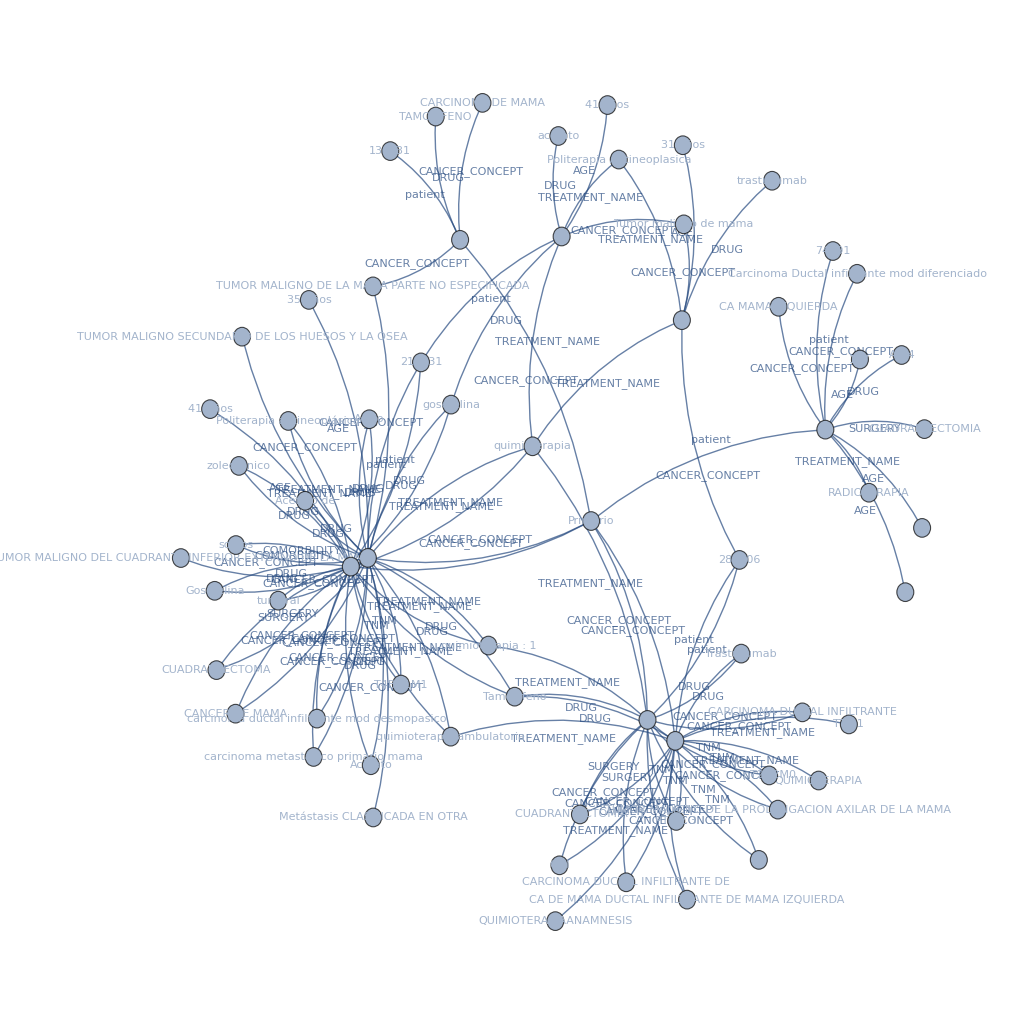

Part::partw: Part 8248 of {136631,0,CARCINOMA DE MAMA,Primario,TAMOXIFENO,TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA,35 Años,1,217231,Acetato,«3571»} does not exist.

Table::nliter: Non-list iterator VertexDegree[gp,VertexList[gp]⟦i⟧] at position 2 does not evaluate to a real numeric value.

Table[VertexList[gp]⟦i⟧,VertexDegree[gp,VertexList[gp]⟦i⟧],{i,2}]

136631

3581

5

```mathematica
nodos = {}
GenerateGraph[data_]:= Module[{doc},
doc = data[[2,3]];
AppendTo[nodos,Labeled[data[[2,1]]<->data[[2,3]],"patient"]];
For[i=2,i<100,i++,
AppendTo[nodos,Labeled[data[[i,2]]<-> data[[i,3]],data[[i,4]]]];
If[doc != data[[i,3]],AppendTo[nodos,Labeled[data[[i,1]]<->data[[i,3]],"patient"]]; doc=data[[i,3]]];]]
GenerateGraph[data]
gp = Graph[nodos,VertexLabels->Placed[Automatic,Center],GraphLayout->"GravityEmbedding"];
VertexCount[gp]
gp
(*SimpleGraph[gp]*)
```

```mathematica
Table[{VertexList[gp]⟦i⟧ ,VertexDegree[gp,VertexList[gp]⟦i⟧]},{i,VertexCount[gp]}] //TableForm;
```

```mathematica
nodoscw = {}
GenerateGraphCw[data_]:= Module[{doc},
AppendTo[nodos,Labeled[data[[2,1]]<->data[[2,3]],"patient"]];
For[i=2,i<100,i++,
AppendTo[nodos,Labeled[data[[i,2]]<-> data[[i,3]],data[[i,4]]]];
If[doc != data[[i,3]],AppendTo[nodos,Labeled[data[[i,1]]<->data[[i,3]],"patient"]]; doc=data[[i,3]]];]]
GenerateGraphCw[data]
```

muchas cosas escritas para ver si las guarda